## Objects of Expression

## Dynamic

```mathematica
Dynamic[expr]
```

an object that displays as the dynamically updated current value of expr. 每次相关的量变化时, Dynamic 就会重新计算 expr 并展示当前结果.

Dynamic[expr] 输出的结果会随 expr 的当前值动态地变化. 但是 Dynamic object 本身的历史位置 (即 In, Out 位置) 不变. 也就是说这个动态的对象本身属于过去, 但它表示的值始终是当前的值. 所以才称为 Dynamic.

Dynamic[] 中可以包含任意种类的表达式. 这似乎很显然, 但正是这样才保证了无论相关的变量变化成何种表达式, Dynamic[] 都能对应地变化着输出.

从效果上来看, 基础版本的 Dynamic[] 就是在任意的普通输入外面套上一个 dynamic 性质.

## Slider

```mathematica
Slider[x] (*a slider with setting x in 0-1*)
Slider[x,{Subscript[x, min],Subscript[x, max],dx}] (*a slider with setting x from Subscript[x, min] to Subscript[x, max] in steps dx*)
```

```mathematica
Slider[Dynamic[x]]
```

对于上面这个 Slider 而言, x 的值和 slider 上滑块的位置 (实质是鼠标的点击位置) 是始终一致的. 也就是说: 当 x 值在其他地方改变时, Dynamic[x] 值改变, 滑块的位置从而改变; 当 slider 上滑块的位置改变时, Slider 会反馈一个值给 Dynamic[x] , 从而 x 值也跟着变化.

例如:

```mathematica
DynamicModule[{x},x=0.3;{Slider[Dynamic[x]],Dynamic[x]}]
```

这种动态链接是双向的. Sliders connected to a variable move together because they both reflect and control the value of the same variable (同一个地址单元). When you drag a slider thumb, the system constructs and evaluates expressions of the form expr = new, where expr is the expression given in the first argument to Dynamic and new is the proposed new value
determined by where you have dragged the slider thumb. If the assignment can be done, the new value is accepted. If the assignment fails, the slider will not move.

For example, the following code generates two sliders. These two sliders move in opposite directions when you move the
first one. However, trying to move the second slider gives an error because you cannot assign a new value to the expression 1-x .

```mathematica
DynamicModule[{x=0},{Slider[Dynamic[x]],Slider[Dynamic[1-x]]}]
```

这个问题可以配合 Dynamic 函数的一种高级形式来解决:

```mathematica
Slider[Dynamic[expr,f]]
```

它的意义是:

continually evaluates f[val] during interactive changing or editing of val. 而这个 val 就是由滑块在 slider bar 上的位置 (实质是鼠标的点击位置) 来反馈的.

### Some notes

Dynamic and control constructs such as Slider carry with them the behavior of dynamically displaying or changing in real time the current value of the expression or variable they are linked to, wherever they occur, even in expressions.

## Panel

```mathematica
Panel[expr] (*displays a panel containing expr*)
```

## Style

```mathematica
Style[expr,options](*displays expr with specific formatting settings*)
```

## Labeled

```mathematica
Labeled[expr,label] (*displays expr with label*)
Labeled[expr,label,pos] (*specify the position of label*)
Labeled[expr,{Subscript[label, 1],Subscript[label, 2],...},{Subscript[pos, 1],Subscript[pos, 2],...}]
```

label is just another expression that is put around expr , thus it can be anything.

The region of a Labeled object does not include the label.

```mathematica
Labeled[expr,label,Background->Red]
```

exprlabel

## Row

```mathematica
Row[{Subscript[expr, 1],Subscript[expr, 2],...}]
```

an object that formats the expr_i as if they appeared as successive elements arranged in a row, with no extra space in between.

## Column

```mathematica
Column[{Subscript[expr, 1],Subscript[expr, 2],...}]
```

an object that formats with the expr_i arranged in a column, with expr_1 above expr_2 , etc.

## Grid

## GraphicsRow

```mathematica
GraphicsRow[{Subscript[g, 1],Subscript[g, 2],...}](*generates a graphic in which the Subscript[g, i] are laid out in a row.*)
GraphicsRow[list,spacing[(*leaves the specified spacing between successive elements.*)
```

## GraphicsColumn

## GraphicsGrid

## Dynamic Interactivity

## Manipulate

```mathematica
Manipulate[expr,{u,Subscript[u, min],Subscript[u, max],du}]
Manipulate[expr,{{u,Subscript[u, init]},Subscript[u, min],Subscript[u, max],du}]   (*with initial value*)
Manipulate[expr,{{u,Subscript[u, init],Subscript[u, label]},Subscript[u, min],Subscript[u, max],du}]   (*with label*)
Manipulate[expr,{u,{Subscript[u, 1],Subscript[u, 2],...}}]   (*with discrete manipulate points*)
```

控制变量 u 的更一般形式是: {{u,...},...,opts}. 例如:

```mathematica
{{a,8,Style["a",Italic]},2,10,0.01,Appearance->"Labeled"}
```

生成控制栏或菜单变量的形式: {u,{u_1→lbl_1,u_2→lbl_2,...}}. 例如:

```mathematica
{{ctrl,1,""},{1->"3D plot",2->"contour plot"}}
```

### Some notes

Manipulate in fact produces a combination of Dynamic, controls(e.g. Slider), and formatting constructs(e.g. Panel, Column, Row, ...), not fundamentally different from what you can do using these lower-level functions.

## Equation Solving

## Solve

Solve automatically thread Equal over lists to obtain a set of equations.

```mathematica
Solve[{2x,3x}+{y,2y}=={1,2},{x,y}]
```

{{x→0,y→1}}

## LinearSolve

```mathematica
LinearSolve[A,b]
```

finds an x that solves the matrix equation A.x == b .

```mathematica
LinearSolve[A]
```

generates LinearSolveFunction[dimensions,data] which is a function head that can be applied to different b .

It’s obvious that LinearSolve[A,b] is equivalent to LinearSolve[A][b] .

# Core Language

## The Syntax of language

Tokens

输入的一切首先会转化为 tokens. 每个 token 都是一个语法单元. 它们再被转化为统一的 FullForm 形式.

5 types of tokens: symbols, strings, numbers, operators, input to be ignored.

Operators

## Types

Operators are ultimately what determine the structure of the expression formed from a particular piece of input.

6 types of operators: prefix, infix, postfix, matchfix, compound, overfix

## Precedence & Grouping

所有的 operator 都设置了优先级.

算符的优先级可以通过小括号 ( ) grouping 来改变.  内层的 group 优先级高于外层 group.

同一优先级的 operators 设置了相应的 automatic grouping 规则. 以保证在 interpret 时没有歧义.

3 types of automatic grouping:

flat: 不做 grouping, e.g., a+b+c+d==a+b+c+d.

```mathematica
a+b+c+d//InputForm
```

a + b + c + d

left group, e.g., a/b/c/d==((a/b)/c)/d.

```mathematica
a/b/c/d//FullForm
```

Times[a,Power[b,-1],Power[c,-1],Power[d,-1]]

right group, e.g., a^b^c^d==a^(b^(c^d)).

```mathematica
a^b^c^d//FullForm
```

Power[a,Power[b,Power[c,d]]]

注意, 这些规则只涉及将输入转化为 FullForm 过程. 而不涉及表达式的运算. 表达式的运算过程由 Standard Evaluation Procedure 来决定. 这里的规定是为了保证转化过程能够将一个输入无歧义地转化为 FullForm 内部形式.

## Define Rules for Operators without Built-in Meanings

一些算符没有内部定义, 但仍然有优先级.

## Standard Evaluation Procedure

Evaluate the head of an expression.
Check for attributes.
(The head of an expression is also an expression to be evaluated.)

Evaluate every argument of the expression.
(The arguments of an expression is also an expressions to be evaluated.)

Apply rules for Orderless,Listable,Flat to the expression being evaluated.

Apply definitions regarding to the expression. 
(A result is obtained finally.)

Evaluate the result.
(The result is also an expression to be evaluated.)

这意味着如果运算后内层的 head 还在, Flat 才起作用. 例如下面这个的结果不是 f[a,b,{1,2,3},c]. 因为内层的 f 表达式要先运算完外层的 f 的 Flat 才能起作用, 但那时内层已经没有 f 了.

```mathematica
SetAttributes[f,Flat];
f[{el___}]:=g[el];
f[a,b,f[{1,2,3}],c]
```

f[a,b,g[1,2,3],c]

## Expressions

Dimensions of Expression

## Length

## Dimensions

```mathematica
Dimensions[expr]
Dimensions[expr,n](*down to level n*)
```

Dimensions returns dimensions of those levels in which expr are still a full array.

```mathematica
Dimensions[{{a,b,c},{d,e},{f}}]
```

{3}

Each successive level in expr sampled by Dimensions must have the same head.

```mathematica
Dimensions[f[g[x,y],g[a,b],g[s,t]]]
```

{3}

Expression Structure

## Sequence

```mathematica
Sequence[expr1,expr2,...](*a sequence of expressions.*)
```

Sequence objects will automatically be flattened out in all functions except those with attribute SequenceHold or HoldAllComplete.

Sequence[] represents an empty sequence. An empty Sequence[] in a Sequence of expressions is automatically dropped.

```mathematica
Sequence[a,b,Sequence[],c]
```

Sequence[a,b,c]

```mathematica
{1,2,3,4}/.(4->Sequence[])
```

{1,2,3}

## Atomic Elements of Expressions

Atomic expressions have no subexpression.

### AtomQ

```mathematica
AtomQ[expr](*yields True if expr is an expression which cannot be divided into subexpressions*)
```

AtomQ gives True for symbols, numbers, strings, and other raw objects, such as sparse arrays.

AtomQ gives True for any object whose subparts cannot be accessed using functions like Map.

### Numbers

The type of a specific number is assgined after evaluating it.

#### Integer

Integer in base b: b^^digits.

#### Rational

Number of Rational type can not be single integer.

The FullForm of a rational number is Rational[numerator,denominator]. But a Rational is regarded atomic.

x/y is not necessarily Rational. / is essentially Divide operation. The result number can be different type, and will be assigned and treated as number of appropriate atomic type.

```mathematica
FullForm[HoldForm[22/7]]
```

HoldForm[Times[22,Power[7,-1]]]

And even constructing by Rational[n,d] will not 100% yields a Rational. The real type is decided by the specific result.

```mathematica
Rational[2,1]//Head
```

Integer

And beyond sensible scope, the input cannot be interpretted.

```mathematica
Rational[2.,1.]
```

Rational[2.,1.]

#### Real

Real means essentially floating-point number, rather than domain ℝ by mathematics.

In put floating-point number in scientific notation: x.xxx*^exponent.

Floating-point number in base b: b^^digits.mantissa.

#### Complex

x+I y.

FullForm of Complex number is Complex[a,b].

实部或虚部其一不是 Real 另一个是 Real 时, 前者转换为 Real.

Numbers entered in the form x+Iy only become Complex numbers on evaluation.

Structural Operations on Expressions

## Head-related operations

### Through

```mathematica
Through[p[f1,f2][x]]
Through[expr,h](*performs the transformation wherever h is the head of head of expr. *)
```

Through distributes operators that appear inside the heads of expressions.

```mathematica
Through[{f,g,h}[x]]
```

{f[x],g[x],h[x]}

```mathematica
Through[(f +g)[x,y],Times]
```

(f+g)[x,y]

Parts of Expressions

## position index

### head--0

### element--1,2,3,...

### Span(;;)

```mathematica
i;;j(*a span of elements i through j.*)
i;; (*from i to the end*)
;;j (*from the beginning to j*)
;; (*from beginning to end*)
i;;j;;k(*from i to j in steps of k*)
i;; ;;k(*from i to end in steps of k*)
;;j;;k(*from beginning to j in steps of k*)
;; ;;k(*from beginning to end in steps of k*)
```

```mathematica
;; ;;k//FullForm
```

Span[1,All,k]

m[[i;;j;;k]] is equivalent to Take[m,{i,j,k}].

Negative i and j count from the end. Negative k is negative step.

```mathematica
f[Sequence@@Range[1,8]]⟦6;;1;;-1⟧
```

f[6,5,4,3,2,1]

## take parts

### Part(⟦...⟧)

### First

### Last

### Most

```mathematica
Most[expr](*gives a expression with the last element of expr removed.*)
```

Most[expr] equals to Drop[expr,-1].

### Rest

```mathematica
Rest[expr](*gives a expression with the first element of expr removed.*)
```

Rest[expr] equals to Drop[expr,1].

### Take

### Drop

### Extract

### Level

```mathematica
Level[expr,levelspec](*gives a list of all subexpressions of expr*)
Level[expr,levelspec,f](*apply f to the extracted elements*)
```

Level[expr,levelspec] 相当于 Level[expr,levelspec,List]

```mathematica
Level[a+f[x,y^n],{-1},CirclePlus]

Level[a+f[x,y^n],{-1}]
```

a⊕x⊕y⊕n

{a,x,y,n}

A positive level n consists of all parts of expr specified by n indices.

Level traverses expressions in depth-first order, so that the subexpressions in the final list are ordered lexicographically by their indices.

## ReplacePart

```mathematica
ReplacePart[expr,i->new](*replace i-th element in expr by new.*)
ReplacePart[expr,{i->new1,j->new2,...}]
ReplacePart[expr,{i,j,...}->new]
ReplacePart[expr,{{i,j,...}->new1,...}]
```

Part position specifications can be patterns.

```mathematica
ReplacePart[Table[i^j,{i,4},{j,4}],{i_,j_}/;(Abs[i-j]==1)->a[i]+a[j]]//TableForm
```

1 | a[1]+a[2] | 1 | 1
a[1]+a[2] | 4 | a[2]+a[3] | 16
3 | a[2]+a[3] | 27 | a[3]+a[4]
4 | 16 | a[3]+a[4] | 256

Each pattern is effectively tested against each list of part numbers for parts in expr.

ReplacePart[expr,i:>new] can be used to replace a part without first evaluating it. With a rule such as patt:>new, new is evaluated separately for each position that matches patt.

## Sow

```mathematica
Sow[e](*specifies that e should be collected by the nearest enclosing Reap.*)
Sow[e,tag](*specifies that e should be collected by the nearest enclosing Reap whose pattern is matched by tag.*)
Sow[e,{Subscript[tag, 1],Subscript[tag, 2],...}](*specifies that e should be collected once for each Subscript[tag, i] that matches a pattern.*)
```

Sow[e,...] returns e.

```mathematica
Reap[Sum[Sow[i^2]+1,{i,10}]]
```

{395,{{1,4,9,16,25,36,49,64,81,100}}}

Sow can be used anywhere in a computation.

一个 Sow 里面如果有多个 tag, 每个 tag 都会被尝试匹配一次, 每次匹配成功 Reap 都独立地生成一次结果.

```mathematica
Reap[Sow[1,{x,x}];Sow[2,x];Sow[3,y];Sow[4,y],x]
```

{4,{{1,1,2}}}

```mathematica
Reap[Sow[1,{x,y}];Sow[2,x];Sow[3,y];Sow[4,y]]
```

{4,{{1,2},{1,3,4}}}

## Reap

```mathematica
Reap[expr](*gives the value of expr together with all expressions to which Sow has been applied during its evaluation.
            Expressions sown using Sow[e] or Sow[e,Subscript[tag, i]] with different tags are given in different lists. *)
Reap[expr,pattern](*reaps only expressions sown with tags that match pattern.*)
Reap[expr,{Subscript[patt, 1],Subscript[patt, 2],...}](*puts expressions associated with each of the Subscript[patt, i] in a separate list.*)
Reap[expr,pattern,f](*returns {expr,{f[Subscript[tag, 1],{Subscript[e, 11],Subscript[e, 12],…}],…}}.*)
```

Reap[expr] is equivalent to Reap[expr,_].

不同 tag 匹配同一个 pattern, 结果会区分在不同的 list 中.

```mathematica
Reap[Sow[1,f[x]];Sow[2,f[x]];Sow[3,x];Sow[4,y]]
```

{4,{{1,2},{3},{4}}}

```mathematica
Reap[Sow[1,f[x]];Sow[2,f[y]];Sow[3,g[x]];Sow[4,g[y]],f[_]]
```

{4,{{1},{2}}}

```mathematica
Reap[Sow[1,x];Sow[2,{x,y}];Sow[3,{y,z}];Sow[4,{x,y,z}],x|y]
```

{4,{{1,2,4},{2,3,4}}}

注意 Alternatives object 是一个 pattern.

不同 tag 匹配不同 pattern, 结果更会区分在不同的 list 中.

```mathematica
Reap[Sow[1,f[x]];Sow[2,f[y]];Sow[3,g[x]];Sow[4,g[y]],{f[_],g[_]}]
```

{4,{{{1},{2}},{{3},{4}}}}

```mathematica
Reap[Sow[1,{x,x}];Sow[2,y];Sow[3,x],{x,x,y}]
```

{3,{{{1,1,3}},{{1,1,3}},{{2}}}}

注意以下两个结果的不同. 这说明结果的 list 层级从里至外分别是: 同一个 tag, 同一个 pattern, 不同的 pattern.

```mathematica
Reap[Sow[1,{x,y}];Sow[2,x];Sow[3,y];Sow[4,y]]
```

{4,{{1,2},{1,3,4}}}

```mathematica
Reap[Sow[1,{x,y}];Sow[2,x];Sow[3,y];Sow[4,y],{x,y}]
```

{4,{{{1,2}},{{1,3,4}}}}

Sow 没有 Hold 类属性, 因此 tag 会被运算.

```mathematica
Reap[Sow[#,#>0]&/@{1,-1,2,-3,1,4,5};]
```

{Null,{{1,2,1,4,5},{-1,-3}}}

f 作用于一个 tag 和相应的所有元素. 注意生成的 list 逻辑结构实际上与前面相同.

```mathematica
Reap[Sow[1,{x,x}];Sow[2,y];Sow[3,x],x|y,Rule]
```

{3,{x→{1,1,3},y→{2}}}

```mathematica
Reap[Sow[1,{x,x}];Sow[2,y];Sow[3,x],{x,y},Rule]
```

{3,{{x→{1,1,3}},{y→{2}}}}

Examples:

Find the unique elements in a list, in the order they first occur.

```mathematica
Reap[Sow[1,{a,a,b,d,c,a}],_,#&][[2]]
```

{a,b,d,c}

If no expressions are sown, Reap returns an empty list of expressions it has reaped:

```mathematica
Reap[x,x]
```

{x,{}}

```mathematica
Reap[x,{x,y}]
```

{x,{{},{}}}

Testing Expressions

## Equality & Inequality

### Equal(==)

Equal is usually used to test mathematical equality, whereas SameQ is used to test structural equality.

### Unequal(!=,≠)

### SameQ(===)

```mathematica
lhs===rhs(*yields True if the expression lhs is structurally identical to rhs, and yields False otherwise.*)
```

SameQ requires exact correspondence between expressions, except that it still considers Real numbers equal if they differ in their last binary digit.

```mathematica
0.===0
```

False

```mathematica
0.==0
```

True

lhs 和 rhs 运算之后才进行比较.

```mathematica
x===Simplify[√(x^2),x>0]
```

True

### UnsameQ(=!=)

```mathematica
lhs=!=rhs(*yields True if two expressions are not structurally identical.*)
```

```mathematica
0.=!=0
```

True

```mathematica
0.!=0
```

False

### Less(<)

### Greater(>)

### LessEqual(<=)

### GreaterEqual(>=)

## Logical Combinations

### And(&&,∧)

And has attribute HoldAll and explicitly controls the evaluations of its arguments. In e_1&&e_2&&…, the e_i are evaluated in order, stopping if any of them are found to be False.

And has attribute Flat.

And gives symbolic results when necessary, removing initial arguments that are True.

### Or(||,∨)

Or has attribute HoldAll, and explicitly controls the evaluation of its arguments. In e_1||e_2||… the e_i are evaluated in order, stopping if any of them are found to be True.

Or gives symbolic results when necessary, removing initial arguments that are False.

Or is Flat.

```mathematica
Attributes[Or]
```

{Flat,HoldAll,OneIdentity,Protected}

## Numerical Properties

### NumericQ

```mathematica
NumericQ[expr](*gives True if expr is a numeric quantity, False otherwise.*)
```

An expression is considered a numeric quantity if it is either an explicit number or a mathematical constant  or is a function that has attribute NumericFunction and all of whose arguments are numeric quantities.

N[expr] 能给出数值时, NumericQ 基本上就是 True.

### Positive

```mathematica
Positive[x](*True if x is a positive number.*)
```

False if x is manifestly a negative numerical quantity, a complex numerical quantity, or zero.

Quantities that are not NumericQ remains unevaluated.

Positive is Listable.

## TrueQ

```mathematica
TrueQ[expr](*yields True only if the expr is explicitly True.*)
```

对表达式运算, 只有结果是逻辑值 True 时才返回 True.

```mathematica
TrueQ[x=1]
```

False

You can use TrueQ to “assume” that a test fails when its outcome is not clear.

Evaluation Control

## Hold

```mathematica
Hold[expr](*maintains expr in an unevaluated form.*)
```

Hold has attribute HoldAll, and performs no operation on its arguments.

## HoldComplete

```mathematica
HoldComplete[expr](*shields expr completely from the standard Mathematica evaluation process,
                    preventing even upvalues associated with expr from being used. *)
```

HoldComplete has attribute HoldAllComplete, and performs no operations on its arguments.

## HoldForm

```mathematica
HoldForm[expr](*prints as the expression expr, with expr maintained in an unevaluated form.*)
```

HoldForm allows you to see the output form of an expression without evaluating the expression.

Hold 和 HoldForm 的区别是前者的输出形式包含 Hold head, 后者只输出保持住的原表达式. 但是两者的内部形式 FullForm 各自都包含 Hold/HoldForm head, 不然怎么 hold?

Example 1:

```mathematica
Hold[1+1]
```

Hold[1+1]

```mathematica
HoldForm[1+1]
```

1+1

```mathematica
%//FullForm
```

HoldForm[Plus[1,1]]

Example 2:

```mathematica
Hold[Integrate[x^2 E^-x^2,x]]
```

Hold[∫x^2 ⅇ^(-x^2)ⅆx]

```mathematica
HoldForm[Integrate[x^2 E^-x^2,x]]
```

∫x^2 ⅇ^(-x^2)ⅆx

```mathematica
%//FullForm
```

HoldForm[Integrate[Times[Power[x,2],Power[E,Times[-1,Power[x,2]]]],x]]

HoldForm has attribute HoldAll.

## HoldPattern

```mathematica
HoldPattern[expr](*equivalent to expr for pattern matching, but prevents expr from evaluation in pattern matching.*)
```

Pattern 在匹配之前也会做一些运算. 因此下例中匹配不会发生.

```mathematica
a+b/._+_->2
```

a+b

使用 HoldPattern 防止对 pattern 进行运算.

```mathematica
a+b/.HoldPattern[_+_]->2
```

2

## ReleaseHold

```mathematica
ReleaseHold[expr](*removes Hold, HoldForm, HoldPattern and HoldComplete*)
```

ReleaseHold removes only one layer (the outermost layer) of Hold etc.; it does not remove inner occurrences in nested Hold etc. functions.

## Evaluate

```mathematica
Evaluate[expr](*causes expr to be evaluated even if it appears as the argument of a function 
                whose attributes specify that it should be held unevaluated.*)
```

## Unevaluated

```mathematica
Unevaluated[expr](*represents the unevaluated form of expr when it appears as the argument to a function.*)
```

f[Unevaluated[expr]] effectively works by temporarily setting attributes to f so that f holds its argument unevaluated, then evaluating f[expr].

## Update

```mathematica
Update[s](* update all expressions involving s*)
Update[](* update absolutely all expressions*)
```

## Rules & Patterns

Patterns

## Basic Pattern Objects

### Blank(_)

```mathematica
Blank[]
_
Blank[h]
_h
```

### BlankSequence(__)

```mathematica
BlankSequence[]
__
BlankSequence[h](*any sequence of one or more expressions, all of which have head h*)
__h
```

### BlankNullSequence(___)

```mathematica
BlankNullSequence[]
___
BlankNullSequence[h]
___h
```

BlankSequence can match nothing, which is empty sequence Sequence[]. A “nothing” can be regarded as having any head.

```mathematica
g[]/.g[h___sef]->h
```

Sequence[]

When BlankSequence with head matches “something”, head must be matched as well.

```mathematica
g[a,b]/.g[h___sef]->h
```

g[a,b]

## Named Patterns

### Pattern(:)

```mathematica
Pattern[s,pattern]
s:pattern
```

s_ is equivalent to s:_, s_h to s:_h, etc.

## Composite Patterns

### Alternatives(|)

```mathematica
Subscript[p, 1]|Subscript[p, 2]|...(*a pattern object which represents any of the patterns Subscript[p, i].*)
Alternatives[p1,p2,...]
```

```mathematica
FullForm[a|b|c]
```

Alternatives[a,b,c]

Example:

```mathematica
Cases[{5.6,5/6,5,6,x},_Integer|_Real]
```

{5.6,5,6}

### Repeated(..)

```mathematica
Repeated[patt]
patt..
Repeated[p,max]
Repeated[p,{min,max}]
Repeated[p,{n}](*repeated exactly n times*)
```

All the objects in the sequence represented by p.. must match p.

### RepeatedNull(...)

```mathematica
RepeatedNull[p]
p...
RepeatedNull[p,max]
RepeatedNull[p,{min,max}]
RepeatedNull[p,{n}]
```

### Except

```mathematica
Except[c](*matches anything but not c*)
Except[c,p](*matches p but not c*)
```

Except[c] equals to Except[c,_].

When used as string pattern, c can only be single-character string or a list of single-character strings.

### Longest

```mathematica
Longest[p](*matches the longest sequence consistent with p.*)
Longest[p,priority]
```

Priorities can be any expression, and are ordered in standard Wolfram Language Sort order. Longest[p] specifies the highest possible priority.

If no explicit Longest or Shortest is given, ordinary expression patterns are normally effectively assumed to be Shortest[p], while string patterns are assumed to be Longest[p].

### Shortest

## Restrictions on Patterns

### PatternTest(?)

```mathematica
pattern?test(*a pattern that is matched only if test[expr] gives True.*)
PatternTest[pattern,test]
```

Any result other than True is regarded as failure.

In a form such as __?test, every element in the sequence matched by __ must yield True when test is applied.

PatternTest is HoldRest.

```mathematica
FullForm[p?test]
```

PatternTest[p,test]

Rules

## Representing Rules

### Rule(->)

lhs→rhs 在替换之前会计算 lhs 和 rhs.

Symbols that occur as pattern names in lhs are treated as local to the rule. This is true when the symbols appear on the right-hand side of /; conditions in lhs, and when the symbols appear anywhere in rhs, even inside other scoping constructs.

Rule constructs can be nested in any way. Rule is treated as a scoping construct, so that inner variables are renamed if necessary.

### RuleDelayed(:>)

lhs:>rhs 在替换之前计算 lhs, 保持 rhs 不变.

## Applying Rules

### ReplaceAll(/.)

```mathematica
expr/.rules
```

ReplaceAll looks at each part of expr, tries all the rules on it, and then goes on to the next part of expr. The first rule that applies to a particular part is used; no further rules are tried on that part, or on any of its subparts.

ReplaceAll traverses expression from the outermost level to the innermost level.

```mathematica
f[a+f[b]]/.f[x_]->g[x]
```

g[a+f[b]]

```mathematica
{{a,b},{c,d}}/._?Print->Null
```

{{a,b},{c,d}}

List

{a,b}

List

a

b

{c,d}

List

c

d

{{a,b},{c,d}}

As a consequence, a particular rule is tried from outside in. And a rule constructed for the whole expression is tried before those for its subparts.

```mathematica
a->b/.{b->c,(x_->y_)->(x->d)}
```

a→d

### ReplaceRepated(//.)

```mathematica
expr//.rules
```

expr//.rules effectively applies /. repeatedly, until the results it gets no longer change.

Because in essence ReplaceRepeated is a variant of ReplaceAll, it traverses expression from the outermost level to the innermost level, as does ReplaceAll.

It performs one complete pass over the expression using /., then carries out the next pass.

### Replace

```mathematica
Replace[expr,rules](*tries to apply rules to the entire expr.*)
Replace[expr,rules,levelspecs]
```

The default levelspec is {0}.

When levelspec covers multiple levels, rules are tried from inside out, as opposite of ReplaceAll.

```mathematica
Replace[{{a,b},{c,d}},_?Print->Null,{0,-1}]
```

a

b

{a,b}

c

d

{c,d}

{{a,b},{c,d}}

{{a,b},{c,d}}

Replace 默认不尝试 head 部分, 需要设置 Heads→True .

### ReplaceList

Pattern Matching Functions

## Cases

```mathematica
Cases[list,pattern]
Cases[list,pattern->rhs]
Cases[list,pattern,levelspec]
Cases[list,pattern,levelspec,n](*first n found*)
```

The head of list need not be List, however, the matched cases will always be collected into a List.

```mathematica
Cases[f[f[1,2],f[f[2,3],f[f[3,4],f[f[4,5],f[f[5,6],f[]]]]]],f[__]]
```

{f[1,2],f[f[2,3],f[f[3,4],f[f[4,5],f[f[5,6],f[]]]]]}

Rule can also be RuleDelayed.

The default value for levelspec in is {1}.

Cases traverses the parts of expr in a depth-first order, with leaves visited before roots.

## Position

```mathematica
Position[list,patt]
Position[list,patt,levelspec]
Position[list,patt,levelspec,n](*first n found*)
Position[patt](*operator form*)
```

```mathematica
Position[RandomReal[5,5],_?(#>2&)]
```

{{2}}

```mathematica
Position[_?(#>2&)]@RandomReal[5,5]
```

{{3},{4},{5}}

```mathematica
Position[{1+x^2,5,x^4,a+(1+x^2)^2},x^_,2]
```

{{1,2},{3}}

## Count

## Variables & Functions

Assignments

## Set(=)

由于 Set 将 rhs 赋值给 lhs, 需要保持 lhs 表达式的形式. 故它有 HoldFirst.

Symbols that occur as pattern names in lhs are treated as local to the assignment. This is true when the symbols appear on the right-hand side of /; conditions in lhs, and when the symbols appear anywhere in rhs, even inside other scoping constructs.

## SetDelayed(:=)

## TagSet(/:=)

```mathematica
f/:lhs=rhs(*assigns rhs to be the value of lhs, and associates the assignment with the symbol f.*)
```

TagSet defines upvalues or downvalues as appropriate.

The symbol f in f/:lhs=rhs must appear in lhs as the head of lhs, the head of the head, one of the elements of lhs, or the head of one of the elements.

## Information(?,??)

```mathematica
Information[symbol](*prints information about a symbol.*)
Information["string"]
```

??symbol prints the same information as Information[symbol]would.

For built-in symbols, Information gives attributes, defaults, and options, as well as usage messages:

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

?symbol prints the same information as Information[Sin,LongForm→False]would.

"string" can be a string pattern. When multiple matches are found, a list of matches are generated.

```mathematica
?"*Plot"~~__
```

## DownValues

## UpValues

Function Attributes

## Attributes

```mathematica
Attributes[symbol](*gives the list of attributes for a symbol.*)
```

The attributes of a symbol can be set by assigning a value to Attributes[symbol]. If a single attribute is assigned, it need not be in a list.

```mathematica
Attributes[f]={Listable,Orderless,Flat};Attributes[f]
```

{Flat,Listable,Orderless}

Attributes[s]={} clears all attributes of a symbol.

Attributes[{s_1,s_2,…}] gives a list of the attributes for each of the s_i.

```mathematica
Attributes[{Sin,Plot}]
```

{{Listable,NumericFunction,Protected},{HoldAll,Protected,ReadProtected}}

Attributes for functions must be set before any definitions that involve the functions are given.

The complete list of possible attributes for a symbol f is:

The attributes of Attributes:

```mathematica
Attributes[Attributes]
```

{HoldAll,Listable,Protected}

注意 Attributes 有 HoldAll 属性. 因此它的变量不会被运算.

```mathematica
symbol={Plus,Times};Attributes[symbol]
```

{}

虽然是给 Attributes[f] 赋值, 但这个值不被认为是 Attributes 的 downvalue, 而可以看作是 f 的一种特殊的 upvalue.

10 system symbols with the most attributes:

```mathematica
TableForm[Take[Sort[{#,Attributes[#]}&/@Names["System`*"],Length[#1[[2]]]>Length[#2[[2]]]&],10],TableDepth->2]
```

Times | {Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}
Plus | {Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}
ChampernowneNumber | {Constant,Listable,NHoldFirst,NumericFunction,Protected,ReadProtected}
ZetaZero | {Listable,NHoldFirst,NumericFunction,Protected,ReadProtected}
UnitTriangle | {Listable,NumericFunction,Orderless,Protected,ReadProtected}
UnitBox | {Listable,NumericFunction,Orderless,Protected,ReadProtected}
QPolyGamma | {Listable,NHoldFirst,NumericFunction,Protected,ReadProtected}
Min | {Flat,NumericFunction,OneIdentity,Orderless,Protected}
Max | {Flat,NumericFunction,OneIdentity,Orderless,Protected}
LCM | {Flat,Listable,OneIdentity,Orderless,Protected}

## SetAttributes

```mathematica
SetAttributes[s,attr](*adds attr to the list of attributes of the symbol s.*)
SetAttributes[s,{Subscript[attr, 1],Subscript[attr, 2],...}](*adds a list of attributes.*)
SetAttributes[{Subscript[s, 1],Subscript[s, 2],...},{Subscript[attr, 1],Subscript[attr, 2],...}](*adds attributes to a list of symbols.*)
```

SetAttributes has the attribute HoldFirst.

```mathematica
Attributes[SetAttributes]
```

{HoldFirst,Protected}

## ClearAttributes

```mathematica
ClearAttributes[s,attr](*Clear attr from the attributes of the symbol s.*)
ClearAttributes[s,{Subscript[attr, 1],attr_(2,...)}](*Clear multiple attributes.*)
ClearAttributes[{Subscript[s, 1],Subscript[s, 2],...},{Subscript[attr, 1],Subscript[attr, 2],...}](*Clear attributes from multiple symbols.*)
```

ClearAttributes has the attribute HoldFirst.

## HoldFirst

## HoldRest

## HoldAll

## HoldAllComplete

Evaluate cannot be used to override HoldAllComplete.

## SequenceHold

## Temporary

an attribute assigned to symbols which are created as local variables by Module.

Symbols with attribute Temporary are automatically removed when they are no longer needed.

Symbols with attribute Temporary conventionally have names of the form aaa$nnn.

## NumericFunction

an attribute that can be assigned to a symbol f to indicate that f[arg_1,arg_2,…] should be considered a numeric quantity whenever all the arg_i are numeric quantities.

Most standard built-in mathematical functions are NumericFunction.

## List Manipulations (not only for List)

Constructing Lists

## Range

```mathematica
Range[Subscript[i, max]]
Range[Subscript[i, min],Subscript[i, max]]
Range[Subscript[i, min],Subscript[i, max],di]
```

Range is Listable.

```mathematica
Range[{3,4}]
```

{{1,2,3},{1,2,3,4}}

```mathematica
Range[{2,3},{8,9},{1,2}]
```

{{2,3,4,5,6,7,8},{3,5,7,9}}

The numbers need not be integers, nor did they have to be numbers.

```mathematica
Range[1.1,2.2,0.2]
```

{1.1,1.3,1.5,1.7,1.9,2.1}

```mathematica
Range[x,4x,x]
```

{x,2 x,3 x,4 x}

## Table

Table is HoldAll.

Table[expr,spec] first evaluates spec, then localizes the variable specified, and successively assigns values to it, each time evaluating expr.

Table uses Block to localize variable.

Table[expr,{i,spec},{j,spec}] is equivalent to Table[Table[expr,{j,spec}],{i,spec}].

## Array

## Tuples

```mathematica
Tuples[list,n](*all possible n-tuples*)
Tuples[list,{n1,n2,...}]
Tuples[{list1,list2,...}](*a list of all possible tuples whose i^th element is from Subscript[list, i]*)
```

Tuples[list,n] 生成的 list 中每个元素都是长度 n 的 sublist (一个 n-tuple). sublist 中每个位置取原 list 的一个元素. 对于长度为 k 的 list, sublist 所有的可能取法有 k^n 种. 故 Tuples 生成的 list 长度为 k^n.

sublist 中先替换靠后的元素, 再替换靠前的元素. 即前面的位置等级高, 后面的等级低. 所替换的元素在原 list (元素库) 中从前至后逐个应用.

```mathematica
Tuples[{1,2,3},2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

The object list need not have head List. The head at each level in the arrays generated by Tuples will be the same as the head of list.

Tuples[{list1,list2,...}] 中, 每个 tuple 中 i 位置元素的库是 list_i. 每个 tuple 的长度是 list 的数目 (Length[{list1,list2,...}], 生成的 list 的长度是 ∏_i^n Length[list_i].

## SparseArray

```mathematica
SparseArray[{Subscript[pos, 1]->Subscript[val, 1],Subscript[pos, 2]->Subscript[val, 2],...}]
SparseArray[{Subscript[pos, 1],Subscript[pos, 2],...}->{Subscript[val, 1],Subscript[val, 2],...}]
SparseArray[list](*yields a sparse array version of list*)
SparseArray[list-of-rules,dims,val](*a sparse array of specified dimensions, with unspecified positions taken to be val*)
```

By default, unspecified elements are taken to be 0.

SparseArray[list] requires that list be a full array, with all parts at a particular level being lists of the same length. For example:

```mathematica
SparseArray[{{1,2},{1},{4,5}}]
```

SparseArray::rect: Rectangular array or list of rules expected at position 1 in SparseArray[{{1, 2}, {1}, {4, 5}}].

SparseArray[{{1,2},{1},{4,5}}]

ArrayRules[SparseArray[...]] gives a list of rules which can be used to construct the same sparse array.

```mathematica
ArrayRules[SparseArray[{{i_,j_}->i j},{5,5}]]
```

{{1,1}→1,{1,3}→3,{1,4}→4,{1,5}→5,{1,2}→2,{2,5}→10,{2,3}→6,{2,2}→4,{2,1}→2,{2,4}→8,{3,4}→12,{3,2}→6,{3,3}→9,{3,5}→15,{3,1}→3,{4,2}→8,{4,4}→16,{4,3}→12,{4,1}→4,{4,5}→20,{5,1}→5,{5,4}→20,{5,2}→10,{5,5}→25,{5,3}→15,{_,_}→0}

Without explicit dimensional specification, SparseArray yields a sparse array with dimensions exactly large enough to include elements whose positions have been explicitly specified.

Position pos_i can contain patterns. For example:

```mathematica
SparseArray[{{i_,j_}/;Abs[i-j]==1->i j,{i_,i_}->i^i,{5,1}->2,{1,5}->2}]//MatrixForm
```

(1 | 2 | 0 | 0 | 2
2 | 4 | 6 | 0 | 0
0 | 6 | 27 | 12 | 0
0 | 0 | 12 | 256 | 20
2 | 0 | 0 | 20 | 3125)

The standard output format for a sparse array indicates the number of nondefault elements and the total dimensions.

```mathematica
SparseArray[{{1,1}->1},{5,5}]
```

SparseArray[<1>,{5,5}]

注意这种输出形式只是真实输出的稀疏矩阵的一个表现形式, 不能直接作为稀疏矩阵本身使用. 因为你使用它时, 它就会作为 input form 出现, 这样你只使用了这个形式而已. 而且这个形式作为输入时是不合法的语法格式.

```mathematica
SparseArray["<"1">",{5,5}]
```

SparseArray::argb: SparseArray called with 0 arguments; between 1 and 4 arguments are expected.

SparseArray[]

要使用所生成的稀疏矩阵, 可以访问与之等价的 symbol, 例如 % 或与之相应的赋值变量; 也可以去获取该稀疏矩阵真实的 InputForm.

Whenever a sparse array is evaluated, it is automatically converted to an optimized standard form with structure SparseArray[Automatic,dims,val,...] . This structure is, however, rarely evident, since even operations like Length are set up to give results for the corresponding ordinary list, not for the raw SparseArray expression structure.

```mathematica
InputForm[SparseArray[{{1,1}->1},{5,5}]]
```

SparseArray[Automatic, {5, 5}, 0, {1, {{0, 1, 1, 1, 1, 1}, {{1}}}, {1}}]

A SparseArray object can be converted to normal list by Normal .

Positions that has been assigned with values are fixed and will not be changed by subsequent rules.

```mathematica
MatrixForm[SparseArray[{{2,3}->b,{_,3}->a,{i_,i_}->1},{4,4}]]
```

(1 | 0 | a | 0
0 | 1 | b | 0
0 | 0 | a | 0
0 | 0 | a | 1)

```mathematica
MatrixForm[SparseArray[{{i_,i_}->1,{2,3}->b,{_,3}->a},{4,4}]]
```

(1 | 0 | a | 0
0 | 1 | b | 0
0 | 0 | 1 | 0
0 | 0 | a | 1)

## ConstantArray

Elements of Lists

## Select

```mathematica
Select[list,f](*select elements for which f[e] is True*)
Select[list,f,n](*first n elements.*)
```

Select can be compiled, while Cases cannot.

Select works on SparseArray object, while Cases cannot.

Select is limited to one level only.

## Pick

```mathematica
Pick[list,sel](*when corresponding elements of sel is True.*)
Pick[list,sel,patt](*when corresponding elements of sel match patt*)
```

The “selector” list has to have the same length and structure as the data

## DeleteDuplicates

```mathematica
DeleteDuplicates[list](*delete all duplicates*)
DeleteDuplicates[list,test](*test pairs of elements to determine duplicates.*)
```

DeleteDuplicates[list] deletes all but the first occurrence of each distinct element that appears in list.

DeleteDuplicates never reorders elements, but only removes them.

DeleteDuplicates[list] means DeleteDuplicates[list,SameQ].

Rearranging Lists

## Sort

```mathematica
Sort[list](*sort into canonical order*)
Sort[list,f](*sort by *)
```

Sort[list,p] applies the function p to pairs of elements in list to determine whether they are in order. The default function p is OrderedQ[{#1,#2}]&.

## SortBy

```mathematica
SortBy[list,f](*sort by applying f to each element.*)
SortBy[f](*operator form*)
```

SortBy[{e_1,e_2,e_3,…},f] sorts the e_i so that the f[e_i] lie in canonical order.

## Ordering

```mathematica
Ordering[list](*a list of positions sorted by Sort[list]*)
Ordering[list,n](*positions of first n elements*)
Ordering[list,-n](*last n elements*)
Ordering[list,{m,n,p}]
Ordering[list,n,p](*Sort[list,p]*)
```

If there are several smallest elements in list, Ordering[list,1] will give only the position of the one that appears first.

The second arg can be any standard sequence spec.

Sort[list] can be reversely achieved by list⟦Ordering[list]⟧.

Restructuring Lists

## Flatten

```mathematica
Flatten[list] (*flatten out all levels of the list*)
Flatten[list,n] (*flatten out top n levels*)
Flatten[list,n,h](**)
Flatten[list,{{...},...}](*a list or matrix for advanced control*)
Flatten[f[...]](*flatten out subexpressions with head f.*)
```

Flatten by default applies to list object. Otherwise use Flatten[list,n,h] to flatten out subexpressions with head h down to level n.

识别 expr 中从 level 1 开始, 向下连续地与 expr 具有相同 head 的 subexpression. 将所识别到的所有 head 抹去, 将内部的 args 提升至第 1 层. 遇到的某个 subexpression 如果 head 不是 h, 忽略该表达式整体.

```mathematica
Flatten[{f[f[a,b]],{f[a],f[{a,b},f[c]]}},Infinity,f]
```

{a,b,{f[a],f[{a,b},f[c]]}}

Flatten 的普通用法第二变量只能是一个数字, 即 Flatten 至第 n 层.

高级用法中, 第二变量是一个 list, 或 nested list. list 中的元素实际上是原 list 层级序列的一个 permutation. 将某些层级用 list 括在一起表示这些层级的元素要 Flatten 在一起. 
例如:

Flatten[list,{{1},{3},{2},{4}}] 表示第 1 层仍在第 1 层, 第 3 层调整到第 2 层, 第 2 层调整到第 3 层, 第 4 层仍在第 4 层. 因此, 效果是第 2、3 层转置.

Flatten[list,{{2},{4},{1},{3}}] 则是 3 次转置的结果. 即 1,2,3,4->2,1,3,4->2,1,4,3->2,4,1,3. 这个代码的结果也相当于这三步 Flatten 的总效果.

Flatten[list,{{2,4},{1,3}}] 是在上述转置的基础上, 再把前两层和后两层分别用 Flatten 拉平, 剩下里层的元素.

## Transpose

```mathematica
Transpose[list] (*transpose the top two levels of list*)
Transpose[list,{Subscript[n, 1],Subscript[n, 2],...}] (*put the 1th level in list at level Subscript[n, 1], 2th level at level Subscript[n, 2], and so on.*)
```

要理解 Transpose 就只能把 list 看作 (多维) 矩阵. 上面第一个 Transpose 对 list 的顶 2 层进行操作, 相当于把普通的转置用于各种维度的矩阵. 第二个 Transpose 则是推广了转置这个概念的本身. 所以要说明什么是广义的转置:

矩阵的行列坐标线: 以矩阵左上角为原点, 行数和列数各自增长的两个方向就是行列坐标线. 这样的两个坐标线构成的描述矩阵元素位置的体系称为行列坐标线体系.

矩阵的转置最简单的理解是: 在固定的行列坐标线体系下将各元素放到与它沿对角线对称的位置上.

首先抛弃矩阵这个框架, 矩阵的所有元素固定本身客观不动, 在不同的坐标线体系下对这些元素的不同描述结果得到不同的矩阵, 这些矩阵之间就是相互转置的关系. 也就是说, 转置就是在改变描述同一组元素的坐标线体系, 即行列坐标线互换. 对于 n 维数堆而言, 将所有的行列坐标线从 1-n 编号, 1-n 的全排列就是对这个数堆的所有描述方式, 这些矩阵之间的关系就是转置关系. 于是对于一个 n 维矩阵, 共有 n!-1 种转置方法.

因此, 上面第二个 Transpose 形式中, {n_1,n_2,...} 代表了相对于顺序排列 (1-n) 的一种全排列, 即 坐标线 1 变成 第 n_1 条坐标线, 等等.

## Riffle

```mathematica
Riffle[{Subscript[e, 1],Subscript[e, 2],...},x](*gives {Subscript[e, 1],x,Subscript[e, 2],x,...}.*)
Riffle[{Subscript[e, 1],Subscript[e, 2],...},{Subscript[x, 1],Subscript[x, 2],...}](*gives {Subscript[e, 1],Subscript[x, 1],Subscript[e, 2],Subscript[x, 2],...}.*)
```

## Partition

```mathematica
Partition[list,n](*partition list into nonoverlapping sublists of length n.*)
Partition[list,n,d](*partition into sublists with offset d.*)
Partition[list,{Subscript[n, 1],Subscript[n, 2],...}](*partitions a nested list into a list of blocks of size Subscript[n, 1]×Subscript[n, 2]×…*)
Partition[list,{Subscript[n, 1],Subscript[n, 2],...},{Subscript[d, 1],Subscript[d, 2],...}](*offset at each level.*)
```

Incomplete sublists at the end are by default dropped.

Offset d 意思是每次拆分时向后移动 d 个长度.

Partition into sublists of length 3 with offset 1. 每次向后移动 1.

```mathematica
Partition[{a,b,c,d,e,f,g,h,i},3,1]
```

{{a,b,c},{b,c,d},{c,d,e},{d,e,f},{e,f,g},{f,g,h},{g,h,i}}

不设置 offset d 就等价于 n=d.

```mathematica
Partition[{a,b,c,d,e,f,g,h,i},3,3]
```

{{a,b,c},{d,e,f},{g,h,i}}

d>n 就会跳过中间元素.

```mathematica
Partition[{a,b,c,d,e,f,g,h,i},3,4]
```

{{a,b,c},{e,f,g}}

注意 Partition 前后层级结构关系.

```mathematica
Partition[{{a,b,c},{d,e,f},{g,h,i}},2,1]
```

{{{a,b,c},{d,e,f}},{{d,e,f},{g,h,i}}}

Partition 将 nested list 拆分为 a list of blocks 时, 从矩阵角度理解. 注意每个 {n_1,n_(2,)...} block 是在原来 list 的 {n_1,n_2,...} 层级来生成的, 从而保留了矩阵在该层以外的层级结构.

没有 offset 时:

```mathematica
Partition[{{a, b, c}, {d, e, f}, {g, h, i}},{2,2}]
```

{{{{a,b},{d,e}}}}

有 offset=1 时:

```mathematica
Partition[{{a, b, c}, {d, e, f}, {g, h, i}},{2,2},1]
```

{{{{a,b},{d,e}},{{b,c},{e,f}}},{{{d,e},{g,h}},{{e,f},{h,i}}}}

注意 block 的层级设定, 与拆分所在层级的关系.

```mathematica
Partition[{{{a,b,c},{d,e,f},{g,h,i}},{{1,2,3},{4,5,6},{7,8,9}}},{2,2}]
```

{{{{{a,b,c},{d,e,f}},{{1,2,3},{4,5,6}}}}}

```mathematica
Partition[list,n,d,{Subscript[k, L],Subscript[k, R]}](*specifies that the first element of list should appear at position Subscript[k, L] in the first sublist,
                            and the last element of list should appear at or after position Subscript[k, R] in the last sublist.
                            If additional elements are needed, Partition fills them in by treating list as cyclic.*)
Partition[list,n,d,{Subscript[k, L],Subscript[k, R]},x](*pads if necessary by repeating the element x.*)
Partition[list,n,d,{Subscript[k, L],Subscript[k, R]},{Subscript[x, 1],Subscript[x, 2],...}](*pads if necessary by cyclically repeating the elements Subscript[x, i].*)
Partition[list,n,d,{Subscript[k, L],Subscript[k, R]},{Subscript[x, 1],Subscript[x, 2],...}](*uses no padding, and so can yield sublists of different lengths.*)
```

Partition[list,n,d,k] is equivalent to Partition[list,n,d,{k,k}].

```mathematica
Partition[{a,b,c,d,e,f,g},3,3,1]
```

{{a,b,c},{d,e,f},{g,a,b}}

Pads x:

```mathematica
Partition[{a,b,c,d,e,f,g},3,3,1,x]
```

{{a,b,c},{d,e,f},{g,x,x}}

## Split

```mathematica
Split[list](*splits list into sublists consisting of runs of identical elements.*)
Split[list,test](*treats pairs of adjacent elements as identical whenever applying the function test to them yields True.*)
```

The default function used to test whether elements are identical is SameQ.

```mathematica
Split[{a,a,a,b,b,a,a,c}]
```

{{a,a,a},{b,b},{a,a},{c}}

Examples of using other head:

Split in increasing runs of elements:

```mathematica
Split[{1,2,3,4,3,2,1,5,6,7,4,3},Less]
```

{{1,2,3,4},{3},{2},{1,5,6,7},{4},{3}}

Split based on first elements:

```mathematica
Split[{1->a,1->b,2->a,2->c,3->a},First[#1]===First[#2]&]
```

{{1→a,1→b},{2→a,2→c},{3→a}}

Split after every occurrence of a:

```mathematica
Split[{a,b,a,b,c,d,a,a},#1=!=a&]
```

{{a},{b,a},{b,c,d,a},{a}}

Split before every occurrence of a:

```mathematica
Split[{a,b,a,b,c,d,a,a},#2=!=a&]
```

{{a,b},{a,b,c,d},{a},{a}}

## SplitBy

## PadRight

```mathematica
PadRight[list,n](*makes a list of length n by padding list with zeros on the right.*)
PadRight[list,n,x](*pads by repeating the element x.*)
PadRight[list,n,{Subscript[x, 1],Subscript[x, 2],...}](*pads by cyclically repeating the elements Subscript[x, i].*)
```

Examples:

```mathematica
PadRight[{a,b,c},10,{x,y,z}]
```

{a,b,c,x,y,z,x,y,z,x}

```mathematica
PadRight[list,n,padding,m](*leaves a margin of m elements of padding on the left.*)
```

Examples:

```mathematica
PadRight[{a,b,c},10,x,2]
```

{x,x,a,b,c,x,x,x,x,x}

```mathematica
PadRight[{a,b,c},10,{x,y,z},2]
```

{y,z,a,b,c,x,y,z,x,y}

```mathematica
PadRight[list,{Subscript[n, 1],Subscript[n, 2],...}](*makes a nested list with length Subscript[n, i] at level i.*)
```

注意 list 需要至少有同样的 depth 才行.

```mathematica
PadRight[{a,b,c},{2,3}]
```

PadRight::level: The padding specification {2, 3} involves 2 levels; the list {a, b, c} has only 1 level.

PadRight[{a,b,c},{2,3}]

```mathematica
PadRight[{{a,b},{c}},{2,3}]
```

{{a,b,0},{c,0,0}}

```mathematica
PadRight[list](*pads to make a full array.*)
PadRight[list,Automatic,x](*pads x to make a full array.*)
```

Examples:

```mathematica
PadRight[{{a,b,c},{d,e},{f}}]
```

{{a,b,c},{d,e,0},{f,0,0}}

Negative n_i specify to pad on the left.

```mathematica
PadRight[{a,b,c},-10,{x,y,z}]
```

{z,x,y,z,x,y,z,a,b,c}

The object list need not have the head List.

```mathematica
PadRight[f[a,b,c],10,x]
```

f[a,b,c,x,x,x,x,x,x,x]

## PadLeft

Combining Lists

## Join

```mathematica
Join[Subscript[expr, 1],Subscript[expr, 2],...] (*concatenates expressions that share the same head*)
Join[Subscript[expr, 1],Subscript[expr, 2],...,n] (*join the objects at level n in each of the Subscript[expr, i]*)
```

Applying Functions to Lists

## Map(/@)

```mathematica
Map[f,expr] (*or*) f/@expr
Map[f,expr,levelspec]
```

Standard level specifications:

n | levels 1 through n
Infinity | levels 1 through Infinity
{n} | level n only
{n_1,n_2} | levels n_1 through n_2

## MapAt

```mathematica
MapAt[f,expr,n](*at position n*)
MapAt[f,expr,{i,j,...}](*at position ⟦i,j,...⟧*)
MapAt[f,expr,{{i,j,...},...}](*at several positions*)
```

```mathematica
MapAt[f,{1,2,3},{{1},{3}}]
```

{f[1],2,f[3]}

If n is negative, the position is counted from the end.

The list of positions used by MapAt is in the same form as is returned by the function Position.

MapAt maps f repeatedly to a particular part if that part is mentioned more than once in the list of positions.

map at head is possible.

## MapAll(//@)

```mathematica
MapAll[f,expr]
f//@expr
```

equivalent to Map[f,expr,{0,Infinity}].

```mathematica
f//@{{12,3,e},f}
```

f[{f[{f[12],f[3],f[e]}],f[f]}]

## MapThread

```mathematica
MapThread[f,{{a,b,c},{d,e,f},...}]
MapThread[f,{expr1,expr2,...},n]
```

MapThread[f,{{a,b,c},{d,e,f}}] is similar to Apply[f,Thread[{{a,b,c},{d,e,f}}],{1}].

先 Thread 再 Apply. 默认 Thread 第一层, Thread 第二层时注意是将 level 2 的各个相应位置的 List Thread:

```mathematica
MapThread[f,{{{a,b},{c,d}},{{u,v},{w,x}}},2]
```

{{f[a,u],f[b,v]},{f[c,w],f[d,x]}}

## MapIndexed

```mathematica
MapIndexed[f,expr](*maps f to the elements of expr, giving the part specification of each element as a second argument to f. *)
MapIndexed[f,expr,levelspec]
```

MapIndexed always effectively constructs a complete new expression and then evaluates it.

MapIndexed traverses the parts of expr in a depth-first order, with leaves visited before roots. »

```mathematica
MapIndexed[f,{{a,e},b,c},2]
```

{f[{f[a,{1,1}],f[e,{1,2}]},{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapIndexed[f,{{a,e},b,c},{2}]
```

{{f[a,{1,1}],f[e,{1,2}]},b,c}

```mathematica
MapIndexed[f,a+b+c+d]
```

f[a,{1}]+f[b,{2}]+f[c,{3}]+f[d,{4}]

## Scan

```mathematica
Scan[f,expr](*evaluates f applied to each element of expr in turn.*)
Scan[f,expr,levelspec](*applies f to parts of expr specified by levelspec.*)
```

Scan[f,expr] discards the results of applying f to the subexpressions in expr. Scan does the same as Map, but unlike Map, Scan does not build up a new expression to return.

注意 Scan 和 Map 的区别.

```mathematica
Scan[Print,{a,b,c}]
```

a

b

c

```mathematica
Map[Print,{a,b,c}]
```

a

b

c

{Null,Null,Null}

以下输入没有输出, 因为结果被抛弃.

```mathematica
Scan[Sin,{a,b,c}]
```

You can use Return to exit from Scan. Return[ret] causes the final value of Scan to be ret. If no explicit return values are specified, the final result from Scan is Null.

```mathematica
Scan[(Sin[#];If[#==c,Return[#]])&,{a,b,c}]
```

c

You can use Throw to exit from Scan.

```mathematica
Catch[Scan[If[#>5,Throw[#]]&,{2,4,6,8}]]
```

6

Scan is useful in carrying out an operation on parts of expressions where the operation has a “side effect”, such as making an assignment.

Scan 的文档有很完整的关于 standard levelspecification 的描述.

With the option setting Heads→True, Scan includes heads of expressions and their parts.

```mathematica
Scan[Print,{a,b,c},Heads->True]
```

List

a

b

c

Leaves are visited before roots (as in TreeForm) :

```mathematica
Scan[Print,{a,{b,{c}}},{0,-1}]
```

a

b

c

{c}

{b,{c}}

{a,{b,{c}}}

## Inner

```mathematica
Inner[f,list1,list2,g](*is a generalization of Dot in which f plays the role of multiplication and g of addition.*)
```

Inner[f,{{a,b},{c,d}},{x,y},g]->{g[f[a,x],f[b,y]],g[f[c,x],f[d,y]]}.

Inner[f,list_1,list_2] uses Plus for g.

The heads of list_1 and list_2 must be the same, but need not necessarily be List.

When Inner detects a complete tensor it changes behavior in a fashion similar with that of Dot. Likewise the second and third arguments of Inner are order-dependent like the arguments of Dot.

Dot operation:

```mathematica
Inner[Times,{{a,b},{c,d}},{x,y},Plus]
```

{a x+b y,c x+d y}

```mathematica
Inner[Power,{a,b,c},{x,y,z},Times]
```

a^x b^y c^z

Generalized inner product of two matrices:

```mathematica
Inner[f,{{a,b},{c,d}},{{u,v},{w,x}},g]
```

{{g[f[a,u],f[b,w]],g[f[a,v],f[b,x]]},{g[f[c,u],f[d,w]],g[f[c,v],f[d,x]]}}

Applying the functions in a list to corresponding arguments:

```mathematica
Inner[#1[#2]&,{f,g,h},{a,b,c},List]
```

{f[a],g[b],h[c]}

## Outer

```mathematica
Outer[f,list1,list2,...](*gives the generalized outer product of the Subscript[list, i],
                          forming all possible combinations of the lowest-level elements in each of them,
                          and feeding them as arguments to f.*)
Outer[f,list1,list2,...,n](*treats as separate elements only sublists at level n in the Subscript[list, i].*)
Outer[f,list1,list2,...,n1,n2,...](*treats as separate elements only sublists at level Subscript[n, i] in the corresponding Subscript[list, i].*)
```

Outer[Times,list1,list2] gives the outer product.

```mathematica
Outer[Times,{1,2},{2,3}]
```

{{2,3},{4,6}}

The heads of all list_i must be the same, but need not necessarily be List.

The list_i need not necessarily be cuboidal arrays.

If only a single level specification is given, it is assumed to apply to all the list_i. If there are several n_i, but fewer than the number of list_i, the lowest-level elements in the remaining list_i will be used.

## Thread

```mathematica
Thread[f[args]] (*threads f over any lists that appear in args*)
Thread[f[args],h] (*threads f over any objects with head h that appears in args*)
```

Thread 默认识别 list object. 用第二个形式来指明识别的 head.

基础版的 Thread 就是把所识别到的具有 h head 的expressions 排成一列. 然后划竖线 (Thread) 地穿过各表达式, 同一条线上的所有元素称为一组新的变量被 f 作用. 最后在得到的所有 f head 表达式外面保留 h head, 得到输出.

Examples:

```mathematica
Thread[{{a,b,c}}]
```

{{a},{b},{c}}

```mathematica
Thread[f[g[a,b,c],g[x,y,z]],g]
```

g[f[a,x],f[b,y],f[c,z]]

Arguments that do not have head h are copied as many times as there are elements in the arguments that do have head h.

```mathematica
Thread[f[{a,b,c},h,{x,y,z}]]
```

{f[a,h,x],f[b,h,y],f[c,h,z]}

## FoldList

```mathematica
FoldList[f,x,{a,b,c...}](*{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c],...}*)
FoldList[f,{a,b,c...}](*{a,f[a,b],f[f[a,b],c],...}*) (*undocumented*)
```

```mathematica
FoldList[Plus,{1,2,3,4}]
```

{1,3,6,10}

```mathematica
FoldList[f,{1,2,3,4}]
```

{1,f[1,2],f[f[1,2],3],f[f[f[1,2],3],4]}

The head of list need not be List.

```mathematica
FoldList[f,x,g[a,b,c]]
```

g[x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c]]

## Fold

```mathematica
Fold[f,x,{a,b,c,...}](*the last element of the result of FoldList*)
Fold[f,{a,b,c,...}]
```

Math & Counting Operations

## Math Operations

### Total

```mathematica
Total[list]
Total[list,n]
Total[list,{n}]
Total[list,{n1,n2}]
```

Total[list]is equivalent to Apply[Plus,list].

因为上一点, Total 可用于任何 head.

```mathematica
Total[f[a,b,c,d]]
```

a+b+c+d

因为 Plus is Listable, 对 2D 矩阵的列求和是: Total[list,{1}], 对行求和是 Total[list,{2}]

```mathematica
list=Table[{a,b,c},{3}];Total[list,{1}]
```

{3 a,3 b,3 c}

```mathematica
Total[list,{2}]
```

{a+b+c,a+b+c,a+b+c}

## Counting

### Count

```mathematica
Count[list,patt]
Count[list,patt,levelspec]
Count[patt](*operator form*)
```

The default value for levelspec in Count is {1}.

### Tally

```mathematica
Tally[list](*tallies the elements in list, listing all distinct elements together with their multiplicities.*)
Tally[list,test](*uses test to determine whether pairs of elements should be considered equivalent,
            and gives a list of the first representatives of each equivalence class, together with their multiplicities.*)
```

Tally[list] lists distinct elements in the order they appear in list.

## String Manipulation

String Operations

## String("string")

the head of an character-string object.

Because String object is a type of “atomic objects” which are stored internally with a low-level format. It cannot be constructed by String head, but can only be created by the "..." form.

String head are primarily used for pattern matching.

```mathematica
"abc"//Head
```

String

除了不能直接给字符串赋值之外, String object 和其他表达式从功能上基本一样.

## StringJoin

```mathematica
"s_1"<>"s_2"...
StringJoin["s_1","s_2",...]
StringJoin[{"s_1","s_2",...}]
(*yields a string consisting of a concatenation of the Subscript[s, i]. *)
```

StringJoin is Flat.

```mathematica
"abc"<>"bcd"<>"dff"
```

abcbcddff

## StringLength

```mathematica
StringLength["s"](*gives the number of characters in a string. *)
StringLength[{"s1","s2",...}](*gives a list of lengths of each of the strings.*)
```

```mathematica
StringLength[{"afd","sef"}]
```

{3,3}

## StringReverse

```mathematica
StringReverse["s"](*reverses the order of the characters in "string".*)
StringReverse[{"s1","s2",...}]
```

## StringTake

```mathematica
StringTake["s",n] (*take the first n chars from string s and make them a new string*)
StringTake["s",-n](*the last n chars.*)
StringTake["s",{n}](*the n-th char.*)
StringTake["s",{m,n}](*m through n*)
StringTake["s",{m,n,s}](*in steps of s.*)
StringTake["s",{Subscript[spec, 1],...}](*a list of strings formed by Subscript[spec, i], respectively.*)
StringTake[{"s1","s2",...},spec](*a list of results for each of strings.*)
```

## StringDrop

```mathematica
StringDrop["s",n](*drop the first n chars from string s and make the rest a new string*)
...
```

## StringInsert

```mathematica
StringInsert["s","snew",n](*yields a string with "snew" inserted starting at position n in s.*)
StringInsert["s","snew",-n](*inserts at position n from the end of s.*)
StringInsert["s","snew",{n1,n2,...}](*inserts a copy of "snew" at each of the positions Subscript[n, i]. *)
StringInsert[{"s1","s2",...},"snew",n]
```

## StringReplacePart

```mathematica
StringReplacePart["string","snew",{m,n}] (*replace m through n in the string by snew.*)
StringReplacePart["string","snew",{{Subscript[m, 1],Subscript[n, 1]},...}] (*replace at several ranges.*)
StringReplacePart["string",{"snew1",...},{{Subscript[m, 1],Subscript[n, 1]},...}] (*replace by different snews.*)
```

## StringPosition

```mathematica
StringPosition["string","sub"](*gives a list of the starting and ending character positions
                                at which "sub" appears as a substring of "string". *)
StringPosition["string",patt](*matching string pattern.*)
StringPosition["string",{Subscript[patt, 1],Subscript[patt, 2],...}] (*a list of matches of all patterns.*)
StringPosition[{"string1",...},patt]
```

The pattern can be any kind of StringExpression.

Default is Overlaps→True.

The effect of different settings of Overlaps:

```mathematica
StringCases["aaddd","a"~~___~~"d",Overlaps->#]&/@{False,True,All}
```

{{aaddd},{aaddd,addd},{aaddd,aadd,aad,addd,add,ad}}

## StringCases

## StringCount

## StringReplace

```mathematica
StringReplace["string",patt->new](*replaces the string expressions patt by new whenever they appear as substrings of "string". *)
StringReplace["string",{Subscript[patt, 1]->new1,...}]
StringReplace[{"s1",...},srule]
```

StringReplace goes through a string, testing substrings that start at each successive character position. On each substring, it tries in turn each of the transformation rules you have specified. If any of the rules apply, it replaces the substring, then continues to go through the string, starting at the character position after the end of the substring.

## StringMatchQ

```mathematica
StringMatchQ["string",patt](*tests whether "string" matches the string pattern.*)
StringMatchQ[{"s1","s2",...},patt](*gives the list of results for each of the Subscript[s, i].*)
```

String Patterns

## StringExpression(~~)

```mathematica
StringExpression[s1,s2,...](*represents a sequence of strings and symbolic string objects Subscript[s, i].*)
s1~~s2~~...
```

"str_1"~~"str_2"~~… yields an ordinary string obtained by concatenating the characters in the "str_i".

The following string objects can appear in StringExpression.

The attributes of StringExpression:

```mathematica
Attributes[StringExpression]
```

{Flat,OneIdentity,Protected}

## metacharacters

Metacharacters 实质上仍属于 string character.

```mathematica
StringMatchQ["abca","a"~~"*"]
```

True

两种 metacharacters:

* for zero or more characters.

```mathematica
StringMatchQ["abca","a*c*"]
```

True

@ for one or more characters which are not uppercase letters.

Control-string Output

## StringForm

```mathematica
StringForm["control string",Subscript[expr, 1],...]
```

StringForm 生成的字符串不同于普通的字符串.

The string is by default output in StandardForm.

`i` in the control string indicates a point at which to print expr_i.

```mathematica
StringForm["`2` are a `1`.",dick,You]
```

You are a dick.

`` includes the next expr_i not yet printed.

```mathematica
StringForm["`` `` this Country.","I",dislike]
```

I dislike this Country.

`.` prints a raw ` in the output string.

```mathematica
StringForm["This is a `` (`.`).",backtick]
```

This is a backtick (`).

Character Operations

## Characters

```mathematica
Characters["string"](*gives a list of the characters in a string.*)
```

Each character is given as a length one string.

Characters is Listable.

```mathematica
Characters[{"abc","def"}]
```

{{a,b,c},{d,e,f}}

## DigitQ

```mathematica
DigitQ["string"](*test whether all characters in the string are decimal digits.*)
```

```mathematica
DigitQ["12a"]
```

False

## LetterQ

```mathematica
LetterQ["string"](*test whether all letters.*)
```

False if string contains any space or punctuation characters.

LetterQ handles both ordinary and special characters.

## UpperCaseQ

```mathematica
UpperCaseQ["string"](*yields True if all the characters in the string are uppercase letters*)
```

## LowerCaseQ

```mathematica
LowerCaseQ["string"](*yields True if all the characters in the string are lowercase letters*)
```

## ToUpperCase

Everything other than lowercase letters is left unchanged

```mathematica
ToUpperCase["ab c123"]
```

AB C123

ToUpperCase is Listable.

```mathematica
Attributes[ToUpperCase]
```

{Listable,Protected}

## ToLowerCase

Everything other than uppercase letters is left unchanged.

```mathematica
ToLowerCase["AbC2"]
```

abc2

ToLowerCase is Listable.

## CharacterRange

```mathematica
CharacterRange["c1","c2"](*a list of the characters in the range from "c_1" to "c_2". *)
```

## ToCharacterCode

```mathematica
ToCharacterCode["string"](*gives a list of the integer codes corresponding to the characters in a string.*)
ToCharacterCode["string","encoding"](*under specified character encoding.*)
ToCharacterCode[{"s1","s2",...}](*a list of lists of codes.*)
```

ToCharacterCode["string"] returns standard internal character codes used by Mathematica, which are the same on all computer systems.

For characters on an ordinary American English keyboard, the character codes follow the ASCII standard.

For common European languages, they follow the ISO Latin-1 standard.

For other characters, they follow the Unicode standard.

If a particular character has no character code in a given encoding, None is returned instead of a character code.

## FromCharacterCode

```mathematica
FromCharacterCode[n](*gives a string consisting of the character with integer code n.*)
FromCharacterCode[{n1,n2,...}](*gives a string consisting of a sequence of characters of code Subscript[n, i].*)
FromCharacterCode[{{n1,n2,...},...}](*gives a list of strings.*)
FromCharacterCode[...,"encoding"](*use the specified encoding.*)
```

## special characters

Special characters can be included in Mathematica string. They can be manipulated like the normal characters.

常用的符号和字母都有其 full name 即 \[...] 形式. 对于东亚文字则难以做到逐个命名. 故直接用 Unicode 来代表这些字符.

Full names of special characters are used in InputForm.

一些具有特殊意义的符号, 用 \ escape 后成为 literal 形式. 例如, \*,\@,\",\\ .

```mathematica
"\*"
"\@"
"\""
"\\"
```

\n for newline, and \t for tab.

```mathematica
"\n"(*newline*)
"\t"(*tab*)
```

```mathematica
"this\tis\nwhat"
```

this	is
what

输入的 <CR> 和 <Tab> 都会保存.

```mathematica
"a string on
two lines"//InputForm
```

"a string on\ntwo lines"

## character codes

Three compatible standards: ASCII, ISO Latin-1, Unicode.

ASCII is for all common characters. ISO Latin-1 is for European languages.

```mathematica
"\0" (*null byte*)
"\nnn" (*a character with octal encoding*)
"\.nn" (*hexadecimal code*)
"\:nnnn"(*hexadecimal code*)
```

For characters with code below 256, you can use "
nn" or "\.nn". For those above 256, you must use "\:nnnn". In all cases you must give a fixed number of octal or hexadecimal digits, padding with leading 0’s if necessary.

## raw character encodings

```mathematica
$CharacterEncoding(*the default raw character encoding to use for input and output functions. *)
$SystemCharacterEncoding(*the default raw character encoding for the computer system on which the Wolfram System is being run. *)
$CharacterEncodings(*the list of character encodings that can be used.*)
```

The default of $CharacterEncoding is $SystemCharacterEncoding.

The setting $CharacterEncoding=None takes all special characters to be represented externally by printable ASCII sequences such as ∖[Name] and ∖:nnnn. 此时, 文件中的 ASCII 及 ASCII 以外的字符全部服从 Mathematica 内部编码规则. 内部编码在各平台上 一致, 从而文件可以跨平台使用.

With $CharacterEncoding="encoding" characters that are included in the encoding can be input in their raw 8- or 16-bit form, and will be output in this form. 此时, 包含在 "encoding" 内的特殊字符在文件中会保存为相应编码规则所规定的形式. 不同平台包含的编码规则种类不同, 可能具有兼容性问题.

## Procedural Programming

## CompoundExpression(;)

```mathematica
Subscript[expr, 1];Subscript[expr, 2];... (*evaluates the Subscript[expr, i] in turn, giving the last one as the result.*)
```

CompoundExpression evaluates its arguments in a sequence corresponding to the control flow.

The returned value can be the result of Return[expr].

```mathematica
a=1;Return[b=2];c=3;
```

Return[2]

The evaluation of the expr_i can be affected by Return, Throw, and Goto .

```mathematica
Catch[a=2;Throw[a];a=5]
```

2

```mathematica
a
```

2

注意到以上 CompoundExpression 在 Throw 后便终止运行. a 并没有重新赋值.

expr_1;expr_2; returns value Null. If it is given as input, the resulting output will not be printed. Out[n] will nevertheless be assigned to be the value of expr_2.

```mathematica
Table[i,{i,5}];
```

```mathematica
%64
```

{1,2,3,4,5}

Looping Constructs

## Do

```mathematica
Do[expr,{Subscript[i, max]}] (*evaluates expr Subscript[i, max] times*)
Do[expr,{i,Subscript[i, max]}](*evaluates expr with the variable i successively taking on the values 1 through Subscript[i, max] (in steps of 1)*)
Do[expr,{i,Subscript[i, min],Subscript[i, max]}]
Do[expr,{i,Subscript[i, min],Subscript[i, max],di}]
Do[expr,{i,{Subscript[i, 1],Subscript[i, 2],...}}](*use the specified values*)
Do[expr,{i,Subscript[spec, 1]},{j,Subscript[spec, 2]},...](*evaluates expr looping over values of j, for each i*)
```

The value returned by Do is Null .

Break , Continue , and Throw can be used inside Do .

```mathematica
list={};Do[list=Append[list,i^j],{i,1,5},{j,2,6}];TableForm[Partition[list,5]]
```

1 | 1 | 1 | 1 | 1
4 | 8 | 16 | 32 | 64
9 | 27 | 81 | 243 | 729
16 | 64 | 256 | 1024 | 4096
25 | 125 | 625 | 3125 | 15625

## While

```mathematica
While[test,body](*evaluates test, then body, repetitively, until test first fails to give True*)
```

The value returned by While is Null .

Break , Continue , and Throw can be used inside Do .

## For

```mathematica
For[start,test,incr,body](*evaluates start, then repetitively evaluates test, body, and incr until test fails to yields True.*)
```

每一轮的运算顺序是 test, body, incr. For exits as soon as test fails.

Break[] 用于跳出循环. Continue[] 用于中断本次 body 运算直接跳到下一步.

For 返回 Null. 用 Return 可以返回其他值.

Conditionals

## If

```mathematica
If[cond,t,f](*returns t if cond yields True, and f if it yields False.*)
If[cond,t,f,u](*returns u if cond evaluates to neither True or False.*)
```

## Which

```mathematica
Which[Subscript[test, 1],Subscript[value, 1],Subscript[test, 2],Subscript[value, 2],...](*evaluates each of the Subscript[test, i] in turn,
                                      returning the value of the Subscript[value, i] corresponding to the first one that yields True.*)
```

If any of the test_i evaluated by Which give neither True nor False, then a Which object containing these remaining elements is returned unevaluated.

```mathematica
Which[1<0,a,x==0,b,0<1,c]
```

Which[x==0,b,0<1,c]

You can make While return a “default value” by taking the last test_i to be True.

If all the test_i evaluate to False, Which returns Null.

Which object can be maintained in symbolic form.

Which can be used to define a piecewise function.

```mathematica
f[x_]:=Which[x<-Pi/2,-1,-Pi/2≤x≤Pi/2,Sin[x],True,1]
```

A Switch object can be converted to Piecewise object by PiecewiseExpand.

```mathematica
PiecewiseExpand[f[x]]
```

Piecewise[{{-1, x<-π/2}, {1, x>π/2}, {Sin[x], True}}]

如果有两个以上的条件, 不要用 If 嵌套, 用 Switch 或 Which.

## Switch

```mathematica
Switch[expr,Subscript[form, 1],Subscript[val, 1],Subscript[form, 2],Subscript[val, 2],...]
```

evaluates expr , compares the result with form_1 , form_2 ,... in turn. Find the first match and evaluates val_i corresponding to form_i .

Switch[expr,...,_,value] 可以用于设置所有选择之外的 “默认值”.

Flow Control

## Throw

```mathematica
Throw[value](*stops evaluation and returns value as the value of the nearest enclosing Catch.*)
Throw[value,tag](*caught only by Catch[expr,form] where form is a pattern that matches tag*)
```

Throw works inside essentially any function

As soon as the first Throw is evaluated, it exits to the enclosing Catch.

```mathematica
Catch[a=1;Throw[b=2];c=3]
```

2

```mathematica
{a,c}
```

{1,c}

tag can be any expression.

Catch 的 form 和 Throw 的 tag 相符才能接住.

```mathematica
Catch[f[Catch[Throw[s,u],v]],u]
```

s

tag in Throw[value,tag] is re-evaluated every time it is compared to form in Catch[expr,form].

An error is generated and an unevaluated Throw is returned if there is no appropriate enclosing Catch to catch the Throw.

## Catch

```mathematica
Catch[expr](*returns the argument of the first Throw generated in the evaluation of expr.*)
Catch[expr,form](*returns value from the first Throw[value,tag] for which tag  matches form*)
Catch[expr,form,f](*returns f[value,tag], if a value  is thrown by a inside Throw with matching tag.*)
```

Catch[expr,…] always returns the value of expr if no Throw was generated during the evaluation.

form can be any expression, and is often a pattern.

tag in Throw[value,tag] is re-evaluated every time it is compared to form.

Catch can be used outside essentially any expression.

Examples:

1.

```mathematica
f[x_]:=Which[
x<0,Throw[x,error[negative]],
x==0,Throw[x,error[zero]],
True,1/Sqrt[x]];
ff[x_]:=
Catch[f[x],error[_],Function[{value,tag},tag/.{error[negative]:>Indeterminate,error[zero]:>Infinity}]];
ff/@{-1,0,2}
```

{Indeterminate,∞,1/(√2)}

2.

```mathematica
Catch[Throw[x,a],a|b]
```

x

3: Here the inner Catch catches all throws with tags less than 4, and continues the Do.But as soon as the tag reaches 4, the outer Catch is needed.

```mathematica
Catch[Do[Catch[Throw[i^2,i],n_/;n<4],{i,10}],_]
```

16

## Break

```mathematica
Break[](*exits the nearest enclosing Do, While, For.*)
```

Break[] takes effect as soon as it is evaluated, even if it appears inside other functions.

After a Break the value Null is returned from the enclosing control structure.

可以用 Throw[Null] & Catch 实现 Break 的功能. 例如:

```mathematica
Catch[Do[...;Throw[Null],{...}]]
```

## Continue

```mathematica
Continue[](*jumps to the next step in Do, While, For.*)
```

takes effect as soon as it is evaluated, even if it appears inside other functions.

可以用 Throw[Null] & Catch 实现 Continue 的功能. 例如:

```mathematica
Do[Catch[...;Throw[Null]],{...}]
```

## Return

```mathematica
Return[expr](*returns expr from a function.*)
Return[](*returns Null.*)
```

Return[expr] exits control structures within the definition of a function, and gives the value expr for the whole function.

```mathematica
f[x_]:=(If[x>5,Return[a]];x+3)
```

```mathematica
{f[5],f[6]}
```

{8,a}

Return exits only the innermost construct in which it is invoked.

```mathematica
g[x_]:=(Do[If[x>5,Return[a]],{3}];x+3)
```

```mathematica
{g[5],g[6]}
```

{8,9}

Return 的这种潜在的不确定性可以用 Throw 和 Catch 来避免.

Return[expr] takes effect as soon as it is evaluated, even if it appears inside other functions.

## Goto

```mathematica
Goto[tag](*scans for Label[tag], and transfers control to that point.*)
```

Goto first scans any compound expression in which it appears directly, then scans compound expressions that enclose this one.

## Label

```mathematica
Label[tag](*represents a point in a compound expression to which control can be transferred using Goto.*)
```

Label must appear as an explicit element of a CompoundExpression object.

Label has attribute HoldFirst.

## Interrupt

```mathematica
Interrupt[]
```

You can call Interrupt anywhere within a computation. It has the same effect as an interactive interrupt at that point.

## Abort

```mathematica
Abort[](*generates an interrupt to abort a computation.*)
```

You can call Abort anywhere within a computation. It has the same effect as an interactive interrupt in which you select the abort option.

Once Abort has been called, Mathematica functions currently being evaluated return as quickly as possible.

## CheckAbort

```mathematica
CheckAbort[expr,failexpr](*evaluates expr, returning failexpr if an abort occurs. *)
```

CheckAbort absorbs any aborts it handles, and does not propagate them further.

```mathematica
CheckAbort[Print[a];Abort[],Print[c];aborted];Print[b]
```

a

c

b

CheckAbort works inside AbortProtect.

## AbortProtect

```mathematica
AbortProtect[expr](*evaluates expr, saving any aborts until the evaluation is complete.*)
```

Aborts that are generated during an AbortProtect take effect as soon as the execution of the AbortProtect is over.

CheckAbort can be used inside AbortProtect to catch and absorb any aborts that occur.

```mathematica
AbortProtect[Abort[];CheckAbort[Print[a],x]];Print[b]
```

b

Scoping Constructs

## Module

```mathematica
Module[{x,y,...},expr]
Module[{x=Subscript[x, 0],...},expr] (*with initial values*)
```

specifies that occurrences of the symbols x,y,... in expr should be treated as local. Module 即是 "模块", 因此其变量只局限于这个 module 之内.

Example:

```mathematica
fib[n_]:=
Module[{f},
f[1]=f[2]=1;
f[i_]:=f[i]=f[i-1]+f[i-2];
f[n]
]
```

注意上例中 f 这个局域函数的巧妙设置: 任何一个 expr 与操作符 [] 相作用后就具有函数(map)的意义.

上例运用了 memoization 的方法: f[i_] := f[i] = rhs , 提高了效率. Memoization 见 General Concepts and Specific Knowledge.nb

Initial values are always evlauated before the module is executed. 因此初始值表达式中所有量都是全局的.

```mathematica
t=2;Module[{t=6,x=t},{x^2,t^2}]
```

{4,36}

Every time any module is used, a new symbol is created to represent each of its local variables.

The new symbol is formed by taking the name you specify, followed by $, with a unique serial number appended. The serial number is found from the global variable $ModuleNumber.

The symbols generated by Module carry the attribute Temporary.

```mathematica
Module[{x},x]
```

x$8617

```mathematica
Attributes[x$8617]
```

{Temporary}

```mathematica
Module[{x},Print[x]]
```

x$9365

注意第一个局部变量被返回, 仍有用, 故定义仍在; 第二个局部变量在 Module 结束后被清除.

```mathematica
?x*
```

Module has attribute HoldAll, the form of body will be kept unevaluated until Module is executed. 因此 Module 中声明的局部变量只会嵌入显含该变量的表达式. 要避免这个问题, 先运算一下必要的部分.

```mathematica
{f=2x;Module[{x=3},f],Module[{x=3},f=2x]}
```

{2 x,6}

```mathematica
{f=2x;Module[{x=3},Evaluate[f]],Module[{x=3},f=2x]}
```

{6,6}

## DynamicModule

```mathematica
DynamicModule[{x,y,...},expr]
```

Dynamic object 提供动态更新功能, 但与其他表达式一样是全局的. DynamicModule 提供动态模块支持, 允许一些变量局域化 (作用范围限制在模块内), 同时不影响其他表达式和全局进行通信.

```mathematica
DynamicModule[{x=Subscript[x, 0],y=Subscript[y, 0],...},expr]
```

声明局域变量同时赋初值.

DynamicModule 对应于静态的 Module .

注意 DynamicModule 不提供动态功能本身, 只是为其内部的 Dynamic object 提供支持.

### Some notes

虽然 Dynamic object 在 Module 里也能运行, 但是不应该这样做. 这大致是因为 Module 和 DynamicModule 原理不同, 前者在内核中存储, 后者在 Front End 中存储 (因为要做动态显示). 具体解释见 virtual book 中 Introduction to Dynamic 以及 Advanced Dynamic Functionality 内容.

## With

```mathematica
With[{x=Subscript[x, 0],y=Subscript[y, 0]},expr](*specifies that in expr occurrences of the symbols x, y, … should be replaced by constants Subscript[x, 0], Subscript[y, 0], …*)
```

With is a scoping construct that implements read-only lexical variables.

Module 用于声明局部变量, With 用于声明局部常量.

在只需要局部常量时用 With 而不用 Module 的一个主要原因是, 这样使程序更易于理解和排错.

With 中的常量出现在代码中时, 不再是一个 Symbol, 不可重新赋值, 而是一个实实在在的常量.

```mathematica
With[{x=2},x=3x]
```

Set::setraw: Cannot assign to raw object 2.

6

Initial values are always evlauated before With is executed. 因此初始值表达式中所有量都是全局的.

```mathematica
With[{f=Function[n,If[n==0,1,n*f[n-1]]]},f[10]]
```

10 f[9]

With is faster than Module.

With 可以嵌套, 也可以和 Module 混合嵌套. 这些嵌套结构中, 对于重复命名的多个 symbol 最里面的值被使用.

```mathematica
With[{t=1},{With[{t=2},t],t}]
```

{2,1}

## Block

```mathematica
Block[{x,y,...},expr](*evaluates expr using local values of x,y...*)
Block[{x=Subscript[x, 0],y=Subscript[y, 0],...},expr](*with initial values*)
```

The variable x in a module is always set up to refer to a unique symbol, different each time the module is used, and distinct from the global symbol x. The x in a block, however, is exactly the same global symbol x. What block does is to make the value of x local. The value that x had when you entered the block is always restored when you exit the block. And during the execution of the block, x is treated as a brand-new symbol.

```mathematica
Module[{x},Print[x]];Block[{x},Print[x]]
```

x$2674

x

注意局部变量和变量用局部值时变量的标记颜色不同.

Block 中声明的变量, 无论是在 expr 中显含, 或是在运算 expr 时生成, 都采用局部值.

```mathematica
y=Sin[a];Block[{a=1},y]
```

Sin[1]

Iteration constructs such as Do, Sum and Table implicitly use Block to set up local values for the iteration variables.

```mathematica
Table[i,{i,0,2}]
```

对于 Block[{x},body], 如果运算结果表达式中包含 symbolic x, 根据 Standard Evaluation Procedure, 它立即会被替换为全局值.

```mathematica
x=2;Block[{x},Print[x]];Block[{x},Integrate[Cos[x],x]]
```

x

Sin[2]

## The difference between Blocks and Modules

In writing actual programs, modules are far more common than blocks. When scoping is needed in interactive calculations, blocks are often convenient.

When lexical scoping is used, variables are treated as local to a particular section of the code in a program. In dynamic scoping, the values of variables are local to a part of the execution history of the program.

What Module does is to treat the form of the expression body at the time when the module is executed as the “code” of a Mathematica program. Then when any of the vars explicitly appears in this “code”, it is considered to be local.

Block does not look at the form of the expression body. Instead, throughout the evaluation of body, the block uses local values for the vars.

## Functional Programming

Pure Function

## Function(&)

Function has attribute HoldAll. The function body is evaluated only after the formal parameters have been replaced by arguments.

Nested pure function:

```mathematica
Function[{x},Function[{y},x+2y]][a][b]
```

a+2 b

这与 f[a][b] 的形式本质相同.

The named formal parameters x_i in Function[{x_1,…},body] are treated as local, and are renamed x_i $ when necessary to avoid confusion with actual arguments supplied to the function. In general, Mathematica renames the formal parameters in a Function object whenever body is modified in any way by the action of another pure function.

Function constructs can be nested in any way. Each is treated as a scoping construct, with named inner variables being renamed if necessary.

```mathematica
Function[{x},Function[{y},x+y]][a]
```

Function[{y$},a+y$]

## Slot(#)

```mathematica
# (*represent the first argument supplied to a pure function*)
Slot[1]
#n (*n-th argument*)
#0 (*the head of the function, i.e. the pure function itself.*)
```

## SlotSequence(##)

```mathematica
##(*represent the sequence of arguments supplied to a pure function*)
SlotSequence[]
SlotSequence[1]
##n (*sequence of arguments starting at n-th argument.*)
```

Functional Iteration

## Nest

```mathematica
Nest[f,expr,n](*gives an expression with f applied n times to expr*)
```

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

You can use Throw to exit from Exit before it is finished.

```mathematica
Catch[Nest[(If[#>10^6,Throw[#]];#^2)&,2,6]]
```

4294967296

Awesome example.

```mathematica
Nest[Subsuperscript[#,#,#]&,x,5]
```

((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))

## NestList

```mathematica
NestList[f,expr,n] (*gives a list of the results of applying f to expr 0 through n times*)
```

NestList gives a list of n+1 length.

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

Nest gives the last element of NestList .

## NestWhile

```mathematica
NestWhile[f,expr,test] (*starts with expr, then repeatedly applies f until applying test to the result no longer yields True.
                         Return the first result that does not yield True.*)
```

NestWhile will firstly apply test to expr  and treats expr as its first result. If test[expr] does not yield True , NestWhile fails at the first run, and returns expr . This process is initialization and not counted as one time of iteration.

```mathematica
NestWhile[f,expr,test,m] (*supplies the most recent m results as arguments for test at each step.*)
```

Evaluates test[res_n,res_(n+1),…,res_(n+m)] at each step. The res_i are given in the order they are generated, with the most recent coming last. test will not be applied until at least m results have been generated.

```mathematica
NestWhile[f,expr,test,{Subscript[m, min],m}] (*supply at least Subscript[m, min] recent results, up to m.*)
```

Not start applying test until at least m_min results have been generated. At each step it then supplies as arguments to test as many recent results as possible, up to a maximum of m.

NestWhile[f,expr,test,m] is equivalent to NestWhile[f,expr,test, {m,m}].

NestWhile[f,expr,UnsameQ,2] is equivalent to FixedPoint[f,expr].

NestWhile[f,expr,test,All] is equivalent to NestWhile[f,expr,test,{1,Infinity] .

```mathematica
NestWhile[f,expr,test,m,max] (*applies f at most max times. *)
NestWhile[f,expr,test,m,max,n] (*applies f an additional n times after test fails, or max applications have already been performed.*)
```

## NestWhileList

```mathematica
NestWhileList[f,expr,test](*generates a list of the results of applying f repeatedly, starting with expr, and continuing until 
                             applying test to the result no longer yields*)
NestWhileList[f,expr,test,m] (*supplies the most recent m results as arguments for test at each step.*)
```

Syntax for NestWhileList is similar to NestWhile .

## FoldList

```mathematica
FoldList[f,expr,{a,b,...}] (*gives {expr,f[expr,a],f[f[expr,a],b],…}*)
FoldList[f,expr,g[a,b,...]] (*gives g[expr,f[expr,a],f[f[expr,a],b],...]*)
```

Example: Cumulative sums of the elements of the list.

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

{0,a,a+b,a+b+c,a+b+c+d}

Example: Build up a continued fraction.

```mathematica
FoldList[1/(#2+#1)&,x,Reverse@{a,b,c}]
```

{x,1/(c+x),1/(b+1/(c+x)),1/(a+1/(b+1/(c+x)))}

Example: Build up a number from digits.

```mathematica
FoldList[10#1+#2&,0,{1,2,3,4,5}]
```

{0,1,12,123,1234,12345}

## Fold

```mathematica
Fold[f,expr,{a,b,...}] (*gives the last element of FoldList*)
```

Throw can be used to exits Fold before it finishes.

## FixedPoint

```mathematica
FixedPoint[f,expr] (*starts with expr, then applies f repeatedly until the result no longer changes.*)
FixedPoint[f,expr,n] (*stops after at most n steps.*)
```

Example:

factorials.

```mathematica
FixedPoint[#/.{fact[0]->1,fact[n_]:>n fact[n-1]}&,fact[17]]
```

355687428096000

Root of the current directory tree

```mathematica
FixedPoint[ParentDirectory,Directory[]]
```

D:\

FixedPoint applies SameQ to successive pairs of results to determine whether a fixed point has been reached.

FixedPoint[f,expr,...,SameTest→t] applies t to successive pairs of results.

```mathematica
FixedPoint[(# + 2/# )/2&,1`20,SameTest->(Abs[#1-#2]<1*^-10&)]
```

1.4142135623730950488

Throw can be used to exit FixedPoint before it finishes.

FixedPoint gives the last element of FixedPointList .

### Some Notes

函数的这种嵌套迭代 (Nest,Fold, etc.), 其实很像数学里的序列递推. 也就是递推公式 x_(n+1)=f (x_n) .

## FixedPointList

```mathematica
FixedPointList[f,expr] (*generates a list giving the results of applying f repeatedly,
                         starting with expr, until the results no longer change.*)
```

FixedPointList[f,expr] gives expr as the first element of the list it produces. And The last two elements in the list produced by FixedPointList are always the same.

```mathematica
FixedPointList[#/.{fib[1]->1,fib[2]->1,fib[n_]:>fib[n-1]+fib[n-2]}&,fib[6]]
```

{fib[6],fib[4]+fib[5],fib[2]+2 fib[3]+fib[4],1+fib[2]+2 (fib[1]+fib[2])+fib[3],6+fib[1]+fib[2],8,8}

```mathematica
FixedPointList[f,expr,n] (*stops after at most n steps*)
```

Function Composition

## Composition(@*)

```mathematica
Composition[f1,f2,...]
f1@*f2@*f3...
```

Composition is Flat and OneIdentity.

```mathematica
Composition[1+#^#&,a #&,#/(#+1)&][x]
```

1+((a x)/(1+x))^((a x)/(1+x))

```mathematica
2#& @*Cases[_Symbol]@{1,a,b,2}
```

{2 a,2 b}

```mathematica
Composition[Through,{Identity,Sqrt}]/@{0,1.0,2.0,3.0,4.0}
```

{{0,0},{1.,1.},{2.,1.41421},{3.,1.73205},{4.,2.}}

## Namespace Management

Symbol Handlings

## Clear

## ClearAll

## Remove

```mathematica
Remove[Subscript[symbol, 1],Subscript[symbol, 2],...](*removes symbols completely, so that their names are no longer recognized by Mathematica.*)
Remove["form_1","form_2",...](*removes all symbols whose names match any of the string patterns Subscript[form, i]. *)
```

Remove["form"] allows the following metacharacters:

Remove["context`*"] removes all symbols in a particular context.

Remove does not affect symbols with attribute Protected.

If you have an expression that contains a symbol which you remove, the removed symbol will be printed as Removed["name"], where its name is given in a string.

```mathematica
f=x+y;
```

```mathematica
Remove[x];f
```

Removed[x]+y

## Unique

```mathematica
Unique[](*generates a new symbol, whose name is of the form $nnn.*)
Unique[x](*generates a new symbol, with a name of the form x$nnn.*)
Unique[{x,y,...}](*generates a list of new symbols.*)
Unique["xxx"](*generates a new symbol, with a name of the form xxxnnn.*)
```

Unique["xxx"] numbers the symbols it creates sequentially, starting at 1 for each string xxx.

```mathematica
Unique["abc"]
```

abc9

```mathematica
Unique[]
```

$10

```mathematica
Unique["bcd"]
```

bcd11

Unique["xxx"] uses the first unused symbol of the form xxxnnn:

Unique[x] number the symbol it creates using $ModuleNumber, and increments $ModuleNumber every time it is called.

```mathematica
Unique[x]
```

x$6128

```mathematica
Unique[{a,b,c}]
```

{a$8205,b$8205,c$8205}

Unique[name,{attr_1,attr_2,...}] generates a symbol that has the attributes attr_i.

The symbol generated by Unique is not Temporary.

```mathematica
Attributes[Evaluate[Unique[x]]]
```

{}

Contexts

```mathematica
name(*a symbol in the current context or found on the context search path*)
context`name(*a symbol in an explicitly specified context*)
c1`c2`name(*hierarchical*)
`name(*a symbol in the current context*)
`c2`name(*relative to the current context*)
```

Contexts 可以用于分类 symbols.

Each context is specified by a string of the form "context`".

The full name of any symbol is broken into two parts: a context and a short name. The full name is written as context`name.

The symbols can be found on the context search path $ContextPath can be referred to simply by giving their short names.

The default context is Global`.

The built-in symbols such as Pi are in the context System`.

Contexts can be hierarchical like so: c1`c2`name.

The contexts in Mathematica is roughly analogous to file directories. And context search path is analogous to file search path.

```mathematica
{x,Cell$$9080`x,`x}
```

{x,x,x}

## $Context

a global variable that gives the current context.

```mathematica
$Context
```

Cell$$7669`

## $ContextPath

a global variable that gives a list of contexts to search in trying to find a symbol that has been entered.

```mathematica
$ContextPath
```

{DocumentationSearch`,ResourceLocator`,PacletManager`,QuantityUnits`,WebServices`,System`,Global`}

To find a symbol given in its short name, the contexts in search path are searched in order. If two symbol has the same short name but appear in different contexts, the latter one will be shadowed, and the only way to refer to that symbol is by its full name.

添加一个 short name 重复的 symbol 进入不同的 context 时, 会有警告.

## Context

```mathematica
Context[](*gives the current context*)
Context[symbol](*gives the context in which a symbol appears. *)
```

## $Packages

a list of the contexts corresponding to all packages which have been loaded in your current Mathematica session.

## Option Management

Checking & Setting Up Options

## Options

```mathematica
Options[expr](*gives the list of default options assigned to an expr.*)
Options[expr,name](*gives the setting for the option name.*)
Options[expr,{Subscript[name, 1],Subscript[name, 2],...}](*gives a list of the settings for the options Subscript[name, i].*)
```

expr can be a symbol or some kind of objects, as well as stream.

With symbol, Options returns the corresponding default settings for it.

With object or stream, Options returns settings for the object or stream.

Options always returns a list of transformation rules for option names.

You can assign a value to Options[symbol] to redefine the complete default list of option settings for a symbol.

注意只有对 symbol 的默认值才能给 Options 直接赋值. 这是因为所赋之值成为了该 symbol 的 upvalue, 是与之相关的 definitions 的一部分.

Assignments made to Options[symbol] are stored as upvalues of symbol, not downvalues of Options. So are the case for Attributes,Format, etc.

SetOptions[symbol,name->value] can be used to specify individual default options.

## AbsoluteOptions

```mathematica
AbsoluteOptions[expr](*gives the absolute settings of options specified in an expression*)
AbsoluteOptions[expr,option]
AbsoluteOptions[expr,{Subscript[opt, 1],Subscript[opt, 2],...}]
```

只有明确的表达式的选项才有确定的 absolute values. 因此 symbol 自身没有 AbsoluteOptions 值.

AbsoluteOptions gives the actual settings for options used internally by the Wolfram Language when the setting given is Automatic or All.

## SetOptions

```mathematica
SetOptions[symbol,Subscript[opt, 1]->Subscript[val, 1],Subscript[opt, 2]->Subscript[val, 2],...](*sets the specified default options for a symbol*)
SetOptions[obj,...](*for an obj*)
```

SetOptions returns the entire new list of Options[s].

If object refers to a front end object, the kernel will send a request to the front end that will immediately make the change specified.

## Textual Input and Output

所有的 form 都是一个 wrapper, 它们都只改变表达式的显示形式, 并不改变表达式的值.

Forms of Input and Output

当要求某种 Form 的输出形式时, 并没有改变 expr 的值本身, 而仅仅是额外做了一个转换. 这个转换不被看作是运算结果的一部分, 而仅仅是一个 wrapper. 这就是显示为 Out[n]//xxxForm 的原因.

```mathematica
InputForm[Integrate[x^Log[x],x]]
```

(Sqrt[Pi]*Erfi[1/2 + Log[x]])/(2*E^(1/4))

注意到上面 Out[1] 与所要求的 Form 无关.

```mathematica
%1
```

(√π Erfi[1/2+Log[x]])/(2 ⅇ^(1/4))

## FullForm

FullForm shows the internal form of an expression in explicit functional notation.

```mathematica
Map[FullForm,{123,1/23,1.23,1+23ⅈ}]
```

{123,Rational[1,23],1.23,Complex[1,23]}

## InputForm

InputForm produces one-dimensional output that can be typed directly on a keyboard.

```mathematica
Map[InputForm,{123,1/23,1.23,1+23ⅈ}]
```

{123,1/23,1.23,1 + 23*I}

InputForm 是适用于 text-based interface to Mathematica 的输入形式.

## OutputForm

OutputForm produces a two-dimensional representation of expr using only keyboard characters and is the default for text-based interfaces to Mathematica.

OutputForm is an approximation to StandardForm which uses only ordinary keyboard characters.

OutputForm 是适用于 text-based interface to Mathematica 的输出形式.

## StandardForm

StandardForm generates output that gives a unique and unambiguous representation of Wolfram Language expressions, suitable for use as input.

在 Notebook 中, 一切输入输出默认都是在 StandardForm 中进行的. 这样就允许了最大的输入输出形式的兼容性.

## TraditionalForm

TraditionalForm is an approximation to the traditional mathematical notation for expr.

TraditionalForm inserts invisible TagBox and InterpretationBox constructs into the box form of output it generates, to allow unique interpretation.

## TeXForm

TeXForm produces AMS-LaTeX-compatible TeX output.

TeXForm is equivalent to TeXForm[TraditionalForm[expr]].

Following standard mathematical conventions, single-character symbol names are given in italic font, while multiple character names are given in roman font.

Wolfram Language special characters are translated whenever possible to their TeX equivalents.

## MathMLForm

## CForm

No declarations are generated.

## FortranForm

No declarations are generated.

Conversion between Textual Input (Strings, Boxes) & Expressions

两种 low-level 形式用于存储表达式, strings and Boxes. 前者是一维的字符串, 后者是代表二维形式的普通表达式.

Textual forms that consist of one-dimensional sequences of characters can be represented directly as strings. Textual forms that involve subscripts, superscripts, and other two-dimensional constructs, however, can be represented by nested collections of two-dimensional boxes.

## ToString

```mathematica
ToString[expr](*gives a string corresponding to the OutputForm of the expression.*)
ToString[expr,form](*in specified form.*)
```

Options: CharacterEncoding.

## ToBoxes

```mathematica
ToBoxes[expr](*generates boxes corresponding to the printed form of expr in StandardForm.*)
ToBoxes[expr,form](*expr in specified form.*)
```

## ToExpression

```mathematica
ToExpression[input](*gives the result of evaluating the expression obtained by interpreting strings or boxes.*)
ToExpression[input,form](*uses interpretation rules corresponding to the specified form.*)
ToExpression[input,form,h](*wrap the resulting expression with head before evaluating it.*)
```

ToExpression["string"] uses InputForm interpretation rules.

ToExpression[boxes] uses StandardForm interpretation rules.

```mathematica
ToExpression[RowBox[{"{",RowBox[{"a",",","b"}],"}"}]]
```

{a,b}

The Interpretation of Textual Forms

在运行前会自动用 ToExpression 配合相应的 Form 规则来将输入的 textual form (strings and/or boxes) 转换为无歧义的 FullForm 表达式.

FullForm, InputForm and StandardForm form a strict hierarchy. Anything you can enter in FullForm will also work in InputForm, and anything you can enter in InputForm will also work in StandardForm. 因此, 从输入形式的多样性来看, StandardForm>InputForm>FullForm.

for overview

## Short

```mathematica
Short[expr](*prints as a short form of expr, less than about one line long.*)
Short[expr,n](*prints as a form of expr about n lines long.*)
```

Short[expr] gives a “skeleton form” of expr, with omitted sequences of k elements indicated by «k».

Omitted sequences of elements are printed as Skeleton objects.

所谓的 line 是根据窗口的宽度来计算的.

The number of lines specified need not be an integer.

Short acts as a “wrapper”, which affects printing, but not evaluation.

```mathematica
Short[Range[1,100]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,«68»,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

注意左侧的 //Short 标志.

```mathematica
Short[Range[100],2]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,«52»,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

## Shallow

```mathematica
Shallow[expr](*shows the so-defined "shallow" form of expr.*)
Shallow[expr,depth](*prints with all parts of expr below the specified depth in skeleton form.*)
Shallow[expr,{depth,length}](*also gives parts whose lengths are above the specified limit in skeleton form.*)
Shallow[expr,{depth,length},form](*uses skeleton form for any parts that match the pattern form.*)
```

Shallow[expr] is equivalent to Shallow[expr,{4,10}].

```mathematica
Shallow[Array[f,{11,11,11,11,11}]]
```

{{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},{{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},{«11»},«1»},«1»}

```mathematica
Short[Array[f,{11,11,11,11,11}]]
```

{{«1»},«10»}

```mathematica
Shallow[Times[66,Power[x,2]]]
```

66 x^2

Shallow acts like a wrapper.

Representing Textual Forms by Boxes

All textual forms in Mathematica are ultimately represented in terms of nested collections of boxes.

## DisplayForm

```mathematica
DisplayForm[expr](*show boxes as they would be displayed.*)
```

String Representation of Boxes

```mathematica
ToBoxes[x^y]//InputForm
```

\(x\^y\)

Define Output Formats for expressions

## Format

```mathematica
Format[expr]
Format[expr,form]
```

直接调用 Format[expr,form] 可以将 expr 输出为指定的 form.

```mathematica
Format[x^y,InputForm]
```

x^y

实际上 Mathematica 在输出任何表达式之前, 都会自动调用 Format 来确定对该表达式的输出是否有特殊的规则. 因此也可以通过给 Format[expr] 赋值的方式来规定对某表达式的默认输出方式.

如果赋值时不限制相应的 form, 所设置的格式将应用于所有的 output forms, e.g., OutputForm,StandardForm,TraditionalForm, etc.

若限制 form, 则只会在特定的 output form 中使用设置的输出格式.

```mathematica
Format[log[x_],StandardForm]:=ln[x];log[abc]
```

ln[abc]

与 Attributes 类似, 赋给 Format[expr] 的不是作为 Format 的 downvalue, 而是 expr 的 upvalue.

```mathematica
??Format
```

Format[expr] prints as the formatted form of expr. Assigning values to Format[expr] defines print forms for expressions. 
Format[expr,form] gives a format for the specified form of output.

Attributes[Format]={Protected}

```mathematica
??log
```

Cell$$6655`log

log/:MakeBoxes[ln[x_],StandardForm]:=Format[ln[x],StandardForm]

```mathematica
Format[a]=fuck;
```

conversion between operator forms

## Prefix

```mathematica
Prefix[f[expr]](*output as prefix form f@expr*)
Prefix[f[expr],h](*use h as prefix form of the operator.*)
```

```mathematica
Prefix[f[expr]]
```

f@expr

```mathematica
Prefix[f[expr],h]
```

hexpr

作用于单一变量的 operator 才有 prefix form.

```mathematica
Prefix[f[a,b,c]]
```

Prefix[f[a,b,c]]

## Infix

```mathematica
Infix[f[e1,e2,...]](*output as infix form e1~f~e2~f~...*)
Infix[f[e1,e2,...],h](*output as e1 h e2 h ...*)
```

作用于两个变量的 operator 或者作用于多个变量的 Flat operator 才有 infix form.

```mathematica
Infix[f[a,b,c]]
```

a ~f~ b ~f~ c

Flat 的多变量函数才有 infix form. 所以以上转化中默认 f 是 Flat, 否则无法转换. 对不 Flat 的多变量函数 g , 转换后的 infix 形式与原表达式不相等.

```mathematica
g[a,b,c]//Infix
```

a ~g~ b ~g~ c

```mathematica
a~g~b~g~c
```

g[g[a,b],c]

```mathematica
SetAttributes[g,Flat]
```

```mathematica
a ~g~ b ~g~ c
```

g[a,b,c]

```mathematica
Infix[f[a,b,c],h]
```

ahbhc

## Postfix

```mathematica
Postfix[f[expr]](*output as expr//f*)
Postfix[f[expr],h](*output as expr h*)
```

只有单一变量的函数才能转换为 postfix form.

```mathematica
Postfix[f[expr]]
```

expr//f

```mathematica
Postfix[f[expr],h]
```

exprh

## PrecedenceForm

## Tuning & Debugging

Trace Expressions

## Trace

```mathematica
Trace[expr](*generates a list of all intermediate expressions involved in the evaluation of expr.*)
Trace[expr,pattern](*includes only those expressions which match pattern.*)
Trace[expr,lhs->rhs](*picks out expressions which match lhs, then replaces them with rhs in the list returned.*)
Trace[expr,patt,opts]
```

The basic way that Trace works is to intercept each expression encountered during the evaluation of expr, and then use various criteria to determine whether this expression should be recorded.

Trace returns a set of nested lists.

Each list corresponds to a single evaluation chain, which contains the sequence of forms found for a particular expression. The list may have sublists which give the histories of subsidiary evaluations.

Each element in an expression has a separate evaluation chain, given in a sublist.

```mathematica
Trace[f[f[f[f[1+1]]]]]
```

{{{{{1+1,2},f[2]},f[f[2]]},f[f[f[2]]]},f[f[f[f[2]]]]}

The expressions in the list are given in the order that they were generated during the evaluation.

The results returned by Trace correspond to the innerly used “standard evaluation procedure”.

```mathematica
a=7;
```

```mathematica
Trace[7a x+a^2+1]
```

{7 a x+a^2+1,1+a^2+7 a x}

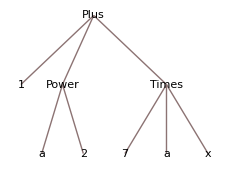

```mathematica
Clear[a];TreeForm[7a x+a^2+1]
```

Some usages of pattern as the secondary argument.

```mathematica
Trace[expr,f[___]](*show all calls to a particular function.*)
```

```mathematica
Trace[expr,i=_](*show assignments to i.*)
```

```mathematica
Trace[expr,_=_](*show all assignments during the evaluation of expr.*)
```

```mathematica
Trace[expr,Message[___]](*show messages generated during the evaluation of expr.*)
```

Trace wraps all expressions that appear in the list it produces with HoldForm to prevent them from being evaluated.

用 pattern 筛选所追踪 (或剔除) 的表达式后, 生成的结果中 List 的层级保持不变.

```mathematica
Trace[a=2;Do[a=a*a,{3}]]
```

{a=2;Do[a=a a,{3}],{a=2,2},{Do[a=a a,{3}],{{{a,2},{a,2},2 2,4},a=4,4},{{{a,4},{a,4},4 4,16},a=16,16},{{{a,16},{a,16},16 16,256},a=256,256},Null},Null}

```mathematica
Trace[a=2;Do[a=a*a,{3}],Times]
```

{{{{2 2,4}},{{4 4,16}},{{16 16,256}}}}

## TracePrint

```mathematica
TracePrint[expr](*prints all expressions used in the evaluation of expr.*)
```

TracePrint works essentially like Trace, except that it prints expressions immediately when it encounters them.

TracePrint indents its output in correspondence with the nesting levels for lists generated by Trace.

TracePrint does not support the TraceBackward option of Trace, since it outputs the traced results as evaluation goes.

## TraceDialog

```mathematica
TraceDialog[expr]
```

TraceDialog allows you to stop in the middle of a computation, and interact with the Mathematica environment that exists at that time. What TraceDialog does is to call Dialog on a sequence of expressions.

## TraceScan

```mathematica
TraceScan[f,expr]
```

Evaluation Stack

## Stack

```mathematica
Stack[](*shows the current evaluation stack, giving a list of the tags associated with evaluations that are currently being done.*)
Stack[pattern](*gives a list of expressions currently being evaluated which match the pattern.*)
```

Stack[_] shows all expressions currently being evaluated.

You can call Stack from inside a dialog to see how the dialog was reached.

In the list returned by Stack, each expression is wrapped with HoldForm.

由于 Stack 输出的是它所在位置当前的堆栈, 故一般情况下需要放在表达式的内部. 但这就导致 Stack 的输出值要么成为了被检测表达式的值的一部分, 要么没法输出. 因此运用 Stack 的有效方法是结合 Print 和 CompoundExpression, 即 Print[Stack[]];...

```mathematica
f[g[1,Print[Stack[]];2]]
```

{f,g,CompoundExpression,Print}

f[g[1,2]]

The expression that Mathematica most recently started to evaluate always appears as the last element of the evaluation stack.

## StackInhibit

```mathematica
StackInhibit[expr](*evaluates expr without modifying the evaluation stack.*)
```

当 StackInhibit 插入在一个表达式内部, 它会阻止 StackInhibit 以内 Stack 以外的所有 tags 的输出. 故它应出现在由于 Stack 的插入导致原表达式运算堆栈新增的 tag 外面.

```mathematica
f[g[h[Print[Stack[]]]]]
```

{f,g,h,Print}

f[g[h[Null]]]

```mathematica
f[g[h[StackInhibit[Print[Stack[]]]]]]
```

{f,g,h}

f[g[h[Null]]]

```mathematica
f[StackInhibit[g[h[Print[Stack[]]]]]]
```

{f}

f[g[h[Null]]]

Functions like TraceDialog automatically call StackInhibit each time they start a dialog. This means that Stack does not show functions that are called within the dialog, only those outside.

## StackBegin

```mathematica
StackBegin[expr](*evaluates expr, starting a fresh evaluation stack.*)
```

By using StackInhibit and StackBegin, you can control which parts of the evaluation process are recorded on the stack.

```mathematica
f[StackBegin[g[h[StackInhibit[Print[Stack[]]]]]]]
```

{g,h}

f[g[h[Null]]]

Functions like TraceDialog[expr,... ] call StackBegin before they begin evaluating expr,so that the stack shows how expr is evaluated, but not how TraceDialog was called.

## StackComplete

What StackComplete[expr] effectively does is to keep on the stack the complete evaluation chain for each expression that is currently being evaluated.

Messages

Although most messages associated with built-in functions are switched on by default, there are some which are switched off by default.

Messages are always stored as control string form which is suitable for use with StringForm,Message.

The expressions are wrapped with HoldForm to prevent evaluation.

$MessagePrePrint 用于预处理表达式, 然后再放入 Message 输出.

## MessageName(::)

```mathematica
symbol::tag(*a message name*)
MessageName[symbol,"tag"]
```

You can specify messages by defining values for symbol::tag.

```mathematica
a::fuck="fuck `1`";Message[a::fuck,you]
```

a::fuck: fuck you

Assignments for s::tag are stored in the Messages value of the symbol s.

The f::usage message is typically defined for functions intended for general use, giving a description of how to use the function.

?f prints out the message f::usage.

MessageName[symbol,"tag","lang"] or symbol::tag::lang represents a message in a particular language.

一次运算中, 同一个信息若反复生成多于 3 次, 会被阻止, 并输出 General::stop.

If a message of the form f::tag is not found, the general message General::tag will be used.

## Messages

```mathematica
Messages[symbol](*gives all the messages assigned to a particular symbol.*)
```

## On

## Off

## Quiet

```mathematica
Quiet[expr](*evaluates expr quietly, without actually outputting any messages generated.*)
```

evaluates expr quietly, without actually outputting any messages generated.

## $MessagePrePrint

a global variable whose value, if set, is applied to expressions before they are included in the text of messages.

```mathematica
Block[{$MessagePrePrint = Graphics[{Text[ToString[#],{0,0}],{Red,Circle[]}},ImageSize->30]&},Sin[1,2]]
```

Sin::argx: called with  arguments; 1 argument is expected.

Sin[1,2]

The default value of $MessagePrePrint is Automatic.

$MessagePrePrint is applied after each expression is wrapped with HoldForm.

## Message

```mathematica
Message[symbol::tag](*output message*)
Message[symbol::tag,e1,e2,...](*feed control string message with e1,e2,...*)
```

```mathematica
a::fuck="fuck `1`";Message[a::fuck,you]
```

a::fuck: fuck you

## $MessageList

a global variable that gives a list of the names of messages generated during the evaluation of the current input line.

Whenever a message is output, its name, wrapped with HoldForm to prevent evaluating, is appended to $MessageList.

With the standard Wolfram System main loop, $MessageList is reset to {} when the processing of a particular input line is complete.

```mathematica
Sin[a,b];$MessageList
```

Sin::argx: Sin called with 2 arguments; 1 argument is expected.

{Sin::argx}

```mathematica
$MessageList
```

{}

## MessageList

```mathematica
MessageList[n](*a global object assigned to be a list of the names of messages generated during the processing of the n^th input line. *)
```

Only messages that are actually output are included in the list MessageList[n].

每次 input line 运算结束后, $MessageList 的值赋给 MessageList[n].

The message names in the list are wrapped with HoldForm to prevent evaluating.

## Package Development

The context of newly loaded package will be added at the beginning of $ContextPath.

# Symbolic & Numeric Evaluation

## Mathematical Functions

Integer Functions

## Combinatorial Functions

### Factorial(!)

```mathematica
Factorial[n]
n!
```

n! is postfix form.

Attributes:

```mathematica
Attributes@Factorial
```

{Listable,NumericFunction,Protected}

For non-integer n, the numerical value of n! is given by Gamma[1+n].

For integers and half integers, Factorial automatically evaluates to exact values.

Arithmetic Functions

## Plus(+)

```mathematica
Plus[a,b,c]
a+b+c
```

Attributes of Plus:

```mathematica
Attributes@Plus
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

The default value for arguments of Plus, as used in x_. patterns, is 0.

Plus[] is 0, because the default argument is 0 and Plus is OneIdentity.

Plus[x] is x, because of OneIdentity.

x+0 evaluates to x, but x+0.0 is left unchanged. It is because the former evaluation is exact such that 0 certainly has no effect on the result of evaluation, whereas the latter is based on MachinePrecision which is inexact and involves uncertainty.

Unlike other functions, Plus applies built-in rules before user-defined ones.

## Minus(-)

```mathematica
Minus[x]
-x
```

-x is converted to (-1)*x on input.

## Subtract(-)

```mathematica
Subtract[a,b]
a-b
```

Subtract is defined by Plus and Times. Thus the internal FullForm of Subtract[a,b] is always Plus[a,Times[-1,b]]. And the operator form  a-b is converted to a+(-1*b)  on input.

```mathematica
Subtract[a,b]//FullForm
```

Plus[a,Times[-1,b]]

## Times(×, ,*)

```mathematica
Times[a,b,c]
a b c
```

Attributes of Times:

```mathematica
Attributes@Times
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

The default value for arguments of Times, as used in x_. patterns, is 1.

Times[] is 1.

Times[x] is x.

Unlike other functions, Times applies built-in rules before user-defined ones.

## Divide(/,÷)

```mathematica
Divide[a,b]
a/b
```

Divide is defined on Times and Power. Divide[a,b] has internal FullForm of Times[a,Power[b,-1]].

```mathematica
Divide[a,b]//FullForm
```

Times[a,Power[b,-1]]

The operator form a/b is converted to a b^-1 on input.

## Power(^)

```mathematica
Power[a,b]
a^b
```

Attributes:

```mathematica
Attributes@Power
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Power[2]
```

2

Power[x,y,z,…] is taken to be Power[x,Power[y,z,…]].

```mathematica
Power[a,b,c]
```

a^(b^c)

## Sqrt(√)

```mathematica
Sqrt[x]
√x
```

Attributes:

```mathematica
Attributes@Sqrt
```

{Listable,NumericFunction,Protected}

Sqrt[x] is defined by Power[x,1/2]. The internal FullForm of Sqrt[x] is Power[x,Rational[1,2]].

```mathematica
Sqrt[x]//FullForm
```

Power[x,Rational[1,2]]

```mathematica
Sqrt[x]/.Sqrt->Identity
```

√x

```mathematica
ReleaseHold[HoldForm[Sqrt[x]]/.Sqrt->Identity]
```

x

Numerical Functions

## Round

```mathematica
Round[x] (*give the integer closest to x*)
```

## Sign

## UnitStep

```mathematica
UnitStep[x](*evaluated to be 0 for any x<0, and 1 for any x≥0*)
UnitStep[x1,x2,...](*to be 1 only if none of the Subscript[x, i] are negative.*)
```

UnitStep is Listable,Orderless,NumericFunction.

```mathematica
Attributes@UnitStep
```

{Listable,NumericFunction,Orderless,Protected}

注意 Listable 的意义:

```mathematica
UnitStep[1]
UnitStep[1,2,3]
UnitStep[{1,2,3}]
UnitStep[{1,2,3},{-1,2,-3}]
UnitStep[{{1,2,3},{-1,2,-3}}]
```

1

1

{1,1,1}

{0,1,0}

{{1,1,1},{0,1,0}}

## SquareWave

```mathematica
SquareWave[x](*amplitude: -1,+1; period: 1*)
SquareWave[{Subscript[y, 1],Subscript[y, 2]},x](*amplitude y1,y2; period: 1*)
```

Random Numbers

## RandomReal

```mathematica
RandomReal[](*0--1*)
RandomReal[{Subscript[x, min],Subscript[x, max]}](*from min to max*)
RandomReal[Subscript[x, max]](*from 0 to max*)
RandomReal[...,n](*a list of n pseudorandom real numbers*)
RandomReal[...,{n1,n2,...}](*a n1×n2×... list*)
```

## Numerical Evaluation & Precision

Display of Numbers

The forms are wrappers.

## ScientificForm

## EngineeringForm

## AccountingForm

## NumberForm

## BaseForm

```mathematica
BaseForm[expr,n](*display exper in base n.*)
```

The maximum allowed base is 36. For bases larger than 10, additional digits are chosen from the letters a–z.

You can enter a number in an arbitrary base using base^^digits.

```mathematica
2^^101
```

5

```mathematica
BaseForm[5,2]
```

101_2

Precision & Accuracy Control

Mathematica will usually produce exact results unless you tell it otherwise.

Exact results are displayed in their entirety when possible or symbolically when full display would be impossible due to the infinity of the exact representation.

For most purposes, treat precision as the total number of digits in the decimal representation of a number and accuracy as the total number of digits after the decimal. As such, precision is a measure of relative uncertainty (given a precision p a larger number will have more uncertainty than a smaller number). Accuracy is an absolute measure of uncertainty because the number of places after the decimal is independent of the magnitude of the number.

## N

```mathematica
N[expr]
N[expr,n]
N[expr,{precision,accuracy}]
```

Unless numbers in expr are exact, or of sufficiently high precision, N[expr,n] may not be able to give results with n-digit precision.

N[expr,n] may internally do computations to more than n digits of precision.

Precision n need not be an integer. Which I have no idea.

```mathematica
Manipulate[Column[{N[√2,x],N[√2,10]}],{x,0.,10.,0.01}]
```

```mathematica
Table[N[2^i,16],{i,1,15,2}]//TableForm
```

2.
8.
32.
128.
512.
2048.
8192.
32768.

```mathematica
Table[N[2^i,{16,10}],{i,1,15,2}]//TableForm
```

2.
8.
32.
128.
512.
2048.
8192.
32768.

## Precision

### Precision

```mathematica
Precision[x]
```

a measure of the relative uncertainty in the value of x.

Numbers entered in the form digits`p are taken to have precision p.

Without backtick mark `, approximate number with (about) 16 digits or less are taken to be MachinePrecision; approximate number with digits more that are taken to be arbitrary-precision specified by its form.

Numbers entered in the form digits` are taken to have precision MachinePrecision.

### SetPrecision

```mathematica
SetPrecision[expr,p]
(*yields a version of expr in which all numbers have been set to have precision p.*)
```

When SetPrecision is used to increase the precision of a number, the number is padded with zeros. The zeros are taken to be in base 2. In base 10, the additional digits are usually not zeros.

SetPrecision returns an arbitrary-precision number. For p==MachinePrecision, SetPrecision returns MachinePrecision number.`

If expr contains machine-precision numbers, SetPrecision[expr,p] can give results that differ from one computer system to another.

SetPrecision[expr,p] does not modify expr itself.

## Accuracy

## Machine Numbers

### MachinePrecision

MachinePrecision is the symbolic representation of $MachinePrecision. It is treated as a numeric constant, with attribute Constant.

Approximate numeric results are represented in machine precision floating point by default.

Approximate real numbers are assumed to have precision specified by MachinePrecision if fewer than $MachinePrecision explicit digits are entered.

A integer followed by a decimal point, e.g., 1., forces to treat the number as (machine-precision) floating point number.

### $MachinePrecision

The number of decimal digits of precision used for machine-precision numbers.

A typical value of $MachinePrecision is 53Log[10,2] or approximately 16. This corresponds to double-precision floating point number, and 64 bits in memory.

$MachinePrecision is the machine precision approximation to MachinePrecision:

### MachineNumberQ

```mathematica
MachineNumberQ[expr](*check if expr is machine-precision Real or Complex number.*)
```

## Formula Manipulation

General Expansions

Extracting Parts of Formulas

## Coefficient

```mathematica
Coefficient[expr,form]
Coefficient[expr,form,n](*coefficient of form^n*)
```

Coefficient[expr,form,0] picks out terms that are not proportional to form.

Coefficient works whether or not expr is explicitly given in expanded form.

Assumptions & Domains

## make assumptions

### Assuming

### $Assumptions

## formal logic

### Element(∈)

### ForAll(∀)

### Exists(∃)

## Domains

### Integers

### Rationals

### Reals

### Complexes

### Booleans

### Primes

### Algebraics

In mathematics, an algebraic number is a number that is a root of a non-zero polynomial in one variable with rational coefficients (or equivalently — by clearing denominators — with integer coefficients).

## Calculus

Vector Analysis

## Vector Calculus

### Grad

```mathematica
Grad[f,{x1,x2,...,xn}](*the gradient (∂f/∂Subscript[x, 1],…,∂f/∂Subscript[x, n]).*)
Grad[f,{{x1,x2,...,xn}},chart](*in the specified coordinate system.*)
∇_{x,y,z} f
```

ESC del ESC, or ESC grad ESC.

### Div

```mathematica
Div[{f1,f2,...,fn},{x1,x2,...,xn}](*the divergence ∂Subscript[f, 1]/∂Subscript[x, 1]+…+∂Subscript[f, n]/∂Subscript[x, n]*)
Div[{f1,f2,...,fn},{x1,x2,...,xn},chart]
∇_{x,y,z} .f
```

ESC del ESC . , or ESC del. ESC .

### Curl

```mathematica
Curl[{f1,f2},{x1,x2}](*two-dimensional curl ∂Subscript[f, 2]/∂Subscript[x, 1]-∂Subscript[f, 1]/∂Subscript[x, 2]*)
Curl[{f1,f2,f3},{x1,x2,x3}] (*three-dimensional curl (∂Subscript[f, 3]/∂Subscript[x, 2]-∂Subscript[f, 2]/∂Subscript[x, 3],∂Subscript[f, 1]/∂Subscript[x, 3]-∂Subscript[f, 3]/∂Subscript[x, 1],∂Subscript[f, 2]/∂Subscript[x, 1]-∂Subscript[f, 1]/∂Subscript[x, 2])*)
Curl[...,...,chart]
∇_{x,y,z} ×f
```

ESC delx ESC.

### Laplacian

```mathematica
Laplacian[f,{x1,x2,...,xn}]
Laplacian[...,...,chart]
∇_{x,y,z}^2 f
```

ESC del2 ESC.

## Coordinate Systems

### CoordinateTransform

### TransformedField

### CoordinateChartData

### CoordinateTransformData

## Visualization

Integral Transforms

## Fourier Series

### FourierSeries

```mathematica
FourierSeries[expr,t,n]
```

# Higher Mathematical Computations

## Number Theory

Number Representations

## Continued Fractions

## Rational Approximations

### Rationalize

```mathematica
Rationalize[x]
```

converts an approximate number x to a nearby rational with small denominator.

Additive Number Theory

## Integer Partitions

### IntegerPartitions

# Visualization & Graphics

## Symbolic Graphics Language

Types of Graphics Objects

## Graphics

```mathematica
Graphics[primitives,options](*represents a two-dimensional graphical image.*)
```

Graphics is displayed in StandardForm as a graphical image. In InputForm it is displayed as an explicit list of primitives.

## Graphics3D

```mathematica
Graphics3D[primitives,options]
```

Graphics Primitives

许多三维 primitive object 实际上是更高维(及更低维)相应物体的一般形式, 不仅限于三维.

## Point

### Point

```mathematica
Point[p]
Point[{p1,p2,...}]
```

Available options: VertexColors,VertexNormals.

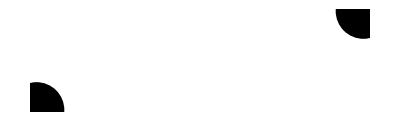

```mathematica
Graphics[{PointSize[0.1],Point[RandomReal[{1,3},{2,2}],VertexColors->{Red, Green}]}]
```

## Line

### Line

```mathematica
Line[{p1,p2,...}](*one line*)(*2 level list*)
Line[{{p1,p2,...},...}](*collection of lines*)(*3 level list*)
```

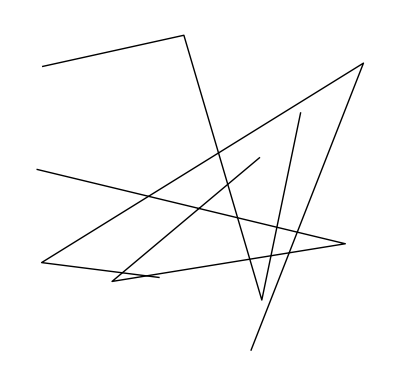

```mathematica
Graphics[Line[RandomReal[{1,3},{3,4,2}]]]
```

Available options: VertexColors,VertexNormals.

### HalfLine

```mathematica
HalfLine[{p1,p2}](*a ray starting at p1, through p2.*)
HalfLine[p,vec](*starting at p, in the direction vec.*)
```

### InfiniteLine

```mathematica
InfiniteLine[{p1,p2}]
InfiniteLine[p1,vec]
```

### BezierCurve

```mathematica
BezierCurve[{p1,p2,...}]
```

BezierCurve by default represents a composite cubic Bézier curve.

SplineDegree->d specifies that the underlying polynomial basis should have maximal degree d.

With SplineDegree->d, BezierCurve with d+1 control points yields a simple degree-d Bézier curve. With fewer control points, a lower-degree curve is generated. With more control points, a composite Bézier curve is generated.

一条 Bezier curve 的控制点数比生成它的多项式次数多一个. 当点数多于一条曲线所需数目时, 第一条曲线的终点成为第二条曲线的起点.

### BSplineCurve

```mathematica
BSplineCurve[{p1,p2,...}](*a graphics primitive that represents a nonuniform rational B-spline curve with control points Subscript[pt, i].*)
```

nonuniform rational B-spline (NURBS) curve.

### JoinedCurve

## Arrow

### Arrow

## Triangle & Polygon

### Triangle

```mathematica
Triangle[{p1,p2,p3}]
Triangle[{{p1,p2,p3},...}](*a collection of triangles.*)
```

### Polygon

```mathematica
Polygon[{Subscript[pt, 1],Subscript[pt, 2],...}](*a graphics primitive that represents a filled polygon*)
Polygon[{{Subscript[pt, 11],Subscript[pt, 12],...},{Subscript[pt, 21],Subscript[pt, 22],...},...}](*represents a collection of polygons*)
```

Polygon can be used both in Graphics and Graphics3D .

The boundary of a polygon is formed by joining the last point you specify to the first one.

Polygons in 2D and 3D can be non-convex, and can intersect themselves. Self-intersecting polygons are filled according to an even-odd rule that alternates between filling and not filling at each crossing.

### SSSTriangle

```mathematica
SSSTriangle[a,b,c]
```

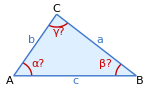

SSSTriangle returns a Triangle with A at the origin, B on the positive x axis, and C in the half-plane y>0.

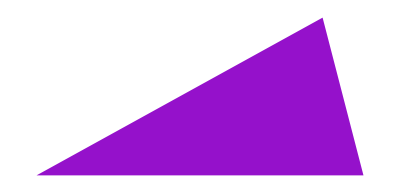

```mathematica
Graphics@{RandomColor[],SSSTriangle[1,2,2]}
```

### SASTriangle

```mathematica
SASTriangle[a,γ,b]
```

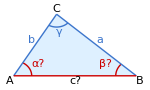

### ASATriangle

```mathematica
ASATriangle[α,c,β]
```

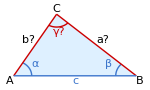

### AASTriangle

```mathematica
AASTriangle[α,β,a]
```

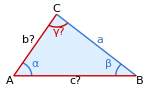

## Circle & Ellipse

### Circle

```mathematica
Circle[{x,y},r]
Circle[{x,y}]
Circle[{x,y},{Subscript[r, x],Subscript[r, y]}]
Circle[...,{Subscript[θ, 1],Subscript[θ, 2]}]
```

Circle[] is equivalent to Circle[{0,0}].

### Disk

Similar to Circle.

## Rectangle & Parallelogram

### Rectangle

```mathematica
Rectangle[{Subscript[x, min],Subscript[y, min]},{Subscript[x, max],Subscript[y, max]}]
Rectangle[{Subscript[x, min],Subscript[y, min]}](*square unit rectangle*)
```

#### Option: RoundingRadius

### Parallelogram

```mathematica
Parallelogram[p,{v1,v2}](*a parallelogram with origin p and directions Subscript[v, 1] and Subscript[v, 2].*)
```

Parallelogram[] means Parallelogram[{0,0},{{1,0},{1,1}}]

v1,v2 不仅仅是方向, 也是边长.

## Plane

### HalfPlane

```mathematica
HalfPlane[{p1,p2},w](*the half-plane bounded by the line through Subscript[p, 1] and Subscript[p, 2] and extended in the direction w.*)
HalfPlane[p,v,w](*the half-plane bounded by the line through Subscript[p, 1] and Subscript[p, 2] and extended in the direction w.*)
```

### InfinitePlane

```mathematica
InfinitePlane[{p1,p2,p3}](*the plane passing through the points Subscript[p, 1], Subscript[p, 2], and Subscript[p, 3].*)
InfinitePlane[p,{v1,v2}](*the plane passing through the point p in the directions Subscript[v, 1] and Subscript[v, 2].*)
```

## fill arbitrary curves

### FilledCurve

## graphics with shared vertices

### GraphicsComplex

```mathematica
GraphicsComplex[{p1,p2,...},data]
```

GraphicsComplex[{pt_1,pt_2,…},data] effectively replaces integers i that appear as coordinates in data by the corresponding pt_i.

data can be any nested list of graphics primitives and directives.

Normal[GraphicsComplex[pts,data]] substitutes coordinates to give an ordinary list of graphics primitives and directives.

## Polyhedrons

### Tetrahedron

```mathematica
Tetrahedron[{p1,p2,p3,p4}]
Tetrahedron[{{p1,p2,p3,p4},...}](*a collection*)
```

任意四面体

Tetrahedron[] means Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}]

```mathematica
Graphics3D[Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}},VertexColors->{Yellow, Blue, Green,Red}]]
```

-Graphics3D-

### Cuboid

```mathematica
Cuboid[Subscript[p, min]](*a unit hypercube with its lower corner at Subscript[p, min].*)
Cuboid[Subscript[p, min],Subscript[p, max]](*an axis-aligned filled cuboid with lower corner Subscript[p, min] and upper corner Subscript[p, max].*)
```

立方体

立方体的内禀条件以及 axis-aligned 条件使得只需两个点即可确定这个立方体.

Cuboid 可用于从二维起, 各个维度的 hypercube.



```mathematica
Cuboid[{0,0}]//Graphics
```

### Parallelepiped

```mathematica
Parallelepiped[p,{v1,v2,...}](*a parallelepiped with origin p and directions Subscript[v, i].*)
```

平行六面体

### Hexahedron

```mathematica
Hexahedron[{p1,p2,...,p8}]
Hexahedron[{p1,p2,...,p8},...](*a collection of hexahedra*)
```

任意六面体

Hexahedron[] means 单位正立方体.

```mathematica
Graphics3D@Hexahedron[]
```

-Graphics3D-

### Prism

```mathematica
Prism[{p1,p2,...,p6}](*a filled prism connecting the triangles {Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]} and {Subscript[p, 4],Subscript[p, 5],Subscript[p, 6]}.*)
```

任意三棱柱

### Pyramid

```mathematica
Pyramid[{p1,p2,...,p5}](*a filled pyramid with base {Subscript[p, 1],…,Subscript[p, 4]} and top Subscript[p, 5].*)
```

任意四棱锥

### Simplex

```mathematica
Simplex[{p1,...,pk}](*the simplex spanned by points Subscript[p, i].*)
```

任意单形体

Simplex[n] for integer n is equivalent to Simplex[{{0,…,0},{1,0,…,0},…,{0,…,0,1}}], the unit standard simplex in ℝ^n.

## Curved Surface Objects

### Sphere

```mathematica
Sphere[p](*unit sphere at p*)
Sphere[p,r](*a sphere of radius r*)
Sphere[{p1,p2,...},r](*a collection of spheres of radius r*)
Sphere[{p1,p2,...},{r1,r2,...}](*a collection of spheres of ri and at pi, respectively.*)
```

Sphere[] means Sphere[{0,0,0}].

Sphere[n] for positive integer n is equivalent to Sphere[{0,…,0}], a unit sphere in ℝ^n.

```mathematica
Graphics3D@Sphere[RandomInteger[100,{5,3}],{5,10,15,20,25}]
```

-Graphics3D-

### Circumsphere

```mathematica
Circumsphere[{Subscript[p, 1],...,Subscript[p, n+1]}](*a sphere that passes through the points Subscript[p, i] of length n.*)
```

二维平面上不共线 3 点确定一个圆, 三维空间中不共面 4 点确定一个球体. 所以要注意点数和维数是有要求的.

### Ball

```mathematica
Ball[p]
Ball[p,r]
Ball[{p1,p2,...},r]
Ball[{p1,p2,...},{r1,r2,...}]
```

Ball[] means Ball[{0,0,0}].

Ball[n] for integer n is equivalent to Ball[{0,…,0}], a unit ball in ℝ^n.

### Ellipsoid

```mathematica
Ellipsoid[p,{r1,r2,...}](*an axis-aligned ellipsoid centered at the point p and with semiaxes lengths Subscript[r, i].*)
Ellipsoid[p,Σ](*an ellipsoid centered at p and weight matrix Σ.*)
```

### Cylinder

```mathematica
Cylinder[](*{{0,0,-1},{0,0,1}}*)
Cylinder[{p1,p2},r](*a cylinder of radius r around the line from p1 to p2.*)
Cylinder[{p1,p2}](*radius 1*)
Cylinder[{{p1,p2},...},{r1,...}](*a collection of cylinder.*)
```

### Cone

```mathematica
Cone[](*{{0,0,-1},{0,0,1}}*)
Cone[{p1,p2},r](*a cone with a base of radius r centered at p1 and a tip at p2.*)
Cone[{p1,p2}](*radius 1*)
Cone[{{p1,p2},...},{r1,...}](*a collection*)
```

### Tube

```mathematica
Tube[{p1,p2,...}](*a 3D tube around the line joining a sequence of points.*)
Tube[{p1,p2,...},r]
Tube[{p1,p2,...},{r1,r2,...}](*different radii at corresponding points.*)
Tube[{{p1,p2,...},...}](*a collection of tubes.*)
Tube[curve](*a tube around the specified 3D curve.*)
```

```mathematica
Graphics3D@Tube[{#,0,0}&/@Range[11],Sin/@Range[0,π,0.1π]]
```

-Graphics3D-

### BSplineSurface

```mathematica
BSplineSurface[array](*a nonuniform rational B-spline surface defined by an array of x,y,z control points.*)
```

By default, BSplineSurface uses bicubic splines, corresponding to degree {3,3}.

By default, knots are chosen to be uniform and to make the surface reach the control points at the edges of the array.

## Raster

### Raster

```mathematica
Raster[{{a11,a12,...},...}](*array of gray levels*)
Raster[{{{r11,g11,b11},...},...}](*array of RGB colors*)
Raster[{{{r11,g11,b11,opa11},...},...}](*RGB with opacity*)
Raster[{{{a11,opa11},...},...}](*gray levels with opacity*)
```

Raster[...,ColorFunction→f] specifies that each cell should be colored using the graphics directives obtained by applying the function f to the value specified for that cell.

If array has dimensions {n,m}, then Raster[array] is assumed to occupy the rectangle Rectangle[{0,0},{m,n}].

Raster[array,{{x_min,y_min},{x_max,y_max}}] specifies that the raster should be taken instead to fill the rectangle Rectangle[{x_min,y_min},{x_max,y_max}].

### Raster3D

```mathematica
Raster3D[{{{a111,a112,...},...},...}](*a cubical array of gray cells. *)
Raster3D[{{{{r111,g111,b111},...},...},...}](*RGB color cells.*)
Raster3D[{{{{r111,g111,b111,α111}}}}](*opacity*)
Raster3D[array,{p1,p2}](*cube from lower corner p1 to upper corner p2.*)
```

## Text

### Text

```mathematica
Text[expr]
Text[expr,coords]
Text[expr,coords,offset]
Text[expr,coords,offset,dir]
```

Unless you explicitly specify a style or font using Style, the text will be given in the graphic’s base style.

Offset is very useful.

Offset for the block of text relative to the coordinates given. Giving an offset {sdx,sdy} specifies that the point {x,y} should lie at relative coordinates {sdx,sdy} within the bounding rectangle that encloses the text. Each relative coordinate runs from -1 to +1 across the bounding rectangle.

The offsets specified need not be in the range -1 to +1.

## Inset graphics

### Inset

```mathematica
Inset[obj](*represents an object obj inset in a graphic.*)
Inset[obj,pos](*the inset should be placed at position pos in the graphic.*)
Inset[obj,pos,opos](*aligns the inset so that position opos in the object lies at position pos in the enclosing graphic. *)
Inset[obj,pos,ops,size](*specifies the size of the inset in the coordinate system of the enclosing graphic.*)
Inset[obj,pos,opos,size,dirs](*specifies that the axes of the inset should be oriented in directions dirs. *)
```

Inset can be used in both Graphics and Graphics3D.

Any expression can be inset.

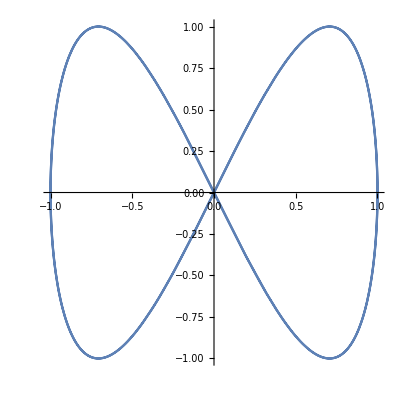

```mathematica
plot=Plot[{Sin[x],Sin[2x]},{x,0,2π},ImageSize->200,Frame->True,Background->LightYellow];

ParametricPlot[{Sin[x],Sin[2x]},{x,0,4π},Epilog->Inset[plot,{.3,-.5},Center,ImageScaled[0.4],{{0.5,0.5},{-0.5,1}}]]
```

Graphics Directives

you can insert into the list of graphics primitives certain graphics directives, which modify the subsequent graphical elements in the list. In this way, you can specify how a particular set of graphical elements should be rendered.

In general, the graphical elements in a particular graphics object can be given in a collection of nested lists. When you insert graphics directives in this kind of structure, the rule is that a particular graphics directive affects all subsequent elements of the list it is in, together with all elements of sublists that may occur. The graphics directive does not, however, have any effect outside the list it is in.

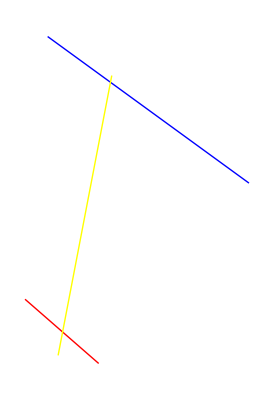

```mathematica
Graphics@({Blue,Line[n],{Yellow,{Red,Line[n]},Line[n]}}/.n:>RandomReal[1,{2,2}])
```

Graphics directives which require a numerical size specification can also accept values of  Tiny,Small,Medium,Large. For each directive, these values have been fine-tuned to produce an appearance which will seem appropriate to the human eye. (因此它们必须是绝对的尺寸.)

## Point

### PointSize

```mathematica
PointSize[d](*The diameter d is given as a fraction of the total width of the plot.*)
```

The following symbolic forms for d can be used: Tiny, Small, Medium, and Large. These specify absolute point sizes independent of the total width of the graphic.

### AbsolutePointSize

```mathematica
AbsolutePointSize[d]
```

The absolute diameter is measured in units of printer’s points, equal before magnification to 1/72 of an inch.

The following symbolic forms for d can be used: Tiny, Small, Medium, and Large.

## Line

### Thickness

```mathematica
Thickness[r](* The thickness r is given as a fraction of the horizontal plot range. *)
```

The following symbolic forms for r can be used: Tiny,Small,Medium,Large. These specify absolute thicknesses independent of the overall size of the graphic.

### AbsoluteThickness

```mathematica
AbsoluteThickness[r]
```

The absolute thickness is measured in units of printer’s points, equal before magnification to 1/72 of an inch.

The following symbolic forms for d can be used: Tiny,Small,Medium,Large.

### Dashing

```mathematica
Dashing[{r1,r2,...}](*a two-dimensional graphics directive specifying that lines that follow are to be drawn dashed,
                      with successive segments of lengths Subscript[r, 1], Subscript[r, 2], … (repeated cyclically).
                      The Subscript[r, i] are given as a fraction of the total width of the graph.*)
Dashing[r](*equivalent to Dashing[{r,r}]*)
```

第一段画出长度为 r1, 第二段不画出长度为 r2, 以此类推.

```mathematica
Graphics[{Dashing[{0.01,0.05,0.05,0.05}],Line[{{-1,-1},{1,1}}]}]
```

-Graphics-

r can be symbolic Tiny,Small,Medium,Large, which are independent of the total width of the graphic.

If a segment has a length r_i specified as 0, it is drawn as a dot whose diameter is the thickness of the line.

Dashing[{}] gives no dashing.

### AbsoluteDashing

```mathematica
AbsoluteDashing[{r1,r2,...}]
AbsoluteDashing[r]
```

The absolute lengths are measured in units of printer’s points, equal before magnification to 1/72 of an inch.

AbsoluteDashing 中长度都是绝对长度, 故缩放图形时 dashing 的宽度不变, 因此 dashing 的数量必须跟着改变.

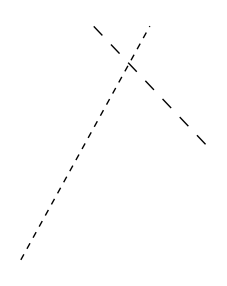

```mathematica
Graphics@{{Dashing[0.02],Line[RandomReal[1,{2,2}]]},{AbsoluteDashing[Medium],Line[RandomReal[1,{2,2}]]}}
```

### CapForm

```mathematica
CapForm[type](* a graphics directive that specifies what type of caps should be used 
                 at the ends of lines, tubes, and related primitives.*)
```

"Butt","Round""Square",None.

"Butt" specifies that lines end exactly at their endpoints. "Square" end caps extend one-half line width beyond the ends of a line. "Round" end caps are half-circles whose diameter is the width of the line.

In 2D, the default is "Square". In 3D, the default is "Round".

Applies to Line,Tube,Circle,Arrow.

### JoinForm

```mathematica
JoinForm[type](*a graphics directive that specifies what type of joins should be used 
                to connect segments of lines, tubes, edges, and related primitives.*)
```

## Color

### GrayLevel

```mathematica
GrayLevel[g]
GrayLevel[g,a](*with opacity*)
```

GrayLevel  represents shades of the gray color. 0 represents black and 1 represents white.

The gray level must be a number between 0 and 1.

If no opacity has been specified, GrayLevel[g] is equivalent to GrayLevel[g,1].

### RGBColor

```mathematica
RGBColor[r,g,b]
RGBColor[r,g,b,a](*with opacity*)
```

RGBColor is a color space defined by three additive primaries red, green, and blue, typically used in electronic display devices.

Red, green, and blue color intensities outside the range 0 to 1 will be clipped, as will opacities.

RGBColor[r,g,b,a] is equivalent to Directive[RGBColor[r,g,b],Opacity[α]].

If no opacity has been specified, RGBColor[r,g,b] is equivalent to RGBColor[r,g,b,1].

### Hue

```mathematica
Hue[h](*hue*)
Hue[h,s,b](*hue,saturation,brightness*)
Hue[h,s,b,a](*hue,saturation,brightness,opacity*)
```

Hue is so-called HSV or HSB.

Hue corresponds to a cylindrical transformation of RGBColor, typically used for color picking, allowing for easier interpretation of color parameters.

The parameters h, s, b, and a must all be between 0 and 1. Values of s, b, and a outside this range are clipped. Values of h outside this range are treated cyclically. »

As h varies from 0 to 1, the color corresponding to Hue[h] runs through red, yellow, green, cyan, blue, magenta, and back to red again. »

Hue[h] is equivalent to Hue[h,1,1].

Hue[h,s,b,a] is equivalent to Directive[Hue[h,s,b],Opacity[a]].

If no opacity has been specified, Hue[h,s,b] is equivalent to Hue[h,s,b,1].

### CMYKColor

### named colors

The Wolfram Language accepts the names of many colors directly as color specifications. These color names, such as Red, Gray, LightBlue, and Purple, are implemented as variables which evaluate to an RGBColor specification.

```mathematica
??LightGreen
```

LightGreen represents a light green color in graphics or style specifications.

Attributes[LightGreen]={Protected}
 
LightGreen=RGBColor[0.88,1,0.88]

## Arrow

### ArrowHeads

## Edge & Surface

### EdgeForm

```mathematica
EdgeForm[g](*a graphics directive which specifies that edges of polygons and other filled graphics objects 
             are to be drawn using the graphics directive or list of directives g. *)
```

EdgeForm[] draws no edges.

### FaceForm

```mathematica
FaceForm[g](*a graphics directive which specifies that faces of polygons and other filled graphics objects 
               are to be drawn using the graphics directive or list of directives g.*)
FaceForm[gfront,gback](*front and back, separately.*)
```

FaceForm[] draws no faces.

FaceForm[None,gback] specifies that front faces should not be drawn.

The front face of a polygon is defined to be the one for which the corners as you specify them are in counterclockwise order (right-hand rule).

### Texture

```mathematica
Texture[obj](*a graphics directive that specifies that obj should be used as a texture
               on faces of polygons and other filled graphics objects*)
```

obj can be an image.

obj can be one-, two-, three dimensional arrays of colors. Each color can be either a list of the form {r,g,b}, or a list of the form {r,g,b,a}.

### Opacity

```mathematica
Opacity[a]
```

a graphics directive which specifies that graphical objects which follow are to be displayed, if possible, with opacity a.

```mathematica
Opacity[a,color](*uses the specified color with opacity a.*)
```

Opacity runs from 0 to 1, with 0 representing perfect transparency.

Graphics that involve transparency may need to be printed as high-resolution bitmaps.

## Lighting Properties of Surface

Color, Specularity and Glow separately specify three kinds of light emission: diffuse reflection, specular reflection, and glow.

In diffuse reflection, light incident on a surface is scattered equally in all directions. When this kind of reflection occurs, a surface has a “dull” or “matte” appearance. Diffuse reflectors obey Lambert’s law of light reflection, which states that the intensity of reflected light is cos(α) times the intensity of the incident light, where α is the angle between the incident light direction and the surface normal vector. Note that when α>90^◦, there is no reflected light.

In specular reflection, a surface reflects light in a mirror-like way. As a result, the surface has a “shiny” or “gloss” appearance. With a perfect mirror, light incident at a particular angle is reflected at exactly the same angle. Most materials, however, scatter light to some extent, and so lead to reflected light that is distributed over a range of angles. The Wolfram Language allows you to specify how broad the distribution is by giving a specular exponent, defined according to the Phong lighting model. With specular exponent n, the intensity of light at an angle θ away from the mirror reflection direction is assumed to vary like cos(θ)^n. As n→∞, therefore, the surface behaves like a perfect mirror. As n decreases, however, the surface becomes less “shiny”, and for n==0, the surface is a completely diffuse reflector. Typical values of n for actual materials range from about 1 to several hundred.

Glow is light radiated from a surface at a certain color and intensity of light that is independent of incident light.

Most actual materials show a mixture of diffuse and specular reflection, and some objects glow in addition to reflecting light. For each kind of light emission, an object can have an intrinsic color. For diffuse reflection, when the incident light is white, the color of the reflected light is the material’s intrinsic color. When the incident light is not white, each color component in the reflected light is a product of the corresponding component in the incident light and in the intrinsic color of the material. Similarly, an object may have an intrinsic specular reflection color, which may be different from its diffuse reflection color, and the specularly reflected light is a component-wise product of the incident light and the intrinsic specular color. For glow, the color emitted is determined by intrinsic properties alone, with no dependence on incident light.

When you set up light sources and surface colors, it is important to make sure that the total intensity of light reflected from a particular polygon is never larger than 1. You will get strange effects if the intensity is larger than 1.

### color

the intrinsic color of a surface.

If you do not explicitly use these coloring directives, the Wolfram Language effectively assumes that all polygons have matte white surfaces. Thus the polygons reflect light of any color incident on them, and do so equally in all directions.

For materials that are effectively “white”, you can specify intrinsic colors of the form GrayLevel[a], where a is the reflectance or albedo of the surface.

### Glow

```mathematica
Glow[color]
```

a graphics directive which specifies that surfaces of 3D graphics objects that follow are to be taken to glow with color color.

```mathematica
Glow[](*specifies that there is no glow.*)
```

Glow[] is equivalent to Glow[Black] . This is because a “black light” consists of RGB color {0,0,0}, i.e. no light at all.

A surface can be specified as having an absolute color col by giving the combination of directives Glow[col], Black, and Specularity[0].

### Specularity

```mathematica
Specularity[s]
```

a graphics directive which specifies that surfaces of 3D graphics objects which follow are to be taken to have specularity s.

With specularity s, a surface is taken to specularly reflect a fraction s of light that falls on it from simulated light sources.

```mathematica
Specularity[s,n] (*uses specular exponent n.*)
```

The default specular exponent is 1.5. Higher values lead to more sharply defined reflections, typical of shinier materials. Values above 10 produce definite “specular highlights”.

```mathematica
Specularity[color]
```

Specularity[color] specifies that the RGB components of the incident light should be multiplied by the RGB components of col.

### Lighting

In a list of graphics primitives and directives, the alternative form {…,g,Lighting->spec,g,…} defines lighting for objects that follow the lighting specification in the list.

## Compound directive

### Directive

```mathematica
Directive[Subscript[g, 1],Subscript[g, 2],...]
```

represents a single graphics directive composed of the directives g_1, g_2, …

Any Directives supported by Graphics or Graphics3D can appear inside Directive .

Directive[{g_1,g_2,...}] is equivalent to Directive[g_1,g_2,...] .

Types of Coordinates

## original coordinates

## Scaled

## ImageScaled

The Structure of Graphics

Mathematica represents all graphics in terms of a collection of graphics primitives. The primitives are objects like Point, Line, and Polygon, which represent elements of a graphical image, as well as directives such as RGBColor and Thickness.

Each complete piece of graphics in Mathematica  is represented as a graphics object. Each kind of graphics object has a definite head that identifies its type.

Combining Graphics

## Show

```mathematica
Show[g,opts](*shows graphics with the specified options added. *)
Show[g1,g2,...]
```

Options explicitly specified in Show override those included in the graphics expression.

FullGraphics

## FullGraphics

```mathematica
FullGraphics[g](*takes a graphics object, and generates a new one
                 in which objects specified by graphics options are given as explicit lists of graphics primitives.*)
```

FullGraphics[g] should display the same as g, though it may have a different internal structure.

Rasterize & Magnify

## Rasterize

```mathematica
Rasterize[g]
Rasterize[g,"elem"]
```

g can be any expression, not only graphics.

Rasterize[g] is equivalent to Rasterize[g,"Graphics"], displays in a notebook in a way that approximates the unrasterized display of g, with the same image size.

Rasterize[g] therefore is a Graphics object with Raster primitive.

## Magnify

## Graphics Options & Styling

Plotting Options

## Main Styling Elements

### PlotStyle

an option for plotting and related functions that specifies styles in which objects are to be drawn.

PlotStyle->g specifies that a graphics directive g should be used to draw all the main objects in a plot.

多个 Directives 需用 Directive 合成为一个 Directive, 才能给所有图形统一设置: PlotStyle→Directive[g_1,g_2,...]

PlotStyle->{g_1,g_2,…} specifies that successive directives g_i should be used cyclically for successive objects. 每个 g_i 可以是 a list of Directives, 也可以是一个通过 Directive 合成的一个 directive.

PlotStyle→None specifies that the main objects in a plot should not be drawn explicitly, though mesh and filling are not affected.

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25]
```

-Graphics3D-

## Filling

### Filling

an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces.

The following settings can be used:

注意不加括号时, 代表填充至某个值 v :

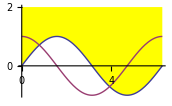

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{2,Yellow}},PlotRange->{-1,2}]
```

添加括号后, 则代表填充至某个 Graphics object:

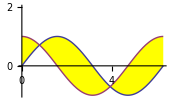

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{{2},Yellow}},PlotRange->{-1,2}]
```

可以设定填充方式与上下关系相关:

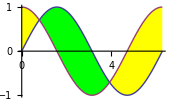

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{{2},{Yellow,Green}}}]
```

For 2D graphics, filling is done in the y direction.

For 3D graphics, filling is done in the z direction, and on the bounding xy plane.

In ListPlot, filling effectively draws a “stem” to every point.

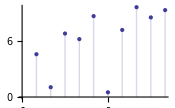

```mathematica
ListPlot[RandomReal[10,10],Filling->Axis]
```

For multiple curves, surfaces or lists of points, Filling->p is equivalent to Filling->{1->p,2->p…}.

### FillingStyle

an option for ListPlot, Plot, Plot3D, and related functions that specifies the default style of filling to be used.

FillingStyle->g specifies that all filling should be done by default with the specified graphics directive.

FillingStyle->{g_-,g_+} specifies that the filling should be done with g_- when a point, curve or surface lies below the object being filled to, and with g_+ when it lies above.

Settings of the form {i_k->{p_k,s_k},…} for Filling can be used to override the default style specified by FillingStyle.

## Legends

### PlotLegends

an option for plot functions that specifies what legends to use.

### ChartLegends

an option for charting functions that specifies what legends should be used for chart elements.

## Mesh Display

### Mesh

an option for Plot3D, DensityPlot, and other plotting functions that specifies what mesh should be drawn.

The following settings can be given for Mesh.

Mesh→Full 和 Mesh→All 的区别是, 前者只标出了基础采样数据点, 后者包含了生成图形过程中各个分析过程生成的所有数据点, 例如在分析基础数据的基础上生成的局部剖分点.

### MeshStyle

an option to specify the overall style for mesh.

MeshStyle->g specifies that a graphics directive g should be used to draw all mesh elements in a plot.

MeshStyle gives the style for mesh lines in functions that generate 3D graphics, and for mesh points in functions that generate 2D graphics.

MeshStyle->{g_1,g_2,…} specifies that successive directives g_i should be used cyclically to draw elements associated with successive mesh functions specified by MeshFunctions.

## Plotting Region

### PlotRange

The following settings can be used:

With the setting PlotRange->s, the following ranges are used:

### RegionFunction

an option for plotting functions that specifies the region to include in the plot drawn.

The setting RegionFunction->r specifies that a point should be included in the region when r[args] yields True.

The arguments supplied to function r are as follows:

注意以下两个例子中 pure function 的设置方式. 它们的变量设置需要与画图函数提供的变量数目和顺序相匹配.

```mathematica
SphericalPlot3D[1+Sin[5θ]Sin[5ϕ]/5,{θ,0,Pi},{ϕ,0,2Pi},Mesh->None,RegionFunction->Function[{x,y,z,u,v,w},w>0.95],Boxed->False,Axes->False,PlotStyle->FaceForm[Orange,Yellow]]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5θ]Sin[5ϕ]/5,{θ,0,Pi},{ϕ,0,2Pi},Mesh->None,RegionFunction->(#6>0.95&),Boxed->False,Axes->False,PlotStyle->FaceForm[Orange,Yellow]]
```

-Graphics3D-

The boundary of regions defined by RegionFunction is drawn with a style specified by the setting for BoundaryStyle .

## Coloring

### ColorFunction

The function specified by ColorFunction must return color directives such as RGBColor and Hue or named colors such as Red and Blue.

It can also return Opacity, as well as Glow and Specularity.

## Sampling & Adaptivity

### PlotPoints

an option for plotting functions that specifies how many initial sample points to use.

With a single variable, PlotPoints->n specifies the total number of initial sample points to use.

With more than one variable, PlotPoints->n specifies that n initial points should be used in each direction.

PlotPoints->{n_1,n_2,…} specifies different numbers of initial sample points for each successive direction.

The initial sample points are usually equally spaced.

### MaxRecursion

an option for functions like NIntegrate and Plot that specifies how many recursive subdivisions can be made.

MaxRecursion 控制在基本剖分的基础上最多可以进行多少子剖分. 也就是在基本样本点的基础上, 在一些局部区域再更细致地取样点.

Recursive subdivision is done only in those places where more samples seem to be needed in order to achieve results with a certain level of quality.

In d dimensions, each recursive subdivision increases the number of samples taken by a factor that increases roughly exponentially with d.

MaxRecursion→Infinity specifies no limit on the number of recursive subdivisions.

MaxRecursion 控制的局部剖分是基于 PlotPoints 生成的基础图形数据来进行的. 是否在一个区域进行局部剖分, 是依靠分析由 PlotPoints 生成的数据是否满足误差要求来决定的. 因此 MaxRecursion 不能代替 PlotPoints . 如果基础数据细致程度不够, 以至于察觉不到误差的存在, 即使设置很大的 MaxRecursion 也不能改变结果的不准确性. 例如:

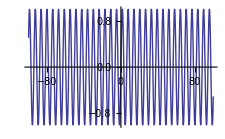

```mathematica
Plot[Sin[x],{x,-100,100}] (*Standard result*)
```

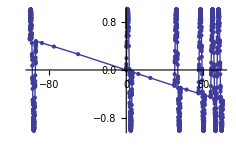

```mathematica
Plot[Sin[x],{x,-100,100},PlotPoints->2,MaxRecursion->15,Mesh->All]
```

由于 PlotPoints 太少, MaxRecursion 根本察觉不到数据点之间可能存在的导数变化.

Graphics Shape & Size

## AspectRatio

an option for changing the shape of final display area of graphics.

For two-dimensional graphics, AspectRatio is set by default to Automatic. This determines the aspect ratio from the original coordinate system used in the plot instead of setting it at a fixed value. One unit in the x direction in the original coordinate system corresponds to the same distance in the final display as one unit in the y direction. In this way, objects that you define in the original coordinate system are displayed with their “natural shape”.

```mathematica
Graphics3D[{Sphere[]},AspectRatio->1/2]
```

-Graphics3D-

## BoxRatios

## SphericalRegion

specifies whether the final image should be scaled so that a sphere drawn around the three-dimensional bounding box would fit in the display area specified.

The center of the sphere is taken to be at the center of the bounding box. The radius of the sphere is chosen so that the bounding box just fits within the sphere.

When set True, the image of a particular object remains consistent in size, regardless of the orientation of the object.

Annotation & Appearance

## Axes

### Axes

an option for graphics functions that specifies whether axes should be drawn.

Axes→True draws all axes.

Axes→False draws no axes.

Axes→{True/False,True/False,...} toggles individual axis.

### AxesStyle

an option for graphics functions that specifies how axes should be rendered.

AxesStyle→style specifies that all axes be rendered using Graphics directive style. The style can be a single directive or a combined Directive object.

AxesStyle→{xstyle,ystyle,...} specifies different directives for each axis. Each directive can be a single directive or a Directive object or a list of directives.

AxesStyle gives both the style of the axes themselves, and the default style for labels and ticks.

The default style of axis is specified by the DefaultAxesStyle option.

### AxesOrigin

an option for graphics functions that specifies where any axes drawn should cross.

AxesOrigin→{x,y} and AxesOrigin→{x,y,z} for 2D and 3D graphics, respectively.

In 2D graphics, AxesOrigin→Automatic uses an internal algorithm to determine where the axes should cross. If the point {0,0} is within, or close to, the plotting region, then it is usually chosen as the axes origin.

In contour and density plots, AxesOrigin→Automatic puts axes outside the plotting area.

In 3D graphics, AxesOrigin→Automatic puts axes on the outer box.

### AxesLabel

an option for graphics functions that specifies labels for axes.

Any expression can be specified as a label. It will be given by default in TraditionalForm. Arbitrary strings of text can be given as "text".

### AxesEdge

an option for three-dimensional graphics functions that specifies on which edges of the bounding box axes should be drawn.

AxesEdge->{{dir_y,dir_z},{dir_x,dir_z},{dir_x,dir_y}} specifies on which three edges of the bounding box axes are drawn. The dir_i must be either +1 or -1.

座标轴是两个垂直平面的交线. +1 和 -1 分别代表坐标值大的那个 box face 和坐标值小的那个 face.

Any pair of {dir_i,dir_j} can be replaced by Automatic or None.

If you explicitly specify on which edge to draw an axis, the axis will be drawn on that edge, whether or not the edge is exposed with the view point you have chosen.

## Ticks

### Ticks

an option for graphics functions that specifies tick marks for axes.

The following settings can be given for Ticks:

With the Automatic setting, tick marks are usually placed at points whose coordinates have the minimum number of digits in their decimal representation.

For each axis, the following tick mark options can be given:

If no explicit labels are given, the tick mark labels are given as the numerical values of the tick mark positions.

Any expression can be given as a tick mark label.

Scaled length 指的是 tick 的长度与它延伸的方向上图像长度的比值. Tick mark lengths are given as a fraction of the distance across the whole plot.

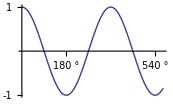

```mathematica
Plot[Cos[x],{x,0,10},Ticks->{{{Pi,180°,1},{2Pi,360°,1},{3Pi,540°,1}},{-1,1}}]
```

在座标轴的两侧, 可以用 scaled length 分别设置 tick 的长度.

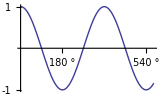

```mathematica
Plot[Cos[x],{x,0,10},Ticks->{{{Pi,180°,{0,.5}},{2Pi,360°,{.5,0}},{3Pi,540°,{0,.5}}},{-1,1}}]
```

Tick mark styles can involve any graphics directives.

TicksStyle gives default styles to use for tick marks and tick mark labels.

### TicksStyle

an option for graphics functions which specifies how ticks should be rendered.

TicksStyle gives styles for both tick marks and tick labels.

TicksStyle->style specifies that all ticks are to be rendered by default with the specified style.

TicksStyle->{xstyle,ystyle,…} specifies that ticks on different axes should use styles xstyle, ….

Style specifications can refer to styles using style names from current stylesheets.

Explicit styles specified in the setting for Ticks can override styles specified in TicksStyle.

## Frames

### Frame

True: draw frame around the whole object.
False: do not draw frame.
All: draw frames around each entry in Grid, etc.
{{left,right},{bottom,top}} specifies whether to draw a frame on each edge in graphics.

For Grid, complicated specs can be given.

### FrameStyle

### FrameLabel

### RotateLabel

an option for graphics and related functions that specifies whether labels on vertical frame axes should be rotated to be vertical.

### FrameTicks

### FrameTicksStyle

## Grid Lines

### GridLines

an option for two-dimensional graphics functions that specifies grid lines.

The following settings can be given for GridLines :

With the Automatic setting, grid lines are usually placed at points whose coordinates have the minimum number of digits in their decimal representation.

For each direction, the following grid line options can be given:

Grid line styles can involve any graphics directives, such as RGBColor and Thickness.

Styles should be specified in GridLines only if some grid lines have styles differing from the overall style set by GridLinesStyle. GridLinesStyle gives overall styles to use for grid lines. Individual gridline styles which are specified in GridLines option have higher priority over the general ones specified by GridLinesStyle.

### GridLinesStyle

an option for 2D graphics functions that specifies how grid lines should be rendered.

GridLinesStyle->style specifies that all grid lines should be rendered by default with the specified style.

GridLinesStyle->{xstyle,ystyle} specifies that x and y grid lines should use different styles.

Style specifications can refer to styles using style names from current stylesheets.

Explicit styles specified in the settings for GridLines can override styles specified in GridLinesStyle.

### FaceGrids

Grid lines on bounding box.

Faces are specified as {dir_x,dir_y,dir_z}, where two of the dir_i must be 0, and the third one must be +1 or -1.

+1,-1 代表相应的前后坐标平面.

## Labels

### PlotLabel

an option for graphics functions that specifies an overall label for a plot.

```mathematica
PlotLabel->None
PlotLabel->label
```

Any expression can be used as a label. It will be given by default in TraditionalForm .

```mathematica
ContourPlot3D[x^2+y^2==z^2,{x,-3,3},{y,-3,3},{z,-3,3},PlotLabel->x^2+y^2==z^2]
```

-Graphics3D-

Any possible form for the output of an expression can be used.

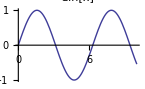

```mathematica
Plot[Sin[x],{x,0,10},PlotLabel->StandardForm[Sin[x]]]
```

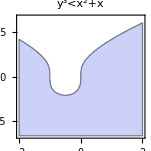

```mathematica
RegionPlot[y^3<x^2+x,{x,-2,2},{y,-2,2},PlotLabel->Style[Framed[y^3<x^2+x],16,Blue,Background->Lighter[Yellow]]]
```

An individual style for PlotLabel has higher priority over the overall style for labels specified with LabelStyle .

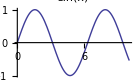

```mathematica
Plot[Sin[x],{x,0,10},PlotLabel->Style[Sin[x],Blue,20],LabelStyle->Directive[Orange,Italic]]
```

```mathematica
Dynamic[Plot[f[x],{x,0,10},PlotLabel->Row[{Style["f",Italic],"=",PopupMenu[Dynamic[f],{Sin,Cos,Tan,Sinc}]}]]]
```

由于 f 在 Dynamic 内部, 每次点击鼠标改变 Dynamic[f] 的值时都会赋值给 f, 随后大的 Dynamic object 发现其内部有一些量的值已经改变, 从而会自动重新计算输出结果.

### LabelStyle

an option for formatting and related constructs that specifies the style to use in displaying their label-like elements.

Any style specification as used in Style object can be used as a setting for LabelStyle .

## General Styling

### FormatType

an option for output streams, graphics, and functions such as Text that specifies the default format type to use when outputting expressions.

3D Options

## Box

### Boxed

an option for Graphics3D that specifies whether to draw the edges of the bounding box in a three-dimensional picture.

Boxed→True/False toggles box.

### BoxStyle

### BoxRatios

```mathematica
BoxRatios->{x,y,z}
BoxRatios->Automatic(*gives box ratios corresponding to the actual coordinate values in the 3D graphic.*)
```

## Viewing

### ViewVector

specify the position and direction of a simulated camera.

ViewVector->{x,y,z} specifies camera position. (ViewPoint)

ViewVector->{{x,y,z},{tx,ty,tz}} the second specifies camera direction. (ViewCenter)

The difference of ViewVector and the combination of ViewPoint and ViewCenter is that it by default uses the same coordinate system as does the graphics object. (Scaled and ImageScaled are options.)

When setting ViewVector→Automatic, the settings of ViewPoint and ViewCenter are used.

### ViewPoint

option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed.

ViewPoint 的坐标值是从容纳图形的 box 中心来计算的, 与图形本身的坐标系不一定一致: ViewPoint->{x,y,z} gives the position of the view point relative to the center of the three-dimensional box that contains the objects. The center of the bounding box is taken to have coordinates {0,0,0}.

A viewpoint at {0,-2,0} is defined being directly in front.

### ViewCenter

specify the center of viewing coordinate system.

### ViewAngle

the opening angle for a simulated camera for viewing. It’s like zooming a camera.

### ViewVertical

specify what direction in coordinate system of graphics should be vertical in final image.

### by mouse

drag: rotate the graphics about ViewCenter.

Ctrl+drag: zoom in, zoom out. Like ViewAngle.

Shift+drag: 水平移动图像.

当设置的是 ViewPoint 时, drag 改变该值. 当设置的是 ViewVector 时, drag 改变该值. drag 还改变 ViewVertical. drag to zoom 改变 ViewAngle 值. drag to pan 改变 ViewCenter 值.

## Simulated Lighting

### Lighting

an option for Graphics3D and related functions that specifies what simulated lighting to use in coloring 3D surfaces.

Lighting can also be a graphics directive to specify lighting options for particular graphics primitives.

The following settings can be given:

Each light source can be of the following forms:

The “ambient lighting” produces uniform shading all over the object. Other components are directional, and produce different shading on different parts of the object. “Point lighting” simulates light emanating in all directions from one point in space. “Spot lighting” is similar to point lighting, but emanates a cone of light in a particular direction. “Directional lighting” simulates a uniform field of light pointing in the given direction. The Wolfram Language adds together the light from all of these sources in determining the total illumination of a particular polygon.

Light source positions and aiming points can be specified as follows:

Light source specified by {x,y,z} follows the same coordinates system as the graphics itself and therefore moves with change of the viewpoint.

Light source specified by ImageScaled[{x,y,z}] uses the coordinates fixed at the displayed image and therefore does not move with change of the viewpoint. The origin of coordinates is the center of image. The x- and y-axis point at rightward and upward directions, respectively. The z-axis follows the right-hand rule.

Mathematica lets you determine the final rendered color of a 3D surface using simulated lighting (Lighting option), reflection (Specularity directive), and glow (Glow directive).

By default, the intrinsic surface color of 3D objects in Mathematica is white. The color you see comes from the simulated lighting that Mathematica uses. Intrinsic surface color corresponds directly to diffuse reflection, where light is scattered equally in all directions from the surface. The intrinsic color of an object can  be changed by directly setting surface color of an object.

Combining & Modifying Graphics

Prolog 和 Epilog 不能用于的物体.

## Prolog

an option for graphics functions which gives a list of graphics primitives to be rendered before the main part of the graphics is rendered.

Graphics primitives specified by Prolog are rendered after axes, boxes, and frames are rendered.

Prolog 和 Epilog 中 Graphics primitives 的格式与 Graphics 中相同. 例如:

若只需要一个 Graphics primitive 且不需要进行任何设置, 则不用 list.

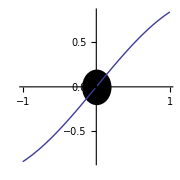

```mathematica
Plot[Sin[x],{x,-1,1},Prolog->Disk[{0,0},0.2],AspectRatio->Automatic]
```

多个 Graphics primitives 可以在一个 list 中顺序写出, 对图形的设置服从 “后声明的设置覆盖先声明的设置” 之原则. 为了明确各个设置的作用范围, 各个 Graphics primitive 也可以分别以 sublists 的形式给出.

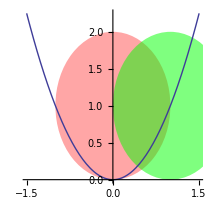

```mathematica
Plot[x^2,{x,-1.5,1.5},Prolog->{Pink,Opacity[0.7],Disk[{0,1},1],Green,Opacity[0.5],Disk[{1,1},1]},PlotStyle->Thick,AspectRatio->Automatic]
```

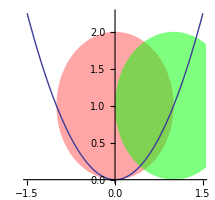

```mathematica
Plot[x^2,{x,-1.5,1.5},Prolog->{{Pink,Opacity[0.7],Disk[{0,1},1]},{Green,Opacity[0.5],Disk[{1,1},1]}},PlotStyle->Thick,AspectRatio->Automatic]
```

如果 Graphics primitives 共享相同的图形设置, 这些设置可以在 sublist 外面整体给出.

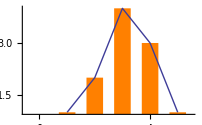

```mathematica
ListLinePlot[data={1,2,4,3,1},Prolog->{Orange,MapIndexed[Rectangle[{First[#2]-.3,0},{First[#2]+.3,#1}]&,data]},
PlotStyle->Thick,PlotRange->{{-0.5,5.5},All},AxesOrigin->{0,0}]
```

The ordinary coordinate system is used for Prolog in 2D graphics:

```mathematica
Table[Graphics[{Pink,Opacity[0.5],Disk[{0,0},10]},Prolog->{Black,Disk[{i,i},2]},Axes->True],{i,{-7.,0.,7.}}]
```

{-Graphics-,-Graphics-,-Graphics-}

A scaled 0, 1 coordinate system is used for Prolog in 3D graphics:

```mathematica
Table[Graphics3D[{Opacity[.5],Sphere[{0,0,0},10]},Prolog->Disk[p,.1]],{p,{{.2,.2},{.5,.5},{.8,.8}}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Objects in Prolog are not included during PlotRange computation:

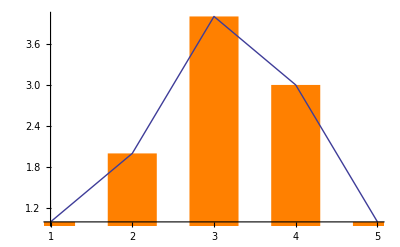

```mathematica
ListLinePlot[data={1,2,4,3,1},Prolog->{Orange,MapIndexed[Rectangle[{First[#2]-.3,0},{First[#2]+.3,#1}]&,data]},
PlotStyle->Thick(*,PlotRange->{{-0.5,5.5},All},AxesOrigin->{0,0}*)]
```

## Epilog

an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered.

```mathematica
SphericalPlot3D[ϕ+√ϕ,{θ,0,Pi},{ϕ,0,3Pi},Epilog->Inset[Framed[Style["Spiral",20],Background->LightYellow],{Right,Bottom},{Right,Bottom}]]
```

-Graphics3D-

The ordinary coordinate system is used for Epilog in 2D graphics

In three-dimensional graphics, only two-dimensional graphics primitives can be specified by the Epilog option. The graphics primitives are rendered in a 0,1 coordinate system.

```mathematica
Table[Graphics3D[Sphere[{0,0,0},10],Epilog->Disk[p,.1]],{p,{{.2,.2},{.5,.5},{.8,.8}}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Objects in Epilog are not part of the PlotRange computation.

Objects in Epilog are drawn on top of any graphics, including the axes

```mathematica
SphericalPlot3D[ϕ,{θ,0,Pi},{ϕ,0,3Pi},Background->Directive[GrayLevel[0.7],Opacity[0.7]],Epilog->Inset[Style["Text",White,Bold,30],Automatic,Automatic,Automatic,{1,1}]]
```

-Graphics3D-

Awesome example: Draw large points where the line and the curve intersect.

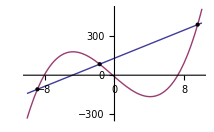

```mathematica
Plot[Evaluate[{f,g}={27 x+130,-12-58 x+x^2+x^3}],{x,-10,10},Epilog->{PointSize[Large],(Point[{#,f/.x->#}]&)/@(x/.NSolve[f==g,x])}]
```

preprocessing

## DisplayFunction

apply a function to graphics or sound object before returning them.

Default DisplayFunction→$DisplayFunction.

## $DisplayFunction

The default for DisplayFunction option.

Typically, the default is Identity.

## Function & Data Visualization

## simple plot

### Plot

Plot has attribute HoldAll and evaluates f only after assigning specific numerical values to x.

整个 Table 表达式位于 Plot 的 expr 位置, 它被 HoldAll. 因此不是作为 a list of expressions 来画图. 图形由一整个 Table 表达式在各个数值节点处的取值 (此时是一个 list) 来构成.

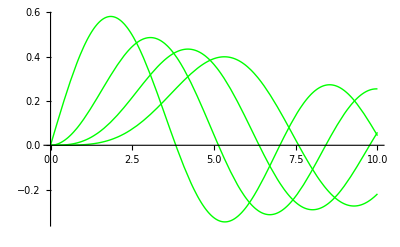

```mathematica
Plot[Table[BesselJ[n,z],{n,1,4}],{z,0,10},PlotStyle->{Red,Orange,Yellow,Green}]
```

下图才是我们需要的结果. The Evaluate overrides the HoldAll attribute of Plot. 从而生成一个 list of expressions 作为 画图表达式. 这样 PlotStyle 才能正确识别.

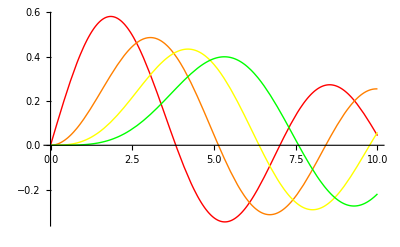

```mathematica
Plot[Evaluate@Table[BesselJ[n,z],{n,1,4}],{z,0,10},PlotStyle->{Red,Orange,Yellow,Green}]
```

### Plot3D

### ListPlot

### ListLinePlot

### ListPlot3D

### ListPointPlot3D

## log plot

### LogPlot

### LogLinearPlot

### LogLogPlot

### ListLogPlot

### ListLogLinearPlot

### ListLogLogPlot

## parametric

### ParametricPlot

### ParametricPlot3D

### PolarPlot

### ListPolarPlot

### RevolutionPlot3D

### SphericalPlot3D

## contour

whereas a curve generated by Plot may be inaccurate if your function varies too quickly in a particular region, the shape of contours generated by ContourPlot can be inaccurate if your function varies too slowly. A rapidly varying function gives a regular pattern of contours, but a function that is almost flat can give irregular contours. You can typically overcome this by increasing the value of PlotPoints or MaxRecursion.

### ContourPlot

### ContourPlot3D

### ListContourPlot

### ListContourPlot3D

## density

### DensityPlot

### ListDensityPlot

## stream

### StreamPlot

### ListStreamPlot

### StreamDensityPlot

### ListStreamDensityPlot

### LineIntegralConvolutionPlot

### ListLineIntegralConvolutionPlot

## vector

### VectorPlot

### ListVectorPlot

### VectorPlot3D

### ListVectorPlot3D

### VectorDensityPlot

### ListVectorDensityPlot

## region

### NumberLinePlot

### RegionPlot

### RegionPlot3D

## reconstruct

### ListCurvePathPlot

### ListSurfacePlot3D

## array

### ArrayPlot

### ReliefPlot

### MatrixPlot

# Images

## Computer Vision

Feature Detection

## Contour Detection

### EdgeDetect

```mathematica
EdgeDetect[image](*find edge and return them as binary image*)
EdgeDetect[image,r](*pixel range r*)
EdgeDetect[image,r,t](*threshold t*)
```

Edges of an image are a set of points between image regions and are typically computed by linking high-gradient pixels.

EdgeDetect uses gradient methods to find edges and works with arbitrary 2D and 3D images.

## Color Processing

Colors

## color models

### RGBColor

### CMYKColor

### Hue

### GrayLevel

## Derived Colors

### Lighter

### Darker

### Blend

### ColorNegate

## Color Schemes

### ColorData

```mathematica
ColorData["scheme"](*gives a function that generates colors in the named color scheme when applied to parameter values.*)
ColorData["scheme","property"](*gives the specified property of a color scheme.*)
ColorData["collection"](*gives a list of color schemes in a named collection.*)
ColorData[](*gives a list of named collections of color schemes.*)
```

### collections

#### "Gradients"

#### "Indexed"

#### "Named"

#### "Physical"

## Named Colors

### Red

### Green

### Blue

### Black

### Gray

### White

### Cyan

### Magenta

### Yellow

### Brown

### Orange

### Pink

### Purple

### their Light variants

### Transparent

# Geometry

## Geometric Transformation

Geometric Object Transformations

## Rotate

```mathematica
Rotate[g,θ](*represent object g rotated by θ*)
Rotate[g,θ,{x,y}](*rotate about {x,y}*)
Rotate[g,{u,v}](*rotate around the origin, with changing vector u to v.*)
```

The object g can be any expression.

If Rotate appears within a graphic, the coordinates {x,y} are taken to be in the coordinate system of the graphic.

If Rotate appears outside a graphic, the coordinates {x,y} are taken to run from -1 to +1 across the bounding box of the object being rotated.

```mathematica
Rotate[x^2+y^2,30Degree]
```

x^2+y^2

## Translate

```mathematica
Translate[g,{x,y,...}](*represent object g translated by vector {x,y,...}*)
Translate[g,{v1,v2,...}](*represent multiple copies of g translated by v1,v2,...*)
```

## Scale

```mathematica
Scale[g,s](*scale object g by factor s*)
Scale[g,s,p](*scale with point p fixed*)
Scale[g,{Subscript[s, x],Subscript[s, y],...},...]
```

# Sound

## Symbolic Sound Language

At the lowest level, all sounds in the Wolfram System are represented as a sequence of amplitude samples, or as a sequence of MIDI events.

All amplitude values obtained must be between -1 and 1.

sound object

## Sound

```mathematica
Sound[{s1,s2,...}](*containing sound primitives*)
Sound[{...},t](*duration t*)
Sound[{...},{Subscript[t, min],Subscript[t, max]}](*from time Subscript[t, min] to Subscript[t, max].*)
```

Sound object can contain other Sound objects as primitives.

Primitives with duration specifications are played consecutively in sequence, independent of primitives with explicit time specifications.

When the outer Sound object doesn’t have time specs, the time specs associated with inner primitives are combined.

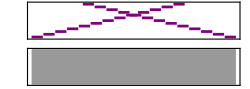

```mathematica
s1=Sound[Table[SoundNote[i],{i,0,12}],{0,1.5}];
s2=Sound[Table[SoundNote[12-i],{i,0,12}],{0.5,2}];
Sound[{s1,s2}]
```

When primitives prims appear in Sound[prims,tspec], the sequence of durations and time specifications in prims are rescaled and shifted to fit into the time interval defined by tspec.

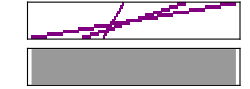

```mathematica
s=Sound[Table[SoundNote[i],{i,0,12}],1];Sound[{Sound[s,{0,2}],Sound[s,{.5,1.5}],Sound[s,{.7,.9}]}]
```

For the outermost Sound object, times are by default taken to be given in absolute seconds.

SoundNote directives can be mixed into the list of primitives, like did in Graphics.

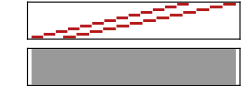

```mathematica
ss=Sound[Table[SoundNote[i],{i,0,12}],1];Sound[{"Flute",Sound[ss,{0,1}],"Trumpet",Sound[ss,{.2,1.3}]}]
```

In Sound[{...},{t_min,t_max}], t_min and t_max are counted starting at the moment the button is clicked.

Sound Primitives

## SampledSoundFunction

```mathematica
SampledSoundFunction[f,n,r]
```

r represents sample rate.

n represents total sample times.

Play generates SampledSoundFunction, in which f is a CompiledFunction.

## SampledSoundList

```mathematica
SampledSoundList[{a1,a2,...},r]
```

ListPlay generates SampledSoundList.

## SoundNote

emit sound

## EmitSound

```mathematica
EmitSound[sound]
EmitSound[{sound1,sound2,...}]
```

EmitSound can play a Sound object.

## Sound Options

## SampleRate

the number of samples per second.

Default SampleRate→8000.

In general, the higher the sample rate, the better high-frequency components in the sound will be rendered.

A sample rate of r typically allows frequencies up to r/2 hertz.

## SampleDepth

bits to be used to encode amplitude levels.

Default SampleDepth→8, which allow 2^8=256 distinct amplitudes.

SampleDepth can be used in Play and ListPlay. In sound primitives, you can specify the sample depth by replacing the sample rate argument by the list {rate,depth}.

## PlayRange

Range of amplitudes to be included for playing.

## SoundVolume

the relative volume of the sound produced.

SoundVolume->v specifies that a sound should be rendered at a fraction v of its default volume.

SoundVolume in the outermost sound construct refers to sound volume relative to the default volume level on your computer system.

values larger than 1 may lead to distorted sounds.

## DisplayFunction

## $DisplayFunction

## Function & Data Sonification

## Play

```mathematica
Play[f,{t,Subscript[t, min],Subscript[t, max]}]
Play[{f1,f2},...](*stereo sound. left-hand and right-hand channels.*)
Play[{f1,f2,...},...](*multi-channel*)
```

In general, the amplitude function you give to Play specifies the instantaneous signal associated with the sound. This signal is typically converted to a voltage, and ultimately to a displacement. Note that amplitude is sometimes defined to be the peak signal associated with a sound; in the Wolfram System, it is always the instantaneous signal as a function of time.

The time variable that appears in Play is always measured in absolute seconds.

When a sound is actually played, its amplitude is sampled a certain number of times every second.

The standard sample rate used for compact disc players is 44100. The effective sample rate in a typical telephone system is around 8000. On most computer systems, the default sample rate used by the Wolfram System is around 8000.

Play is HoldAll.

## ListPlay

```mathematica
ListPlay[{a1,a2,...}](*plays as a sound whose amplitude is given by the sequence of elements in list.*)
ListPlay[{{a11,a12,...},...}](*stereo sound*)
ListPlay[{{...},{...},...}](*multi-channel*)
```

# External Interfaces & Connections

## Calling External Programs

## Compile

```mathematica
Compile[{Subscript[x, 1],Subscript[x, 2],...},expr](*creates a compiled function that evaluates expr assuming numerical values of the Subscript[x, i].*)
Compile[{{Subscript[x, 1],Subscript[t, 1]},...},expr](*assumes that Subscript[x, i] a value that matches the Subscript[t, 1] type.*)
Compile[vars,expr,{{Subscript[p, 1],Subscript[pt, 1]},…}](*assumes that subexpressions in expr that match Subscript[p, i] are of types that match Subscript[pt, i].*)
```

In general, Compile creates a CompiledFunction object which contains a sequence of instructions for evaluating the compiled function. The instructions are chosen to be close to those found in the machine code of  a typical computer, and can thus be executed quickly.

The types handles by Compile are:

The default assumption is that all variables in the expression are approximate real numbers. Other types can be specified using the patterns listed above.

```mathematica
Compile[{{x,_Integer}},x Sin[x]]/@{3,3.5}
```

CompiledFunction::cfsa: Argument 3.5 at position 1 should be a "machine-size integer".

{0.42336,-1.22774}

For simple expressions, the types of objects generated at each step can be deduced from the types of the input variables. For more complicated functions, Compile may not know what type of value to return. By default, Compile assumes that these functions return approximate real numbers. The types of values returned by these expressions can be specified by a list. (The compiled code must make definite assumptions about the types of variables and all objects that arise during the execution of the code.)

The types that Compile handles correspond essentially to the types that computers handle at a machine-code level.

If a compiled function cannot be evaluated with particular arguments using compiled code, ordinary Mathematica code is used instead.

```mathematica
Compile[{x},x Sin[x]]/@{3,x^2}
```

CompiledFunction::cfsa: Argument x^2 at position 1 should be a "machine-size real number".

{0.42336,x^2 Sin[x^2]}

```mathematica
Compile[{x},Sqrt[x]]/@{3,-3}
```

CompiledFunction::cfn: Numerical error encountered at instruction 1; proceeding with uncompiled evaluation.

{1.73205,ⅈ √3}

For large expressions, compilation can speed up execution by a factor as large as 20.

Some bulit-in Mathematica functions use Compile automatically, e.g. NIntegrate, Plot. These functions typically have the option Compiled.

## CompiledFunction

```mathematica
CompiledFunction[](*a head representing compiled code for evaluating a compiled function.*)
```

The arguments include a pure function which is used if the compiled code instruction stream fails to give a result.

```mathematica
Compile[{{x,_Integer}},x Sin[x]]//InputForm
```

CompiledFunction[{8, 9., 5468}, {_Integer}, {{2, 0, 0}, {3, 0, 0}}, {}, {0, 1, 2, 0, 0}, 
 {{10, 0, 0}, {40, 1, 3, 0, 0, 3, 0, 1}, {10, 0, 0}, {16, 0, 1, 0}, {1}}, 
 Function[{x}, x*Sin[x]], Evaluate]

## File Operations

Reading & Writing Files

## Get(<<)

```mathematica
<<name (*reads in a file, evaluating each expression in it and returning the last one.*)
```

# Documents & Presentations

## Mathemtical Typesetting

Table & Layout

## TableForm

## MatrixForm

## Special Characters

Wolfram Language Syntax

## Pure Function

### ↦

ESC fn ESC

Infix operator

x↦y means Function[x,y].

group right: x↦y↦z means x↦(y↦z).

## Notebook Generation

Incremental Document Generation

## CellPrint

```mathematica
CellPrint[expr]
CellPrint[{expr1,expr2,...}](*multiple cells.*)
```

CellPrint is like Print. It actually print a cell rather than return the cell as the value of evaluation.

A Cell is created to contain expr, if expr itself is not a Cell object.

Based on the type of expr, the printed Cell uses different style, which actually has to different internal structure.

```mathematica
CellPrint["text"]
```

text

```mathematica
CellPrint[expr]
```

expr

## Print

Print is a special case of CellPrint.

## Notebook Programming

Notebook Structure

Show expresson: Ctrl+Shift+E

Notebook,Cell 等结构是 notebook 的 raw structure. 还不能构成完整的 notebook expression (从完整的可以直接显示的文档的角度).

## notebooks

### Notebook

```mathematica
Notebook[{Subscript[cell, 1],Subscript[cell, 2],...}]
Notebook[{Subscript[cell, 1],Subscript[cell, 2],...},options]
```

In addition to notebook options, you can also set any cell option at the notebook level. Doing this tells the Wolfram System to use that option setting as the default for all the cells in the notebook.

### NotebookObject

```mathematica
NotebookObject[fe,id](*an object that represents an open notebook in the front end.*)
```

Within the Wolfram Language kernel, notebooks that you have open in the front end are referred to by notebook objects.

NotebookObject 只具有引用前端打开的 notebook object 的作用. It isn’t a complete notebook expression itself.

The first argument specifies the FrontEndObject for the front end in which the notebook resides, while the second argument gives a unique serial number for the notebook.

NotebookObject 只是一个已打开的 notebook 的指针. 它代表这个 notebook.

A NotebookObject is permanently invalid after a notebook is closed, even if that notebook is reopened.

## cells

### Cell

```mathematica
Cell[contents]
Cell[contents,"style"]
Cell[contents,"style",options]
```

The contents of a cell can be: "text",TextData,BoxData,OutputFormData,RawData,GraphicsData,CellGroupData,StyleData.

### CellObject

```mathematica
CellObject[id](*a representation of a cell in front end.*)
```

### TextData

```mathematica
TextData[expr](*the contents of a textual cell.*)
TextData[{Subscript[expr, 1],Subscript[expr, 2],...}](*the contents with several expressions.*)
```

Textual cells can contain unformatted or formatted text such as styles, buttons, inline cells, etc.

Cell[TextData["string"]] equals to Cell["string"], both of which are cells with unformatted text.

### BoxData

```mathematica
BoxData[boxes](*the contents of a typesetting cell.*)
```

Typesetting cells contain two-dimensional input, grids, frames, two- and three-dimensional graphics, and other related constructs.

### OutputFormData

```mathematica
OutputFormData["in-text","out-text"](*the content of OutputForm of an expression*)
```

```mathematica
Integrate[x,x]//OutputForm
```

Cell[OutputFormData["\<\
x^2/2\
\>", "\<\
 2
x
--
2\
\>"], "Output",
 CellChangeTimes->{{3.626778852915831*^9, 3.6267788606101627`*^9}, 3.626779439853366*^9},
 CellLabel->"Out[4]//OutputForm="]

### RawData

```mathematica
RawData["data"](*unformatted expressions by Show Expression*)
```

### CellGroupData

```mathematica
CellGroupData[{Subscript[cell, 1],Subscript[cell, 2],...}](*the contents of a group of cells*)
CellGroupData[{Subscript[cell, 1],Subscript[cell, 2],...},Open/Closed](*status*)
CellGroupData[{cell_(1,)Subscript[cell, 2],...},1](*first cell open*)
CellGroupData[{cell_(1,)Subscript[cell, 2],...},{pos_(1,)Subscript[pos, 2],...}](*cells at specified positions open*)
```

### StyleData

```mathematica
StyleData["style"](*the contents of a style definition cell.*)
StyleData["style","environment"]
```

Style definition cells are located in stylesheets and contain option values for a particular cell style.

Style definition cells have the form Cell[StyleData["style"],options].

StyleData["style"] will inherit any definitions of "style" from parent stylesheets.

StyleData["style",StyleDefinitions->None] represents the contents of a style definition cell, ignoring any definitions of "style" from parent stylesheets.

StyleData["style",StyleDefinitions->StyleData["inheritedstyle"]] represents the contents of a style definition cell, inheriting any definitions of "inheritedstyle" from parent stylesheets.

Parent stylesheets are defined by a style cell with the form StyleData[StyleDefinitions->stylesheet], where stylesheet can take any of the forms allowed for the StyleDefinitions option at the notebook level.

Different screen environments are listed in menu item.

```mathematica
CellPrint[Cell[StyleData["Section","Condensed"]]]
```

Section

## Boxes

### RowBox

### GridBox

### SuperscriptBox

### SubscriptBox

### SubsuperscriptBox

### OverscriptBox

### UnderscriptBox

### UnderoverscriptBox

### FractionBox

### SqrtBox

### RadicalBox

### StyleBox

### FrameBox

### AdjustmentBox

### FormBox

### InterpretationBox

### TagBox

### ErrorBox

## NotebookPut

```mathematica
NotebookPut[expr]
(*creates a notebook corresponding to Notebook expr and makes it the currently selected notebook in the front end.*)
NotebookPut[expr,options]
NotebookPut[]
(*create a empty notebook*)
NotebookPut[expr,obj](*replace the contents of notebook obj with expr.*)
```

The expression expr should have head Notebook, and contain raw Cell objects, with boxes data.

NotebookPut returns a NotebookObject corresponding to the notebook it creates.

Even if the output of NotebookObject is suppressed, the corresponding notebook will still show up and be selected.

Any options available for Notebook can be used here.

```mathematica
NotebookPut[];
```

## NotebookGet

Choose Notebook

## SelectedNotebook

```mathematica
SelectedNotebook[]
```

The currently selected notebook is the one to which notebook-oriented menu commands in the front end will be directed. Textual commands, however, are directed to the input notebook.

## EvaluationNotebook

```mathematica
EvaluationNotebook[](*gives the notebook in which this function is being evaluated.*)
```

## InputNotebook

```mathematica
InputNotebook[]
```

The current input notebook is the notebook to which textual commands in the front end are normally directed.

InputNotebook 指的是现在能进行 input 的那个 notebook.

当 InputNotebook[] 出现在 PaletteNotebook 中时, 得到的 InputNotebook 指的是切换到 PaletteNotebook 之前的那个 notebook. 这是因为, palette notebook 本身不能输入, 且 textual commands 一般是从 palette 引导至之前的 notebook. 故 InputNotebook[] 就是之前那个. 例如, 以下两个例子分别写入 Done 在不同的 notebook 里.

```mathematica
CreatePalette[{Button["Test",NotebookWrite[InputNotebook[],"Done"];NotebookClose[EvaluationNotebook[]]]}]
```

```mathematica
CreateDocument[{Button["Test",NotebookWrite[InputNotebook[],"Done"];NotebookClose[EvaluationNotebook[]]]}]
```

注意 InputNotebook 出现在不同地方时所指的 notebook 可能不同:

```mathematica
Print@InputNotebook[];CreatePalette[{Button["Test",NotebookWrite[InputNotebook[],"Done"];NotebookClose[ ButtonNotebook[]]]}];Print@InputNotebook[]
```

r6ujn_shm16FrontEndObject[LinkObject["r6ujn_shm", 3, 1]]16Function Notes.nb/home/naitreey/Dropbox/Professional/Professional_Notes_and_Knowledge/Computer_Science/Mathematica/Function Notes.nb

r6ujn_shm46FrontEndObject[LinkObject["r6ujn_shm", 3, 1]]46Untitled-7

## ButtonNotebook

```mathematica
ButtonNotebook[](*gives the notebook, if any, that contains the button which initiated the current evaluation. *)
```

## ParentNotebook

```mathematica
ParentNotebook[obj](*the NotebookObject that contains obj.*)
```

obj can be BoxObject or CellObject.

## SetSelectedNotebook

```mathematica
SetSelectedNotebook[obj]
```

obj can be a NotebookObject or CellObject. If obj is a CellObject, then the notebook containing obj will be selected.

Making a notebook the currently selected one does not affect the current selection within that notebook, or within other notebooks.

Notebook Operations

## Notebooks

```mathematica
Notebooks[](*a list of open notebooks.*)
Notebooks[fe](*for specific front end.*)
Notebooks["name"](*a list of all open notebooks with the specified name*)
```

## NotebookOpen

```mathematica
NotebookOpen["name.nb"]
NotebookOpen["name.nb",options]
NotebookOpen["//url.nb"]
```

NotebookOpen returns a NotebookObject and opens the specified notebook.

## NotebookSave

```mathematica
NotebookSave[notebook]
NotebookSave[notebook,"filename"]
NotebookSave[](*current evaluation notebook*)
```

NotebookSave[notebook] saves the notebook in a file whose name is given by the notebook object notebook.

If you do not provide a file name for a new notebook (which hasn’t been saved before), you will be prompted to choose one.

## NotebookClose

```mathematica
NotebookClose[notebook]
NotebookClose[]
```

NotebookClose will make a notebook disappear from your screen, and will invalidate all notebook objects that refer to that notebook.

Unsaved changed will be lost. It simply close the notebook.

## NotebookPrint

```mathematica
NotebookPrint[expr](*create and print a notebook containing expr.*)
NotebookPrint[notebook](*print entire notebook*)
NotebookPrint[NotebookSelection[notebook]](*print the selected part*)
NotebookPrint[expr,"filename.ext"](*save a print-ready copy*)
NotebookPrint[]
```

NotebookPrint[expr] is equivalent to NotebookPrint[CreateDocument[expr]].

## CreateWindow

```mathematica
CreateWindow[]
CreateWindow[notebookExpression]
CreateWindow[nbexpr,obj](*replace notebook obj with nbexpr*)
```

notebook expression should be a complete notebook expression: DocumentNotebook,PaletteNotebook,DialogNotebook.

对于这些完整的 notebook expressioon, CreateWindow 的作用是将它们用一个 window 表示出来.

CreateWindow can take any notebook option.

## CreateDocument

Essentially a combination of CreateWindow and DocumentNotebook.

## CreatePalette

Essentially a combination of CreateWindow and PaletteNotebook.

## CreateDialog

Essentially a combination of CreateWindow and DialogNotebook.

Content Selection

## SelectionMove

```mathematica
SelectionMove[obj,dir,unit]
SelectionMove[obj,dir,unit,n](*n times of movement*)
```

obj=NotebookObject,CellObject,BoxObject.

dir=Next,Previous,After,Before,All.

The front end will also usually highlight the region corresponding to the result.

With direction specifications After and Before, SelectionMove will usually make the current selection be an insertion point between two units of the specified type.

## NotebookFind

```mathematica
NotebookFind[obj,data](*move to next match*)
NotebookFind[obj,data,Previous](*previous match*)
NotebookFind[obj,data,All](*select all matches*)
NotebookFind[obj,data,dir,elems]
```

obj may be a NotebookObject or a CellObject. If obj is a NotebookObject, then the find operation starts where the selection is in the notebook.

data can be a string, box expression, or a complete cell.

Possible values of dir include Next, Previous, and All.

The default for elems is CellContents. Only the contents of boxes, not their styles or options, are included in the search.

The front end will highlight the region corresponding to the result.

## NotebookLocate

```mathematica
NotebookLocate["tag"]
NotebookLocate[{"file.nb","tag"}]
```

NotebookLocate is used for following hyperlinks within one notebook or between notebooks.

NotebookLocate is typically the underlying function that the Wolfram Language calls when you follow a hyperlink in a notebook.

## NotebookSelection

```mathematica
NotebookSelection[]
NotebookSelection[nb]
```

You can use Options and SetOptions to read and write options associated with your current selection.

Content Operations

## NotebookWrite

```mathematica
NotebookWrite[notebook,data]
NotebookWrite[obj,data]
NotebookWrite[obj,data,selection]
```

NotebookWrite to a NotebookObject does essentially the same as a Paste operation in the front end: it replaces whatever the current selection in the notebook is by data.

NotebookWrite automatically wraps Cell around the data you specify if this is necessary.

selection=Before,After,All,None,Placeholder.

The default for sel is After, so that NotebookWrite[obj,data] can be called repeatedly to insert several pieces of data in sequence.

```mathematica
Button["click",NotebookWrite[EvaluationBox[],ToBoxes[DateString[]]]]
```

click

## NotebookApply

```mathematica
NotebookApply[notebook,data]
NotebookApply[cell,data]
NotebookApply[notebook,data,selection]
```

NotebookApply has the same effect as NotebookWrite, except that it replaces the first selection placeholder in data by the current selection.

NotebookApply can be used in setting up actions for buttons in palettes.

Selection placeholders are represented by the character ■ (\[SelectionPlaceholder]).

## NotebookDelete

```mathematica
NotebookDelete[notebook](*delete selection in the specified notebook*)
NotebookDelete[obj]
NotebookDelete[{Subscript[obj, 1],Subscript[obj, 2],...}]
NotebookDelete[](*delete selection in current notebook*)
```

After using NotebookDelete on a NotebookObject, the current selection becomes an insertion point at the position of the deleted material.

```mathematica
Button["delete",NotebookDelete[EvaluationCell[]]]
```

delete

```mathematica
Table[Button["delete",NotebookDelete[EvaluationBox[]]],{10}]
```

{delete,delete,delete,delete,delete,delete,delete,delete,delete,delete}

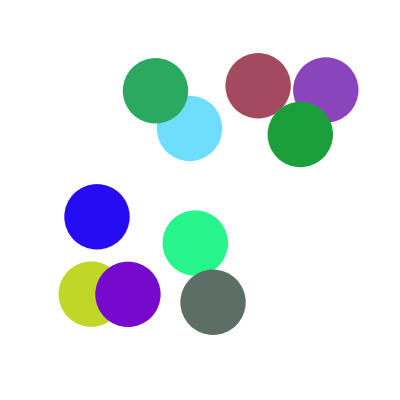

```mathematica
Graphics[MapThread[Button[{#1,Disk[#2,0.5]},NotebookDelete[EvaluationBox[]]]&,{RandomColor[10],RandomReal[{0.5,4.5},{10,2}]}],PlotRange->{{0,5},{0,5}}]
```

```mathematica
Graphics[Button["this",x=2]]
```

-Graphics-

## NotebookRead

```mathematica
NotebookRead[notebook](*read in a selection*)
NotebookRead[obj](*read in obj*)
NotebookRead[{Subscript[obj, 1],obj_(2,)...}]
```

```mathematica
PaletteNotebook[Button["Upper Case",With[{notebook=EvaluationNotebook[]},SelectionMove[notebook,All,Word];NotebookWrite[notebook,ToUpperCase@NotebookRead[notebook]]]]]
```

Upper Case

## SelectionEvaluate

```mathematica
SelectionEvaluate[notebook](*evaluate the selection in a notebook*)
SelectionEvaluate[notebook,selection](*also set selection after evaluation*)
```

Default for selection is After.

None dosen’t move selection.

## SelectionEvaluateCreateCell

```mathematica
SelectionEvaluateCreateCell[notebook]
SelectionEvaluateCreateCell[notebook,selection]
```

SelectionEvaluateCreateCell performs the same underlying operation as typing Shift+ in the front end. It does not, however, have side effects such as incrementing $Line.

SelectionEvaluateCreateCell doesn’t require the entire cell or contents of cell being selected to perform its action, as is also true for Shift+Enter in the front end.

## SelectionCreateCell

```mathematica
SelectionCreateCell[notebook]
SelectionCreateCell[notebook,selection]
```

Global Front End Operations

The basic way that the Wolfram Language distinguishes between commands to be executed in the kernel and to be executed directly in the front end is by using contexts. The kernel commands are in the usual System` context, but the front end commands are in the FrontEnd` context.

The standard Wolfram System front end can handle only specific notebook manipulation commands such as NotebookApply, NotebookLocate, and SelectedNotebook. It uses the versions of these commands in the FrontEnd` context. So for some FrontEnd/notebook specific functions, there are two versions of them, one in System` context, another in FrontEnd` context.

When you execute a command like NotebookWrite[obj,data] the actual operation of inserting data into your notebook is performed in the front end. Normally, however, the kernel is needed in order to evaluate the original command, and to construct the appropriate request to send to the front end.

When using corresponding FrontEnd` functions, the kernel is not involved in the process of execution. The operation will be performed entirely by front end.

For the kinds of operations typically performed by simple buttons, you may find that it is possible to execute all the commands you need directly in the front end—without the kernel even needing to be running.

## $FrontEnd

```mathematica
$FrontEnd(*the FrontEndObject to which the kernel is currently connected.*)
```

$FrontEnd is a FrontEndObject, or Null.

Options,SetOptions,CurrentValue to view and change value of front end option.

Options set for $FrontEnd are by default stored in the front end init.m file, and are persistent between front end sessions.

## FrontEndToken

```mathematica
FrontEndToken["cmd"](*an object which represents a front end command token,
                       typically corresponding to a front end menu item*)
FrontEndToken[nb,"cmd"]
FrontEndToken[nb,"cmd",parameter]
```

Front end tokens let you perform kernel commands that would normally be done using the menus.

Front end tokens are divided into two classes: simple tokens and compound tokens that take parameters.

With one argument, FrontEndToken operates on the input notebook.

The mapping between command tokens and menu items or keyboard shortcuts is defined in front end text resource files.

## FrontEndTokenExecute

```mathematica
FrontEndTokenExecute["cmd"](*executes the specified front end command token*)
FrontEndTokenExecute[nb,"cmd"]
FrontEndTokenExecute[nb,"cmd",parameter]
```

## FrontEndExecute

```mathematica
FrontEndExecute[expr](*send expr to be executed by front end.*)
```

FrontEndExecute sends functions to be executed by Front End. The available functions are those in FrontEnd` context.

## FrontEnd` functions

FrontEnd` functions are executed completely by front end. Nothing will happen if they are sent to kernel for execution.

```mathematica
FrontEnd`NotebookWrite[FrontEnd`SelectedNotebook[],this]
```

FrontEnd`NotebookWrite[FrontEnd`SelectedNotebook[],this]

To cause front end to execute these FrontEnd` command, wraps them with FrontEndExecute.

```mathematica
FrontEndExecute@%
```

```mathematica
$CellContext`this
```

## Notebook Formatting & Styling

Cell Styling Options

## Frame & background

### Background

Background can be any color.

The specified color will normally be used as a background throughout the region defined by the object.

In constructs such as Grid, Item can be used to specify that a background should fill the complete region for a particular item.

For table objects, the setting for Background can be a list that specifies backgrounds for individual columns, rows, or elements.

### CellFrame

```mathematica
CellFrame->True|False
CellFrame->n(*thickness by absolute pts*)
CellFrame->{{left,right},{bottom,top}}(*thickness of respective edges by absolute pts.*)
```

### CellFrameMargins

```mathematica
CellFrameMargins->n(*n pts on all sides.*)
CellFrameMargins->{{left,right},{bottom,top}}
```

### CellFrameColor

```mathematica
CellPrint[Cell["this",TextAlignment->Center,CellFrame->True,CellFrameMargins->20,CellFrameColor->Yellow,CellFrameLabels->{{a,b},{c,d}}]]
```

this

### CellFrameLabels

```mathematica
CellFrameLabels->{{left,right},{bottom,top}}
```

```mathematica
CellPrint[Cell["this",CellFrame->True,CellFrameLabels->{{x,x},{"",""}}]]
```

this

### CellFrameLabelMargins

```mathematica
CellFrameLabelMargins->n
CellFrameLabelMargins->{{left,right},{bottom,top}}
```

## Margin & Baseline

### CellMargins

You can set the horizontal margins interactively by using the margin stops in the ruler displayed when you choose the Ruler menu item in the front end.

### CellBaseline

## Cell Brackets

### ShowGroupOpener

### ShowCellBracket

### CellOpen

## Cell Labels

### CellLabel

### ShowCellLabel

### CellLabelAutoDelete

## Cell Tags

### CellTags

### ShowCellTags

## Cell Properties

### Editable

### Copyable

### Deletable

### Selectable

### Evaluatable

### Deployed

## Evaluation

### Evaluator

### CellAutoOverwrite

### GeneratedCell

The setting for GeneratedCell is used to determine which cells should be considered as Wolfram Language output.

Any cell obtained as an output or side effect from a kernel evaluation has the setting GeneratedCell->True.

### InitializationCell

## Pagebreak

### PageBreakAbove

### PageBreakWithin

### PageBreakBelow

### GroupPageBreakWithin

## Misc.

### CellDingbat

### Magnification

# System Operations & Setup

## Mathematica Sessions

Session Information

Session History

## In

Syntax is identical to Out below.

In,Out is Listable.

In[n] label 与 Out[n] label 实际上都是 pattern, 每次运算同时定义了相应的  In,Out 的 downvalue.

```mathematica
a
```

a

```mathematica
??In
```

In[n] is a global object that is assigned to have a delayed value of the n^th input line.

Attributes[In]={Listable,Protected}
 
In[1]:=a
 
In[2]:=Information[In,LongForm→True]

In,Out 有一个重要区别, 其实也很显然, 只是平时视而不见: In 的 downvalue 都是 SetDelayed, 因此每次 invoke In[n] 时, 表达式都会重新运算, 并输出结果. 而 Out 不然, 它的值是 Set, 记录的一定是过去的计算结果.

## Out

```mathematica
Out[n](*a global object that is assigned to be the value produced on the n^th output line*)
%n
Out[]
%
Out[-n]
%n
%% (*the result before last*)
%%...% (*k times. the k^th previous result*)
Out[{Subscript[n, 1],Subscript[n, 2],...}]
```

In 和 Out 只记录输入/输出的表达式的内部形式. 不记录该表达式输入输出时采用的具体形式.

Since In,Out are built-in symbols, all their values are protected. to clear specific In,Out history entries, first Unprotect them and then Clear them.

## InString

```mathematica
InString[n]
InString[]
InString[-n]
```

```mathematica
f[n]
```

f[n]

```mathematica
InString[]
```

\(f[n]\)

```mathematica
In[{1,2}]
```

{f[n],\(InString[]\)}

```mathematica
In[]
```

{f[n],\(In[\({1, 2}\)]\)}

```mathematica
Out[]
```

{f[n],\(In[\({1, 2}\)]\)}

```mathematica
MessageList[5]
```

{}

## $HistoryLength

Default is Infinity.

Using smaller values of $HistoryLength can save substantial amounts of memory in a Wolfram System session.

## $Line

The number of current input line. It can be reset.

When $Line is reset, new In,Out are numbered all over again, overwriting the previous ones with the same number.

Session Customization

## Modify input and output

### $PreRead

$PreRead is applied to input string.

By default, $PreRead is not defined, meaning input strings are sent directly to evaluation.

$PreRead is applied before InString[n] is assigned.

### $Pre

By default, $Pre is not defined, meaning the input is evaluated directly.

Unless $Pre is assigned to be a function which holds its arguments unevaluated, input expressions will be evaluated before $Pre is applied, so the effect of $Pre will be the same as $Post.

$Pre is applied to expressions, while $PreRead is applied to strings which have not yet been parsed into expressions.

### $Post

By default, $Post is not defined, meaning output comes directly from evaluation.

### $PrePrint

$PrePrint is applied after Out[n] is assigned, but before the output result is printed.

By default, $PrePrint is not defined, meaning output is shown as it comes from evaluation:

### $SyntaxHandler

The arguments given to $SyntaxHandler are the complete input string and an integer specifying the character position at which the syntax error was detected.

Any string returned by $SyntaxHandler is used as a new version of the input string, and is fed to the Wolfram Language. If the string does not end with a newline, the Wolfram Language waits for input to complete the line.

If $SyntaxHandler returns $Failed, input to the Wolfram Language is abandoned if possible.